Sam Dolan, February 2024.
This is a notebook to reconstruct the lm-modes of the metric in Lorenz gauge, in the frequency domain, for a circular orbit on Kerr spacetime. 
The code below is a stripped-down version of metric_components_kerr_s0s1s2.nb to focus on efficient calculation of lm modes, and m modes.
Nearly all the formulation checks have been removed, and only the necessary projections for determining the jumps have been retained. See metric_components_... for a fuller code. This code requires the Black Hole Perturbation Toolkit.

The 10 components of the metric perturbation that I use are h_{ab} projected onto an unnormalised tetrad. These are numbered 1 to 10 and always in the following order:
[ h_{l+l+}, h_{l-l-}, h_{m+ m+}, h_{m- m-}, ρ h_{l+ m+}, ρ* h_{l+ m-}, ρ* h_{l- m+}, ρ h_{l- m-}, Σ Δ h_{l+ l-}, h (the trace) ].
See Eq. (128) in the DDKW paper,arXiv:2306.16459 .
The spin-weight of each component follows from counting the number of m+ projections and subtracting the number of m- projections.

The input parameters are read from a file: config/config<iConfig>.txt.  Note that you will need one config file for each value of m (the azimuthal mode number).

Sections 1 to 4 are necessary set up. These should run in circa 10 minutes, depending on the parameters in “config”.
The output of Section A (1D grid) are functions of r only, for the 10 components projected onto spin-weighted spherical harmonics.
The output of Section B (2D grid) are functions of (r,θ) for the 10 components. 
Sections A and B typically take longer to run than sections 1-4, depending on the parameters chosen in “grid.txt”. You may choose to run either A or B, instead of both. Now that it is working somewhat efficiently, I think that A is the better way to go.

The parameters are read from a file identified by “iConfig”. There is a naming convention. iConfig should the form XX-YYY-ZZZ, where XX are the first two digits of “a” after the decimal point (i.e. 00 for Schwarzschild, 60 for a=0.6M, 99 for a=0.99M), YYY are the digits of r0 (with 060 implying r0 = 6.0), and ZZZ are the run numbers, with the first digit typically labelling the internal parameter choices (such as grid size), and the latter two digits indicating the value of ‘m’. The numbers 0ZZ are reserved for testing, whereas the numbers zZZ with z >= 1 are for production runs.

```mathematica
ClearAll["Global`*"]
<<SpinWeightedSpheroidalHarmonics`
<<Teukolsky`
Off[ClebschGordan::phy];Off[ClebschGordan::tri];
```

```mathematica
iConfig="00-060-022";(* Identifies the parameter file. *)
(* If run as a script, read iConfig from the command line. *)
If[Length[$ScriptCommandLine]==2,
iConfig=$ScriptCommandLine[[2]];
Print["iConfig = " <> ToString[iConfig]];
directory=Directory[]<>"/";
,
directory=NotebookDirectory[];
];
Print[directory];
```

/Users/sm1srd/Code/KerrLorenz/

## 1. Preliminaries

```mathematica
Print["1. Preliminaries."];
```

1. Preliminaries.

### Metric and tetrad

```mathematica
ρ=r+I*a*Cos[θ];
ρc=r-I*a*Cos[θ];
Σ=ρ*ρc;
Δsubs={Δ[r]->r^2-2*M*r+a^2,Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0};
Ksubs={K[r]->ω*(r^2+a^2)-a*m,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
ΔKsubs=Join[Δsubs,Ksubs];
ΔKsimp={Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
QQ=m/Sin[θ]-a*ω*Sin[θ];
a0subs={a->0};
Dop[n_,R_]:=D[R,r]-I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Ddag[n_,R_]:=D[R,r]+I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Lop[n_,R_]:=D[R,θ]+QQ*R+n*Cot[θ]*R;
Ldag[n_,R_]:=D[R,θ]-QQ*R+n*Cot[θ]*R;
Dop[R_]:=Dop[0,R];
Ddag[R_]:=Ddag[0,R];
Lop[R_]:=Lop[0,R];
Ldag[R_]:=Ldag[0,R];
```

```mathematica
(* Inverse metric *)
lpvec={(r^2+a^2)/Δ[r],1,0,a/Δ[r]};
lmvec={-(r^2+a^2)/Δ[r],1,0,-a/Δ[r]};
mpvec={I*a*Sin[θ],0,1,I/Sin[θ]};
mmvec={-I*a*Sin[θ],0,1,-I/Sin[θ]};
gup=Table[1/(2*Σ)*(Δ[r]*(lpvec[[i]]*lmvec[[j]]+lmvec[[i]]*lpvec[[j]])+mpvec[[i]]*mmvec[[j]]+mmvec[[i]]*mpvec[[j]]),{i,1,4},{j,1,4}];
Simplify[Det[gup]+1/(Σ^2*Sin[θ]^2)]
tmp=gup.{-EE,0,0,LL}/.{θ->π/2}//Simplify;
utsubs={ut->tmp[[1]]};
```

0

### Spin-2

```mathematica
(* Teuksolky equations for spin 2 *)
teukPm=Δ[r]*Ddag[-1,Dop[Pm2[r]]]-6*I*ω*r*Pm2[r]-Λ*Pm2[r];
teukPp=Δ[r]*Dop[-1,Ddag[Pp2[r]]]+6*I*ω*r*Pp2[r]-Λ*Pp2[r];
teukSm=Lop[-1,Ldag[2,Sm2[θ]]]+6*a*ω*Cos[θ]*Sm2[θ]+Λ*Sm2[θ];
teukSp=Ldag[-1,Lop[2,Sp2[θ]]]-6*a*ω*Cos[θ]*Sp2[θ]+Λ*Sp2[θ];
Pm2subs2=Solve[teukPm==0,Pm2''[r]]//First//Simplify;
Pm2subs3=D[Pm2subs2,r]/.Pm2subs2/.ΔKsimp//Simplify;
Pm2subs4=D[Pm2subs3,r]/.Pm2subs2/.ΔKsimp//Simplify;
Pm2subs=Join[Pm2subs2,Pm2subs3,Pm2subs4];
Pp2subs2=Solve[teukPp==0,Pp2''[r]]//First//Simplify;
Pp2subs3=D[Pp2subs2,r]/.Pp2subs2/.ΔKsimp//Simplify;
Pp2subs4=D[Pp2subs3,r]/.Pp2subs2/.ΔKsimp//Simplify;
Pp2subs=Join[Pp2subs2,Pp2subs3,Pp2subs4];
Sm2subs2=Solve[teukSm==0,Sm2''[θ]]//First//Simplify;
Sm2subs3=D[Sm2subs2,θ]/.Sm2subs2//Simplify;
Sm2subs4=D[Sm2subs3,θ]/.Sm2subs2//Simplify;
Sm2subs=Join[Sm2subs2,Sm2subs3,Sm2subs4];
Sp2subs2=Solve[teukSp==0,Sp2''[θ]]//First//Simplify;
Sp2subs3=D[Sp2subs2,θ]/.Sp2subs2//Simplify;
Sp2subs4=D[Sp2subs3,θ]/.Sp2subs2//Simplify;
Sp2subs=Join[Sp2subs2,Sp2subs3,Sp2subs4];
teuks2subs=Join[Pm2subs,Pp2subs,Sm2subs,Sp2subs];
```

```mathematica
(* Teukolsky-Starobinskii identities for spin 2 *)
tsPp=(Δ[r]^2*Dop[Dop[Dop[Dop[Pm2[r]]]]]-CC*Pp2[r])/.ΔKsimp;
tsPm=(Δ[r]^2*Ddag[Ddag[Ddag[Ddag[Pp2[r]]]]]-Cstar*Pm2[r])/.ΔKsimp;
tsSp=Ldag[-1,Ldag[0,Ldag[1,Ldag[2,Sm2[θ]]]]]-AA*Sp2[θ];
tsSm=Lop[-1,Lop[0,Lop[1,Lop[2,Sp2[θ]]]]]-AA*Sm2[θ];
t0=Solve[tsPp==0,Pp2[r]]/.Pm2subs/.ΔKsimp//First//Simplify;
Pp2repl=Join[t0,D[t0,r]/.Pm2subs/.ΔKsimp//Simplify];
t0=Solve[tsPm==0,Pm2[r]]/.Pp2subs/.ΔKsimp//First//Simplify;
Pm2repl=Join[t0,D[t0,r]/.Pp2subs/.ΔKsimp//Simplify];
t0=Solve[tsSp==0,Sp2[θ]]/.Sm2subs//First//Simplify;
Sp2repl=Join[t0,D[t0,θ]/.Sm2subs//Simplify];
t0=Solve[tsSm==0,Sm2[θ]]/.Sp2subs//First//Simplify;
Sm2repl=Join[t0,D[t0,θ]/.Sp2subs//Simplify];
```

```mathematica
(* Teukolsky-Starobinskii constants for spin 2 *)
Crepl0={CC->AA+sgn*12*I*M*ω,Cstar->AA-sgn*12*I*M*ω};
Crepl1={Cstar->(AA^2+144*M^2*ω^2)/CC,CC->(AA^2+144*M^2*ω^2)/Cstar};
Asqrepl={AA^2->Λ^2*(Λ+2)^2-8*ω^2*Λ*(αsq*(5*Λ+6)-12*a^2)+144*ω^4*αsq^2}/.{αsq->a^2-a*m/ω};
(* Test *)
t0=Dop[Dop[Dop[Dop[Pm2[r]]]]]/.Pm2subs/.Pm2repl/.ΔKsimp//Simplify
t1=FullSimplify[t0/.Crepl1/.Asqrepl/.Δsubs/.Ksubs]
Aschwrepl={AA->Λ*(Λ+2)};
sgnsq={sgn^2->1};
```

(Pp2[r] (4 Λ^2+4 Λ^3+Λ^4+144 M^2 ω^2+192 M r Λ ω^2-48 r^2 Λ ω^2+40 r^2 Λ^2 ω^2+144 r^4 ω^4-8 ω (6 Λ+5 Λ^2+36 r^2 ω^2) K[r]+144 ω^2 K[r]^2+96 Λ ω^2 Δ[r]))/(Cstar Δ[r]^2)

(CC Pp2[r])/((a^2+r (-2 M+r))^2)

### Spin-1

```mathematica
(* Teukolsky equations for spin 1. *)
teukPm1=Δ[r]*Ddag[Dop[Pm1[r]]]-2*I*ω*r*Pm1[r]-λ*Pm1[r];
teukPp1=Δ[r]*Dop[Ddag[Pp1[r]]]+2*I*ω*r*Pp1[r]-λ*Pp1[r];
teukSm1=Lop[Ldag[1,Sm1[θ]]]+2*a*ω*Cos[θ]*Sm1[θ]+λ*Sm1[θ];
teukSp1=Ldag[Lop[1,Sp1[θ]]]-2*a*ω*Cos[θ]*Sp1[θ]+λ*Sp1[θ];
Pm1subs2=Solve[teukPm1==0,Pm1''[r]]//First//Simplify;
Pm1subs3=D[Pm1subs2,r]/.Pm1subs2/.ΔKsimp//Simplify;
Pm1subs4=D[Pm1subs3,r]/.Pm1subs2/.ΔKsimp//Simplify;
Pm1subs=Join[Pm1subs2,Pm1subs3,Pm1subs4];
Pp1subs2=Solve[teukPp1==0,Pp1''[r]]//First//Simplify;
Pp1subs3=D[Pp1subs2,r]/.Pp1subs2/.ΔKsimp//Simplify;
Pp1subs4=D[Pp1subs3,r]/.Pp1subs2/.ΔKsimp//Simplify;
Pp1subs=Join[Pp1subs2,Pp1subs3,Pp1subs4];
Sm1subs2=Solve[teukSm1==0,Sm1''[θ]]//First//Simplify;
Sm1subs3=D[Sm1subs2,θ]/.Sm1subs2//Simplify;
Sm1subs4=D[Sm1subs3,θ]/.Sm1subs2//Simplify;
Sm1subs=Join[Sm1subs2,Sm1subs3,Sm1subs4];
Sp1subs2=Solve[teukSp1==0,Sp1''[θ]]//First//Simplify;
Sp1subs3=D[Sp1subs2,θ]/.Sp1subs2//Simplify;
Sp1subs4=D[Sp1subs3,θ]/.Sp1subs2//Simplify;
Sp1subs=Join[Sp1subs2,Sp1subs3,Sp1subs4];
teuks1subs=Join[Pm1subs,Pp1subs,Sm1subs,Sp1subs];
```

```mathematica
(* Teukolsky-Starobinskii identities for spin 1. *)
tsPp1=Δ[r]*Dop[Dop[Pm1[r]]]-BB*Pp1[r];
tsPm1=Δ[r]*Ddag[Ddag[Pp1[r]]]-BB*Pm1[r];
tsSp1=Ldag[0,Ldag[1,Sm1[θ]]]-BB*Sp1[θ];
tsSm1=Lop[0,Lop[1,Sp1[θ]]]-BB*Sm1[θ];
t0=Solve[tsPp1==0,Pp1[r]]/.Pm1subs/.ΔKsimp//First//Simplify;
Pp1repl=Join[t0,D[t0,r]/.Pm1subs/.ΔKsimp//Simplify]
t0=Solve[tsPm1==0,Pm1[r]]/.Pp1subs/.ΔKsimp//First//Simplify;
Pm1repl=Join[t0,D[t0,r]/.Pp1subs/.ΔKsimp//Simplify];
t0=Solve[tsSp1==0,Sp1[θ]]/.Sm1subs//First//Simplify;
Sp1repl=Join[t0,D[t0,θ]/.Sm1subs//Simplify]
t0=Solve[tsSm1==0,Sm1[θ]]/.Sp1subs//First//Simplify;
Sm1repl=Join[t0,D[t0,θ]/.Sp1subs//Simplify];
```

{Pp1[r]→(-2 K[r]^2 Pm1[r]+(λ+2 ⅈ r ω) Pm1[r] Δ[r]-2 ⅈ K[r] Δ[r] Pm1'[r])/(BB Δ[r]),Pp1'[r]→(2 ⅈ K[r]^3 Pm1[r]-2 ⅈ λ K[r] Pm1[r] Δ[r]-2 K[r]^2 Δ[r] Pm1'[r]+Δ[r]^2 (2 ⅈ ω Pm1[r]+(λ-2 ⅈ r ω) Pm1'[r]))/(BB Δ[r]^2)}

{Sp1[θ]→((-λ-4 a m ω-2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sm1[θ]+2 (a ω-m Csc[θ]^2) Sin[θ] Sm1'[θ])/BB,Sp1'[θ]→((2 (m λ+a ω+3 a m^2 ω+m Cot[θ]^2) Csc[θ]-2 m^3 Csc[θ]^3+2 a ω Sin[θ] (-λ-3 a m ω+a^2 ω^2 Sin[θ]^2)) Sm1[θ]+(-λ-4 a m ω+2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sm1'[θ])/BB}

### Spin-0

```mathematica
(* Teukolsky equations for spin 0. *)
teukP0=Dop[Δ[r]*Ddag[P0[r]]]-2*I*ω*r*P0[r]-λ0*P0[r];
teukS0=Ldag[1,Lop[S0[θ]]]+2*a*ω*Cos[θ]*S0[θ]+λ0*S0[θ];
P0subs2=Solve[teukP0==0,P0''[r]]/.ΔKsimp//First//Simplify;
P0subs3=D[P0subs2,r]/.P0subs2/.ΔKsimp//Simplify;
P0subs4=D[P0subs3,r]/.P0subs2/.ΔKsimp//Simplify;
P0subs=Join[P0subs2,P0subs3,P0subs4];
S0subs2=Solve[teukS0==0,S0''[θ]]//First//Simplify;
S0subs3=D[S0subs2,θ]/.S0subs2//Simplify;
S0subs4=D[S0subs3,θ]/.S0subs2//Simplify;
S0subs=Join[S0subs2,S0subs3,S0subs4];
teuks0subs=Join[P0subs,S0subs];
```

```mathematica
(* Teukolsky equations for trace, and for kappa. *)
teukh0=Dop[Δ[r]*Ddag[h0[r]]]-2*I*ω*r*h0[r]-λ0*h0[r];
h0subs2=Solve[teukh0==0,h0''[r]]/.ΔKsimp//First//Simplify;
h0subs3=D[h0subs2,r]/.h0subs2/.ΔKsimp//Simplify;
h0subs4=D[h0subs3,r]/.h0subs2/.ΔKsimp//Simplify;
h0subs=Join[h0subs2,h0subs3,h0subs4];
teukκ0=Dop[Δ[r]*Ddag[κ0[r]]]-2*I*ω*r*κ0[r]-λ0*κ0[r]-1/2*(r^2+a^2*Cos[θ]^2)*h0[r];  (* This needs further thought! *)
κ0subs2=Solve[teukκ0==0,κ0''[r]]/.ΔKsimp//First//Simplify;
κ0subs3=D[κ0subs2,r]/.κ0subs2/.ΔKsimp//Simplify;
κ0subs4=D[κ0subs3,r]/.κ0subs2/.ΔKsimp//Simplify;
κ0subs=Join[κ0subs2,κ0subs3,κ0subs4]//Simplify;
```

## 2. Projection + Jumps

```mathematica
Print["2. Projection + Jumps."];
```

2. Projection + Jumps.

### Import config file

```mathematica
(* Read the parameters from a configuration file *)
(* Read the config file *)
filepath=directory<>"config/";
filen=filepath<>"config"<>ToString[iConfig]<>".txt";
s=Import[filen,"String"];
s1=StringSplit[s,"\n"];
s2=Map[StringSplit[#,"\t"]&,s1];
configparams=Map[{#[[1]],ToExpression[#[[2]]]}&,s2];
GetParam[key_]:=Module[{ls,val},
ls=Select[configparams,#[[1]]==key&];
If[Length[ls]>0,
val=ls[[1]][[2]];
If[ NumericQ[val]&&(!(IntegerQ[val])),val=SetPrecision[val,prec]];
,
val=Null
];
val
];
GetParam[key_,default_]:=If[GetParam[key]===Null,default,GetParam[key]];
```

```mathematica
(* Read in the numerical parameters. All parameters should be read in this section only (no longer spread throughout the code). Unlike the above, the following sections are done numerically *)
prec=GetParam["prec",32]; (* Number of digits to use where required. This must be read in first. *)
iround=1000;
a0=SetPrecision[Round[GetParam["a"]*iround]/iround,prec];
If[Abs[a0]<10^(-10),a0=0]; (* In the Schwarzschild case, a0 should be the integer zero. *)
r0=SetPrecision[Round[GetParam["r0"]*iround]/iround,prec];
mm=GetParam["m"];
lmax=GetParam["lmax"];
lplot=GetParam["lplot"];
nterms=GetParam["nterms"];(* Number of terms in the spherical expansion. *)
{a0,r0,mm,lmax,lplot,nterms}
```

{0,6.,2,30,24,8}

```mathematica
(* IMPORTANT: Be cautious of using Simplify after introducing the numerical values, as this can lead to huge loss of precision. All Simplify statements must come before replacing symbols numerical values. *)
```

```mathematica
Ω0=1/(Sqrt[r0^3]+a0);
ω0=mm*Ω0;
aω0=If[a0==0,0,a0*ω0];
ΔKr0subs=Map[#[[1]]->(#[[2]]/.{a->a0,r->r0,M->1,m->mm,ω->ω0})&,Join[Δsubs,Ksubs]]
awsubs=Join[SetPrecision[{a->a0,ω->ω0},prec],{m->mm,M->1}]
lmins0=Abs[mm];
lmins1=Max[1,Abs[mm]];
lmins2=Max[2,Abs[mm]];
lmins={lmins2,lmins1,lmins0,lmins1,lmins2};
rprmvals={rp->1+Sqrt[1-a^2],rm->1-Sqrt[1-a^2]}/.awsubs;
```

{Δ[r]→24.,Δ'[r]→10.,Δ''[r]→2,Δ^(3)[r]→0,K[r]→4.8989794855663561963945681494117828,K'[r]→1.6329931618554520654648560498039276,K''[r]→0.2721655269759086775774760083006546,K^(3)[r]→0}

{a→0,ω→0.1360827634879543387887380041503273,m→2,M→1}

```mathematica
(* To handle the κ functions, satisfying equations sourced by the radial profile of the trace, I have written some bespoke code (!) *)
κord=GetParam["kapord",6]; (* κord is the maximum order of series expansion of κ in spheroidal harmonics. *)
rinf=GetParam["rinf",1000.]; (* rinf is the radius at which the series solutions for κ_up should set the initial conditions for the integrator. *)
rmax=GetParam["rmax",100.];   (* rmax is the maximum value at which the interpolating function can be used, whereas rinf is the starting value for the numerical integration, i.e. the radius at which the initial condition for the UP solutions of kappa is set, using the series expansion. *)
xhor=GetParam["xhor",0.001];
rhor=(rp+xhor)/.rprmvals;
rmin =rhor;  (* <--- may need to think again about this choice. *)
inford=GetParam["inford",5]; (* The order of the expansion at infinity for the UP function. *)
horord=GetParam["horord",5]; (* The order of the expansion at the horizon for the IN function. *)
accgoal=GetParam["accgoal",9];
rupmin=r0/.awsubs;
rupmax=rmax;
rinfmin=(l+1/2)^2/ω/.awsubs/.{l->lplot}  (* Should I insist on a minimum value? *)
```

4410.91865431680796032875929752663392

```mathematica
rgrid=GetParam["rgrid",0]; (* Use a linearly-spaced grid in the variable: 0 = rstar , 1 = r. *)
rstarmin=GetParam["rstmin",SetPrecision[-20.,prec]]; (* If rgrid=1 then these will be interpreted as rmin and rmax, instead of rstarmin and rstarmax. *)
rstarmax=GetParam["rstmax",SetPrecision[rmax,prec]];
nres=GetParam["n",4];  (* Resolution in the r* direction:  dr* = M / n  (or dr = M / n). *)
qres=GetParam["angres",8]; (* Resolution in the θ direction: number of points = nres * qres. *)
dformat=ToString@GetParam["dformat","Real64"]; (* Data format for output files. *)
```

```mathematica
{κord,rinf,rmax,xhor,inford,horord,accgoal,rstarmin,rstarmax,nres,qres}
```

{8,4000.,300.,0.000500000000000000010408340855860842566,7,6,16,-20.,250.,8,4}

### Setup

```mathematica
(* To remove quantities that are zero to within effective machine precision *)
CleanValue[X_?NumericQ]:=Module[{ϵ=10^(-20)},If[N[Abs[X]]<ϵ,0,X]];
CleanMatrix[M_]:=Module[{i,j},
M2=M;
For[i=1,i<=Dimensions[M][[1]],i++,
For[j=1,j<=Dimensions[M][[2]],j++,
M2[[i,j]]=CleanValue[M2[[i,j]]];
];
];
M2
];
```

```mathematica
(* Set up the b matrices, and the eigenvalue matrices. *)
Bmats={};
For[ss=-2,ss<=2,ss++,
barr={};
For[ll=0,ll<lmins[[ss+3]],ll++,
AppendTo[barr,Table[0,{kk,0,lmax}]];
];
For[ll=lmins[[ss+3]],ll<=lmax,ll++,
arr=Table[0,{kk,0,lmax}];
(* NEW version, for BHPToolkit versions >= 1.0 *)
If[aω0==0,
arr[[ll+1]]=1;
,
tbl=SpinWeightedSpheroidalHarmonicS[ss,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}]["ExpansionCoefficients"];
For[lprime=lmins[[ss+3]],lprime<=lmax,lprime++,
If[MemberQ[Keys[tbl],lprime],arr[[lprime+1]]=(lprime/.tbl)];
];
];
(* * * * *)

(* OLD version, for BHPToolkit versions < 1.0 *)
(*
If[aω0==0, (* Handle the Schwarzschild a=0 case separately. *)
tbl={1};
,
tbl=SpinWeightedSpheroidalHarmonicS[ss,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][[5,2]];
];
ind=Ordering[tbl,-1];
For[kk=1,kk<=Length[tbl],kk++,
arr[[ll+kk+1-ind]]=tbl[[kk]];
];
*)
(* * * * *)
AppendTo[barr,arr];
];
AppendTo[Bmats,CleanMatrix@barr];
];
Ys=Table[Table[If[ll>=lmins[[ss+3]],SpinWeightedSphericalHarmonicY[ss,ll,mm,θ,0],0],{ll,0,lmax}],{ss,-2,2}];
(* I want the Chandrasekhar eigenvalues, that is, the ones for -s. *)
eigs=Table[Table[If[ll>=lmins[[ss+3]],SpinWeightedSpheroidalEigenvalue[-Abs[ss],ll,mm,aω0],0],{ll,0,lmax}],{ss,-2,2}];
Bmatm2=Bmats[[1]];Bmatm1=Bmats[[2]];Bmat0=Bmats[[3]];Bmatp1=Bmats[[4]]; Bmatp2=Bmats[[5]];
Ym2s=Ys[[1]];Ym1s=Ys[[2]];Y0s=Ys[[3]];Yp1s=Ys[[4]];Yp2s=Ys[[5]];
eigs0=eigs[[3]]
eigs1=eigs[[4]]
eigs2=eigs[[5]]
```

{0,0,6,12,20,30,42,56,72,90,110,132,156,182,210,240,272,306,342,380,420,462,506,552,600,650,702,756,812,870,930}

{0,0,6,12,20,30,42,56,72,90,110,132,156,182,210,240,272,306,342,380,420,462,506,552,600,650,702,756,812,870,930}

{0,0,4,10,18,28,40,54,70,88,108,130,154,180,208,238,270,304,340,378,418,460,504,550,598,648,700,754,810,868,928}

```mathematica
(* Test whether the expansion appears to be working. *)
If[aω0!=0,
θtry=0.9; stry=2;
t0=Bmats[[stry+3]].Ys[[stry+3]]/.{θ->θtry};
t1=Join[Table[0,{ll,0,lmins[[stry+3]]-1}],Table[SpinWeightedSpheroidalHarmonicS[stry,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][θtry,0],{ll,lmins[[stry+3]],lmax}]];
t0-t1
]
```

```mathematica
(* Now we need to calculate the arrays of mixing coefficients. *)
mixsin[s1_,s2_,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,t0=0},
If[(s1==1)&&(s2==0),
t0=-Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-1},{1,1},{l1,0}];
];
If[s1==-1&&s2==0,
t0=Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,1},{1,-1},{l1,0}];
];
If[s1==2&&s2==0,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-2},{2,2},{l1,0}];
];
If[s1==-2&&s2==0,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,2},{2,-2},{l1,0}];
];
If[s1==2&&s2==1,
t0=-Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-2},{1,1},{l1,-1}];
];
If[s1==-2&&s2==-1,
t0=Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,2},{1,-1},{l1,1}];
];

(* We also need the s1==-1 s2==+1 case here *)
If[s1==-1&&s2==1,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,1},{2,-2},{l1,-1}];
];
(* Done on 20/11/22 late night, could be checked one more time. *)

(* Use the symmetry. *)
If[s1==0&&s2==1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==-1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==-2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==1&&s2==-1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==1&&s2==2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==-1&&s2==-2,t0=mixsin[s2,s1,l+k,-k,m];];
Simplify[t0]
];
mixcos[s_,n_,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,ss=s,t0=0},
If[n==1,
t0=Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-ss},{1,0},{l1,-ss}];
];
If[n==2,
t0=1/3*KroneckerDelta[l1,l2]+2/3*Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-ss},{2,0},{l1,-ss}];
];
Simplify[t0]
];
```

```mathematica
SinMixMatrix[s1_,s2_,lmax_,m_]:=Module[{band,bands},
bands={};
For[k=-2,k<=2,k++,
band=Table[mixsin[s1,s2,ll,k,mm],{ll,Max[-k,0],Min[lmax,lmax-k]}];
AppendTo[bands,band];
];
SparseArray[{Band[{1,1}]->bands[[3]],Band[{2,1}]->bands[[2]],Band[{3,1}]->bands[[1]],Band[{1,2}]->bands[[4]],Band[{1,3}]->bands[[5]]}, {lmax+1,lmax+1}]
];
CosMixMatrix[s_,n_,lmax_,m_]:=Module[{band,bands},
bands={};
For[k=-2,k<=2,k++,
band=Table[mixcos[s,n,ll,k,mm],{ll,Max[-k,0],Min[lmax,lmax-k]}];
AppendTo[bands,band];
];
SparseArray[{Band[{1,1}]->bands[[3]],Band[{2,1}]->bands[[2]],Band[{3,1}]->bands[[1]],Band[{1,2}]->bands[[4]],Band[{1,3}]->bands[[5]]}, {lmax+1,lmax+1}]
];
```

```mathematica
(* Now define the S matrices, following the notes *)
λhat=DiagonalMatrix[Table[If[ll<lmins0,0,Sqrt[ll*(ll+1)]],{ll,0,lmax}]];
λ2hat=DiagonalMatrix[Table[If[ll<lmins1,0,Sqrt[(ll-1)*(ll+2)]],{ll,0,lmax}]];
Λhat=λhat.λ2hat;
signmat=DiagonalMatrix[Table[If[ll<lmins0,0,(-1)^(ll+mm)],{ll,0,lmax}]];
```

```mathematica
(*
ltry=4;
L1dagSm1=Bmatm1.(-λhat+aω0*SinMixMatrix[-1,0,lmax,mm]).Y0s;
L1opSp1=Bmatp1.(λhat-aω0*SinMixMatrix[1,0,lmax,mm]).Y0s;
L1dagSm1alt=Ldag[1,SpinWeightedSpheroidalHarmonicS[-1,ltry,mm,aω0][θ,0]]/.awsubs;
L1opSp1alt=Lop[1,SpinWeightedSpheroidalHarmonicS[1,ltry,mm,aω0][θ,0]]/.awsubs;
Plot[{L1dagSm1[[ltry+1]],L1dagSm1alt},{θ,0,π}]
Plot[L1dagSm1[[ltry+1]]-L1dagSm1alt,{θ,0,π}]
Plot[L1opSp1[[ltry+1]]-L1opSp1alt,{θ,0,π}]
*)
```

### Known jumps

```mathematica
GetΛ[l_,m_,aω_]:=Module[{AA},
SpinWeightedSpheroidalEigenvalue[-2,l,m,aω]
]; (* N.B. s = -2. *)
```

```mathematica
(* N.B. I have multiplied calD by -1 because we use the -+++ signature. The results for mode functions and fluxes then agree with the BHPT results using TeukolskyPointParticleMode.
See check_sourceterms_with_BHPtoolkit.nb. *)
ABDsubs={calD->4*π/(r^2*ut),calA->1/Δ[r]*(EE*(r^2+a^2)-a*LL),calB->LL-a*EE};
W0=m*(Ω*(r^2+a^2)-a)/Δ[r];
Q0=m*(1/Sin[θ]-a*Ω*Sin[θ])/.{θ->π/2};
calC2=calB^2*S0;
calC1=2*calB*(I*calA*(S0p+Q0*S0)+calB*(-I*W0+1/r)*S0);
calC0=2*calA*(I*calB*(2/r-I*W0)+calA*(-Q0+I*a/r))*(S0p+Q0*S0)+(calA^2*Λ+calB^2*(I*D[W0,r]-2*I*W0/r-W0^2))*S0;
V0minus4=Δ[r]*(W0^2+I*D[W0,r])-I*D[Δ[r],r]*W0+6*I*m*Ω*r-Λ;
plussubs={S0->Sp2[π/2],S0p->Sp2'[π/2]};
minussubs={m->-mrepl,S0->Sm2[π/2],S0p->Sm2'[π/2]};
Jump0p=calD*Δ[r]*(calC1-D[Δ[r],r]/Δ[r]*calC2)/.plussubs;
Jump1p=calD*Δ[r]*(calC0-V0minus4/Δ[r]*calC2)/.plussubs;
Jump0m=calD*Δ[r]*((calC1-D[Δ[r],r]/Δ[r]*calC2)/.minussubs)/.{mrepl->m};
Jump1m=calD*Δ[r]*((calC0-V0minus4/Δ[r]*calC2)/.minussubs)/.{mrepl->m};
```

```mathematica
mysubs={LL->r0*v*(1-2*a*v^3+a^2*v^4)/Sqrt[1-3*v^2+2*a*v^3],EE->(1-2*v^2+a*v^3)/Sqrt[1-3*v^2+2*a*v^3],Ω->v^3/(1+a*v^3)}/.{v->1/Sqrt[r0]}/.awsubs;
utsubs={ut->-EE*gup[[1,1]]+LL*gup[[1,4]]}/.ΔKr0subs/.{θ->π/2,r->r0}/.mysubs/.{a->a0};
orbitsubs=Join[mysubs,utsubs]
Ω0-(Ω/.mysubs)/.awsubs
```

{LL→3.4641016151377545870548926830117447,EE→0.942809041582063365867792482806465386,Ω→0.06804138174397716939436900207516365,ut→1.414213562373095048801688724209698}

0.

```mathematica
Jumpnum0p=Jump0p/.ABDsubs/.ΔKr0subs/.{r->r0}/.awsubs/.orbitsubs//Simplify
Jumpnum1p=Jump1p/.ABDsubs/.ΔKr0subs/.{r->r0}/.awsubs/.orbitsubs//Simplify;
Jumpnum0m=Jump0m/.ABDsubs/.ΔKr0subs/.{r->r0}/.awsubs/.orbitsubs//Simplify;
Jumpnum1m=Jump1m/.ABDsubs/.ΔKr0subs/.{r->r0}/.awsubs/.orbitsubs//Simplify;
```

(-5.9238439175444883293545079867476+87.062369483242456828515756366823 ⅈ) Sp2[π/2]+(0.+58.041579655494971219010504244549 ⅈ) Sp2'[π/2]

```mathematica
(* Calculate fluxes and make a comparison with BHP Toolkit. *)
```

```mathematica
If[aω0==0,
s2jumps=Table[{Pp2j0[ll]->Jumpnum0p,Pp2j1[ll]->Jumpnum1p,Pm2j0[ll]->Jumpnum0m,Pm2j1[ll]->Jumpnum1m}/.
{Sp2[π/2]->SpinWeightedSpheroidalHarmonicS[2,ll,mm,aω0][π/2,0],
Sm2[π/2]->SpinWeightedSpheroidalHarmonicS[-2,ll,mm,aω0][π/2,0],Sp2'[π/2]->D[SpinWeightedSpheroidalHarmonicS[2,ll,mm,aω0][θ,0],θ]/.{θ->π/2},
Sm2'[π/2]->D[SpinWeightedSpheroidalHarmonicS[-2,ll,mm,aω0][θ,0],θ]/.{θ->π/2},Λ->GetΛ[ll,mm,aω0]},{ll,lmins2,lmax}]//Join//Flatten
,
s2jumps=Table[{Pp2j0[ll]->Jumpnum0p,Pp2j1[ll]->Jumpnum1p,Pm2j0[ll]->Jumpnum0m,Pm2j1[ll]->Jumpnum1m}/.
{Sp2[π/2]->SpinWeightedSpheroidalHarmonicS[2,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][π/2,0],
Sm2[π/2]->SpinWeightedSpheroidalHarmonicS[-2,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][π/2,0],Sp2'[π/2]->D[SpinWeightedSpheroidalHarmonicS[2,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][θ,0],θ]/.{θ->π/2},
Sm2'[π/2]->D[SpinWeightedSpheroidalHarmonicS[-2,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][θ,0],θ]/.{θ->π/2},Λ->GetΛ[ll,mm,aω0]},{ll,lmins2,lmax}]//Join//Flatten
];
```

Flux tests

```mathematica
(* Flux tests *)
ltry=Max[2,Abs[mm]];
orbit=KerrGeoOrbit[SetPrecision[a/.awsubs,prec],SetPrecision[r0/.awsubs,prec],0,1];
{EE-orbit["Energy"],LL-orbit["AngularMomentum"]}/.mysubs
mode=TeukolskyPointParticleMode[-2,ltry,mm,0,0,orbit]
mode["Fluxes"]["Energy"]//N
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{0.,0.}

TeukolskyMode[…]

<|ℐ→0.000367378,ℋ→1.30813×10^-6|>

```mathematica
(* Now calculate fluxes using my equations. *)
Rfn=TeukolskyRadial[-2,ltry,mm,a/.awsubs,ω/.awsubs];
eq1=Aup*Rfn["Up"][r0]-Ain*Rfn["In"][r0]==(Pm2j0[ltry]/.s2jumps);
eq2=Aup*Rfn["Up"]'[r0]-Ain*Rfn["In"]'[r0]==(Pm2j1[ltry]/.s2jumps);
AinAupsol=NSolve[{eq1,eq2},{Ain,Aup}]//First;
EFluxInf=1/(4*π*ω^2)*Abs[Aup/4]^2/.AinAupsol/.awsubs;
(EFluxInf-mode["Fluxes"]["Energy"]["ℐ"])//N (* The difference in fluxes from the two methods. *)
```

2.26486×10^-22

```mathematica
(* Now calculate using the +2 Teukolsky functions *)
Rfn=TeukolskyRadial[2,ltry,mm,a0,ω0];
tmpPpup=Rfn["Up"][r0]*Δ[r]^2/.ΔKr0subs/.{r->r0};
tmpPpin=Rfn["In"][r0]*Δ[r]^2/.ΔKr0subs/.{r->r0};
tmpPpupd=(Rfn["Up"]'[r0]*Δ[r]^2+D[Δ[r]^2,r]*Rfn["Up"][r0])/.ΔKr0subs/.{r->r0};
tmpPpind=(Rfn["In"]'[r0]*Δ[r]^2+D[Δ[r]^2,r]*Rfn["In"][r0])/.ΔKr0subs/.{r->r0};
eq1=Aup*tmpPpup-Ain*tmpPpin==(Pp2j0[ltry]/.s2jumps);
eq2=Aup*tmpPpupd-Ain*tmpPpind==(Pp2j1[ltry]/.s2jumps);
AinAupsol=NSolve[{eq1,eq2},{Ain,Aup}]//First
(* Now consider the Teuksolsky-Starobinskii identities *)
Csqsubs={Csq->AA^2+144*M^2*ω^2}/.{AA->Sqrt[Λ^2*(Λ+2)^2-8*ω^2*Λ*(αsq*(5*Λ+6)-12*a^2)+144*ω^4*αsq^2]}/.{αsq->a^2-a*m/ω}/.awsubs;
EFluxInf2=(1/(2*π)*8*ω^6*Abs[(Aup/.AinAupsol)]^2/Csq)/.Csqsubs/.{Λ->GetΛ[ltry,mm,aω0]}/.awsubs;
{EFluxInf-EFluxInf2,(EFluxInf-EFluxInf2)/EFluxInf}
```

{Ain→-0.0093479052681356578234587061+0.035726692317137838726212392 ⅈ,Aup→149.81266987230655451794199-62.028388213333050825512574 ⅈ}

{5.215528×10^-22,1.419662×10^-18}

```mathematica
(* Now for the jumps in the derivative of the trace. *)
If[aω0==0,
s0jumps=Table[hj1[ll]->(-16*π/(ut*Δ[r])*S0[π/2]/.{S0[π/2]->SpinWeightedSpheroidalHarmonicS[0,ll,mm,aω0][π/2,0]})/.ΔKr0subs/.{r->r0}/.orbitsubs,{ll,lmins0,lmax}];
,
s0jumps=Table[hj1[ll]->CleanValue[(-16*π/(ut*Δ[r])*S0[π/2]/.{S0[π/2]->SpinWeightedSpheroidalHarmonicS[0,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][π/2,0]})/.ΔKr0subs/.{r->r0}/.orbitsubs],{ll,lmins0,lmax}];
];
s0jumps
```

{hj1[2]→-0.572057020539855620845058354264765,hj1[3]→0,hj1[4]→0.4954159122007513766681285956400229,hj1[5]→0,hj1[6]→-0.4823419459567271070097202450284064,hj1[7]→0,hj1[8]→0.4776815280058347964007219095228327,hj1[9]→0,hj1[10]→-0.4754812328994192098762537655389978,hj1[11]→0,hj1[12]→0.4742667194653354155343524360584509,hj1[13]→0,hj1[14]→-0.4735250978709416600303278648228946,hj1[15]→0,hj1[16]→0.4730388824250575592606473582468182,hj1[17]→0,hj1[18]→-0.4727027979190955181154463089897332,hj1[19]→0,hj1[20]→0.4724607709727502842835312769492119,hj1[21]→0,hj1[22]→-0.4722806830031916550951693336525339,hj1[23]→0,hj1[24]→0.472143052027515804787206304494838,hj1[25]→0,hj1[26]→-0.4720354999060202834354238737327948,hj1[27]→0,hj1[28]→0.4719498543460472761061976422462032,hj1[29]→0,hj1[30]→-0.4718805427106048460492788429060537}

```mathematica
(*
sourcetermsubs=Table[Simplify[{dhlplp[ll]->-16*π/(Δ[r]*ut)*calA^2*SpinWeightedSphericalHarmonicY[0,ll,mm,π/2,0],
dhlmlm[ll]->-16*π/(Δ[r]*ut)*calA^2*SpinWeightedSphericalHarmonicY[0,ll,mm,π/2,0],
dhmpmp[ll]->16*π/(Δ[r]*ut)*calB^2*SpinWeightedSphericalHarmonicY[2,ll,mm,π/2,0],
dhmmmm[ll]->16*π/(Δ[r]*ut)*calB^2*SpinWeightedSphericalHarmonicY[-2,ll,mm,π/2,0],
dρchlpmm[ll]->-16*π/(Δ[r]*ut)*(r*I*calA*calB)*SpinWeightedSphericalHarmonicY[-1,ll,mm,π/2,0]}/.ABDsubs]/.ΔKr0subs/.{r->r0,a->a0}/.orbitsubs,
{ll,lmins0,lmax}]//Flatten;
*)
```

```mathematica
(* A slightly more refined version to handle the m=1 case more gracefully. *)
sourcetermsubs0=sourcetermsubs=Table[Simplify[{dhlplp[ll]->-16*π/(Δ[r]*ut)*calA^2*SpinWeightedSphericalHarmonicY[0,ll,mm,π/2,0],
dhlmlm[ll]->-16*π/(Δ[r]*ut)*calA^2*SpinWeightedSphericalHarmonicY[0,ll,mm,π/2,0]}/.ABDsubs]/.ΔKr0subs/.{r->r0,a->a0}/.orbitsubs,
{ll,lmins0,lmax}]//Flatten;
sourcetermsubs1=Table[Simplify[{dρchlpmm[ll]->-16*π/(Δ[r]*ut)*(r*I*calA*calB)*SpinWeightedSphericalHarmonicY[-1,ll,mm,π/2,0]}/.ABDsubs]/.ΔKr0subs/.{r->r0,a->a0}/.orbitsubs,
{ll,lmins1,lmax}]//Flatten;
sourcetermsubs2=Table[Simplify[{dhmpmp[ll]->16*π/(Δ[r]*ut)*calB^2*SpinWeightedSphericalHarmonicY[2,ll,mm,π/2,0],
dhmmmm[ll]->16*π/(Δ[r]*ut)*calB^2*SpinWeightedSphericalHarmonicY[-2,ll,mm,π/2,0]}/.ABDsubs]/.ΔKr0subs/.{r->r0,a->a0}/.orbitsubs,
{ll,lmins2,lmax}]//Flatten;
sourcetermsubs=Join[sourcetermsubs0,sourcetermsubs1,sourcetermsubs2];
```

### Radial function projection

```mathematica
(* Radial functions as vectors. *)
ones=Table[1,{ll,0,lmax}];
Pp2vec=Table[If[ll>=lmins2,Pp2[ll][r],0],{ll,0,lmax}];
Pp1vec=Table[If[ll>=lmins1,Pp1[ll][r],0],{ll,0,lmax}];
hvec=Table[If[ll>=lmins0,h[ll][r],0],{ll,0,lmax}];
Pm1vec=Table[If[ll>=lmins1,Pm1[ll][r],0],{ll,0,lmax}];
Pm2vec=Table[If[ll>=lmins2,Pm2[ll][r],0],{ll,0,lmax}];
(* κ needs special handling *)
γmat=Bmat0.CosMixMatrix[0,2,lmax,mm].(Transpose@Bmat0);
tmp1=DiagonalMatrix[Table[If[ll>=lmins0,κ[ll][r],0],{ll,0,lmax}]];
tmp2=a^2*Table[If[j!=k,If[j>=lmins0&&k>=lmins0,
γmat[[j+1,k+1]]*h[j][r]/(2*(eigs0[[j+1]]-eigs0[[k+1]]))
,0],0],{j,0,lmax},{k,0,lmax}];
κmat=(tmp1+tmp2)/.awsubs;
κmat//TableForm ;
```

```mathematica
(* Awkwardness: to keep the expressions compact, I would like to replace 'r' with the numerical value 'r0', but not in the radial functions themselves, as these I will use as unknowns. So I will replace the radial functions with jump expressions at an early stage. *)
Pp2jump=Table[If[ll>=lmins2,{Pp2[ll][r]->Pp2j0[ll],Pp2[ll]'[r]->Pp2j1[ll]},{}],{ll,0,lmax}]//Flatten;
Pm2jump=Table[If[ll>=lmins2,{Pm2[ll][r]->Pm2j0[ll],Pm2[ll]'[r]->Pm2j1[ll]},{}],{ll,0,lmax}]//Flatten;
Pp1jump=Table[If[ll>=lmins1,{Pp1[ll][r]->Pp1j0[ll],Pp1[ll]'[r]->Pp1j1[ll]},{}],{ll,0,lmax}]//Flatten;
Pm1jump=Table[If[ll>=lmins1,{Pm1[ll][r]->Pm1j0[ll],Pm1[ll]'[r]->Pm1j1[ll]},{}],{ll,0,lmax}]//Flatten;
hjump=Table[If[ll>=lmins0,{h[ll][r]->0,h[ll]'[r]->hj1[ll]},{}],{ll,0,lmax}]//Flatten;
κjump=Table[If[ll>=lmins0,{κ[ll][r]->κj0[ll],κ[ll]'[r]->κj1[ll]},{}],{ll,0,lmax}]//Flatten;
```

```mathematica
HeadFn[head_,ll_]:={head[r]->head[ll][r],head'[r]->head[ll]'[r],head''[r]->head[ll]''[r],head'''[r]->head[ll]'''[r],head''''[r]->head[ll]''''[r]};
HeadFn[Pm2,3]
```

{Pm2[r]→Pm2[3][r],Pm2'[r]→Pm2[3]'[r],Pm2''[r]→Pm2[3]''[r],Pm2^(3)[r]→Pm2[3]^(3)[r],Pm2^(4)[r]→Pm2[3]^(4)[r]}

```mathematica
teukκ=Dop[Δ[r]*Ddag[κ[r]]]-2*I*ω*r*κ[r]-λ0*κ[r]-1/2*(r^2+a^2*γll[l])*h[r];  (* This coefficient can be filled in later *)
κsubs2=Solve[teukκ==0,κ''[r]]//First//Simplify;
κsubs3=D[κsubs2,r]/.κsubs2/.ΔKsimp//Simplify;
κsubs4=D[κsubs3,r]/.κsubs2/.ΔKsimp//Simplify;
κsubs=Join[κsubs2,κsubs3,κsubs4]//Simplify;
(*mat=CosMixMatrix[0,2,lmax,mm];*)
γllsubs=Table[γll[ll]->γmat[[ll+1,ll+1]],{ll,0,lmax}];
```

```mathematica
(* 
  Now we need replacement rules from the Teukolsky and Teukolsky-Starobinskii equations, on an industrial scale.
Remember the (-1)^(l+m) factor in the TS identities for spin 2.
*)
(* First the Teukolsky equations *)
Clear[ll];
h0tohrepl={h0[r]->h[r],h0'[r]->h'[r],h0''[r]->h''[r],h0'''[r]->h'''[r],h0''''[r]->h''''[r]};
Pm2lsubs= Table[Pm2subs/.awsubs/.{Λ->eigs2[[ll+1]]}/.HeadFn[Pm2,ll],{ll,lmins2,lmax}]//Flatten;
Pp2lsubs= Table[Pp2subs/.awsubs/.{Λ->eigs2[[ll+1]]}/.HeadFn[Pp2,ll],{ll,lmins2,lmax}]//Flatten;
Pm1lsubs= Table[Pm1subs/.awsubs/.{λ->eigs1[[ll+1]]}/.HeadFn[Pm1,ll],{ll,lmins1,lmax}]//Flatten;
Pp1lsubs= Table[Pp1subs/.awsubs/.{λ->eigs1[[ll+1]]}/.HeadFn[Pp1,ll],{ll,lmins1,lmax}]//Flatten;
hlsubs= Table[h0subs/.awsubs/.{λ0->eigs0[[ll+1]]}/.h0tohrepl/.HeadFn[h,ll],{ll,lmins0,lmax}]//Flatten;
κlsubs= Table[κsubs/.awsubs/.{λ0->eigs0[[ll+1]]}/.{l->ll}/.h0tohrepl/.HeadFn[κ,ll]/.HeadFn[h,ll],{ll,lmins0,lmax}]//Flatten;
```

```mathematica
(* Now consider the Teuksolsky-Starobinskii identities *)
AArepl={AA->Sqrt[Λ^2*(Λ+2)^2-8*ω^2*Λ*(αsq*(5*Λ+6)-12*a^2)+144*ω^4*αsq^2]}/.{αsq->a^2-a*m/ω};
DD2wp=λC^2*(λC-2)^2+8*a*ω*(m-a*ω)*(λC-2)*(5*λC-4)+48*(a*ω)^2*(2*(λC-2)+3*(m-a*ω)^2); (* Pound and Wardell's version. *)
Simplify[(AA^2-DD2wp)/.AArepl/.{λC->Λ+2}] (* Check against Pound and Wardell. *)
BBrepl={BB->Sqrt[λ^2 +4*a*m*ω-4*a^2*ω^2 ]};
Crepl0={CC->AA+12 ⅈ M sgn ω,Cstar->AA-12 ⅈ M sgn ω};
Clear[ll];
Pm2lrepl=Table[Pm2repl/.awsubs/.HeadFn[Pp2,ll]/.HeadFn[Pm2,ll]/.Crepl0/.AArepl/.{Λ->eigs2[[ll+1]]}/.{sgn->(-1)^(ll+mm)}/.awsubs,{ll,lmins2,lmax}]//Flatten;
Pm1lrepl=Table[Pm1repl/.awsubs/.HeadFn[Pp1,ll]/.HeadFn[Pm1,ll]/.BBrepl/.{λ->eigs1[[ll+1]]}/.awsubs,{ll,lmins1,lmax}]//Flatten;
Pp2lrepl=Table[Pp2repl/.awsubs/.HeadFn[Pm2,ll]/.HeadFn[Pp2,ll]/.Crepl0/.AArepl/.{Λ->eigs2[[ll+1]]}/.{sgn->(-1)^(ll+mm)}/.awsubs,{ll,lmins2,lmax}]//Flatten;
Pp1lrepl=Table[Pp1repl/.awsubs/.HeadFn[Pm1,ll]/.HeadFn[Pp1,ll]/.BBrepl/.{λ->eigs1[[ll+1]]}/.awsubs,{ll,lmins1,lmax}]//Flatten;
```

0

#### Spin 1 projections

```mathematica
(* Spin 1 projections. *)
(* I have deleted all the projections except lplp, mpmp, lmlm, mmmm and rho h_{lpmp} and rhoc h_{lpmm} *)
Timing[
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
t0=-(Bmatm1+signmat.Bmatp1).λhat;
t1=aω0*(Bmatm1.SinMixMatrix[-1,0,lmax,mm]+signmat.Bmatp1.SinMixMatrix[1,0,lmax,mm]);
SS0=t0+t1;
Ss1lplp=SS0;
Ss1lmlm=SS0;
Ss1mpmp=Bmatp1.(-λ2hat+aω0*SinMixMatrix[1,2,lmax,mm]);
Ss1mmmm=Bmatm1.(λ2hat-aω0*SinMixMatrix[-1,-2,lmax,mm]);
tmp=2/Δ[r]*Table[Dop[-1,Pp1vec[[ll+1]]],{ll,0,lmax}];
hraws1lplp=tmp.signmat.Ss1lplp;  (* zzz edited line *)
hs1lplp=hraws1lplp/.Pp1lrepl/.awsubs;
tmp=2/Δ[r]*Table[Ddag[-1,Pm1vec[[ll+1]]],{ll,0,lmax}];
hraws1lmlm=tmp.Ss1lmlm;
hs1lmlm=hraws1lmlm/.awsubs;
tmp1=signmat.Table[Ddag[Pp1vec[[ll+1]]],{ll,0,lmax}]/.Pp1lrepl/.awsubs;
tmp2=Table[Dop[Pm1vec[[ll+1]]],{ll,0,lmax}]/.awsubs;
tmp=2*(tmp1+tmp2);
hraws1mpmp=tmp.signmat.Ss1mpmp;  
hraws1mmmm=-tmp.Ss1mmmm;
hs1mpmp=hraws1mpmp/.Pp1lrepl/.awsubs;
hs1mmmm=hraws1mmmm/.Pp1lrepl/.awsubs;
(* Now for the other components *)
tmp1=signmat.Table[Ddag[Pp1vec[[ll+1]]],{ll,0,lmax}]/.Pp1lrepl/.awsubs;
tmp2=Table[Dop[Pm1vec[[ll+1]]],{ll,0,lmax}]/.awsubs;
calPs1=tmp2+tmp1;
DcalPs1=Map[Dop,calPs1]/.Pm1lsubs;
(* Ss1lplp//TableForm *)
(* l+ m+ *)
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
line1=(signmat.(r*DcalPs1-2*calPs1)).Bmatp1+I*a*(signmat.DcalPs1).Bmatp1.cosmix/.Pm1lsubs;
tmp1=1/Δ[r]*signmat.Pp1vec/.Pp1lrepl/.awsubs;
tmp2=-r*λhat-I*a*λhat.cosmix+(a*ω*r+2*I*a)*sinmix+I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρhs1lpmp=(line1+line2)/.awsubs;
(* Now the ρc h_{l+ m-} term *)
line1=-(r*DcalPs1-2*calPs1).Bmatm1+I*a*DcalPs1.Bmatm1.CosMixMatrix[-1,1,lmax,mm]/.Pm1lsubs;
tmp1=1/Δ[r]*signmat.Pp1vec/.Pp1lrepl/.awsubs;
tmp2=r*λhat-I*a*λhat.CosMixMatrix[-1,1,lmax,mm]-(a*ω*r+2*I*a)*SinMixMatrix[0,-1,lmax,mm]+I*a^2*ω*SinMixMatrix[0,-1,lmax,mm].CosMixMatrix[-1,1,lmax,mm];
line2=tmp1.SS0.tmp2;
ρchs1lpmm=(line1+line2)/.awsubs;
]
```

{4.76438,Null}

#### Spin 2 projections

```mathematica
(* Spin 2: lplp and mpmp *)
Timing[
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
t0=Bmatp2.(Λhat-2*aω0*λ2hat.SinMixMatrix[1,0,lmax,mm]+aω0^2*SinMixMatrix[2,0,lmax,mm]);
t1=signmat.Bmatm2.(Λhat-2*aω0*λ2hat.SinMixMatrix[-1,0,lmax,mm]+aω0^2*SinMixMatrix[-2,0,lmax,mm]);
Ss2lplp=t0+t1;
Ss2lmlm=signmat.Ss2lplp; 
Ss2mpmp=Bmatp2;
Ss2mmmm=signmat.Bmatm2;
hraws2lplp=-1/(6*ω^2*Δ[r]^2)*Pp2vec.Ss2lplp;
hraws2lmlm=-1/(6*ω^2*Δ[r]^2)*Pm2vec.Ss2lmlm;
hs2lplp=hraws2lplp/.awsubs/.Pp2lrepl;
hs2lmlm=hraws2lmlm/.awsubs;
tmp1=Table[Ddag[Ddag[Pp2vec[[ll+1]]]],{ll,0,lmax}];
tmp2=signmat.Table[Dop[Dop[Pm2vec[[ll+1]]]],{ll,0,lmax}];
tmp=-1/(6*ω^2)*(tmp1+tmp2);
hraws2mpmp=tmp.Ss2mpmp;
hraws2mmmm=tmp.Ss2mmmm;
hs2mpmp=hraws2mpmp/.Pp2lsubs/.Pp2lrepl/.Pm2lsubs/.awsubs;
hs2mmmm=hraws2mmmm/.Pp2lsubs/.Pp2lrepl/.Pm2lsubs/.awsubs;
]
```

{3.00565,Null}

```mathematica
Timing[
SSplus=(Bmatp2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[2,0,lmax,mm]))/.awsubs//Simplify;
SSminus=(Bmatm2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[-1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[-2,0,lmax,mm]))/.awsubs//Simplify;
DdagPp2vec=Map[Ddag,Pp2vec]/.Pp2lrepl/.ΔKsimp/.awsubs//Simplify;
DdagDdagPp2vec=Map[Ddag,DdagPp2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
DdagDdagDdagPp2vec=Map[Ddag,DdagDdagPp2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
DPm2vec=Map[Dop,Pm2vec]/.ΔKsimp/.awsubs//Simplify;
DDPm2vec=Map[Dop,DPm2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
DDDPm2vec=Map[Dop,DDPm2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
DopDdagDdagPp2vec=Map[Dop,DdagDdagPp2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
DdagDDPm2vec=Map[Ddag,DDPm2vec]/.Pm2lsubs/.ΔKsimp/.awsubs//Simplify;
]
```

{23.5123,Null}

```mathematica
(* lp mp *)
Timing[
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
sinmix1m1=SinMixMatrix[-1,1,lmax,mm];
ρmat=r*idmat+I*a*cosmix;
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm])/.awsubs;
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm])/.awsubs;
term1=1/(12*ω^2)*(DDPm2vec.signmat.SSplus-DdagDdagPp2vec.signmat.SSminus).(λhat-a*ω*sinmix)/.awsubs;
term2=-1/(12*ω^2)*(DDDPm2vec.signmat.SSplus-DopDdagDdagPp2vec.signmat.SSminus).((λhat-a*ω*sinmix).ρmat-I*a*sinmix)/.awsubs;
term3=-1/(3*I*ω)*(DDDPm2vec.signmat.MMp2.ρmat.ρmat-2*DDPm2vec.signmat.MMp2.ρmat+2*DPm2vec.signmat.MMp2)/.awsubs;
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1;
term4=-1/(3*I*ω*Δ[r])*DdagPp2vec.(signmat.MMm2.tmp)/.awsubs;
(* Don't forget the β factor. *)
tmp=term1+term2+term3+term4;
ρhs2lpmp=(tmp/(-6*I*M*ω))/.awsubs;
]
```

{3.30377,Null}

```mathematica
(* lp mm *)
Timing[
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
ρcmat=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
term1=-1/(12*ω^2)*(DDPm2vec.SSminus-DdagDdagPp2vec.SSplus).(λhat-a*ω*sinmix);
term2=1/(12*ω^2)*(DDDPm2vec.SSminus-DopDdagDdagPp2vec.SSplus).((λhat-a*ω*sinmix).ρcmat-I*a*sinmix);
term3=1/(3*I*ω)*(DDDPm2vec.MMm2.ρcmat.ρcmat-2*DDPm2vec.MMm2.ρcmat+2*DPm2vec.MMm2);
sinmix1m1=SinMixMatrix[1,-1,lmax,mm];
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1;
term4=1/(3*I*ω*Δ[r])*DdagPp2vec.MMp2.tmp;
tmp=term1+term2+term3+term4;
ρchs2lpmm=(tmp/(-6*I*M*ω))/.awsubs;
]
```

{2.1686,Null}

```mathematica
(* This is the part that takes a long time. Remove. *)
(*
Timing[
dρhs2lpmp=D[ρhs2lpmp,r]/.Pm2lsubs/.ΔKsimp/.awsubs;
dρchs2lpmm=D[ρchs2lpmm,r]/.Pm2lsubs/.ΔKsimp/.awsubs;
]
*)
```

#### Spin 0 projections

```mathematica
(* Spin 0 *)
(* When we apply κlsubs, we also should fill in the γll values *)
Timing[
tmp1=-1/(I*ω)*Dop[r*Dop[hvec]].Bmat0/.hlsubs/.awsubs;
tmp2a=(ones.Dop[Dop[κmat]]).Bmat0/.κlsubs/.γllsubs/.hlsubs/.awsubs;
tmp2=-4*tmp2a/.awsubs;
hs0lplp=(tmp1+tmp2)/.awsubs;

tmp1=1/(I*ω)*Ddag[r*Ddag[hvec]].Bmat0/.hlsubs/.awsubs;
tmp2a=(ones.Ddag[Ddag[κmat]]).Bmat0/.κlsubs/.γllsubs/.hlsubs/.awsubs;
tmp2=-4*tmp2a/.awsubs;
hs0lmlm=(tmp1+tmp2)/.awsubs;

t0=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[1,2,lmax,mm]+aω0^2*SinMixMatrix[0,2,lmax,mm]).CosMixMatrix[2,1,lmax,mm];
t1=Bmat0.(λhat.SinMixMatrix[1,2,lmax,mm]-aω0*SinMixMatrix[0,2,lmax,mm]);
tmpSh=(t0+t1)/.awsubs;
tmpSκ=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[1,2,lmax,mm]+aω0^2*SinMixMatrix[0,2,lmax,mm])/.awsubs;
hs0mpmp=((a/ω)*hvec.tmpSh-4*(ones.κmat).tmpSκ)/.awsubs;

t0=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[-1,-2,lmax,mm]+aω0^2*SinMixMatrix[0,-2,lmax,mm]).CosMixMatrix[-2,1,lmax,mm];
t1=-Bmat0.(λhat.SinMixMatrix[-1,-2,lmax,mm]-aω0*SinMixMatrix[0,-2,lmax,mm]);
tmpSh=(t0+t1)/.awsubs;
tmpSκ=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[-1,-2,lmax,mm]+aω0^2*SinMixMatrix[0,-2,lmax,mm])/.awsubs;
hs0mmmm=(-(a/ω)*hvec.tmpSh-4*(ones.κmat).tmpSκ)/.awsubs;
]
```

{7.02261,Null}

```mathematica
(* lp mp *)
Timing[
t0=r^2*idmat+a^2*CosMixMatrix[1,2,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
cosmix=CosMixMatrix[1,1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Dop,hvec];
Dκmat=Map[Dop,κmat];
term1=1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=-a/ω*(r*Dhvec.Bmat0.sinmix-hvec.Bmat0.MM0.cosmix);
tmp=r*idmat+I*a*cosmix;
term3=4*(ones.Dκmat).Bmat0.MM0.tmp;
term4=-4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix);
ρhs0lpmp=(term1+term2+term3+term4)/.awsubs;
]
```

{1.29741,Null}

```mathematica
(* lp mm *)
Timing[
t0=r^2*idmat+a^2*CosMixMatrix[-1,2,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Dop,hvec];
Dκmat=Map[Dop,κmat];
term1=-1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=a/ω*(r*Dhvec.Bmat0.sinmix+hvec.Bmat0.MM0.CosMixMatrix[-1,1,lmax,mm]);
tmp=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
term3=-4*((ones.Dκmat).Bmat0.MM0.tmp);
term4=4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix);
ρchs0lpmm=(term1+term2+term3+term4)/.awsubs;
]
```

{1.09921,Null}

#### Spin 0,1,2 pieces evaluated at r=r0

```mathematica
(* Spin 0, 1 and spin 2. *)
(* lp-lp and mp-mp components. *)
Timing[
hs0j0lplp=hs0lplp/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j1lplp=D[hs0lplp,r]/.hlsubs/.κlsubs/.γllsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j0mpmp=hs0mpmp/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j1mpmp=D[hs0mpmp,r]/.hlsubs/.κlsubs/.γllsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs1j0lplp=hs1lplp/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j1lplp=D[hs1lplp,r]/.Pm1lsubs/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j0mpmp=hs1mpmp/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j1mpmp=D[hs1mpmp,r]/.Pm1lsubs/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j0lplp=hs2lplp/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j1lplp=D[hs2lplp,r]/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j0mpmp=hs2mpmp/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j1mpmp=D[hs2mpmp,r]/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
]
```

{4.29079,Null}

```mathematica
(* lmlm and mmmm components. *)
Timing[
hs0j0lmlm=hs0lmlm/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j1lmlm=D[hs0lmlm,r]/.hlsubs/.κlsubs/.γllsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j0mmmm=hs0mmmm/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs0j1mmmm=D[hs0mmmm,r]/.hlsubs/.κlsubs/.γllsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
hs1j0lmlm=hs1lmlm/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j1lmlm=D[hs1lmlm,r]/.Pm1lsubs/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j0mmmm=hs1mmmm/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs1j1mmmm=D[hs1mmmm,r]/.Pm1lsubs/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j0lmlm=hs2lmlm/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j1lmlm=D[hs2lmlm,r]/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j0mmmm=hs2mmmm/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
hs2j1mmmm=D[hs2mmmm,r]/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
]
```

{3.98631,Null}

```mathematica
(* ρlpmp and ρclpmm. *)
Timing[
ρhs0j0lpmp=(ρhs0lpmp)/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
ρhs1j0lpmp=(ρhs1lpmp)/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
ρhs2j0lpmp=(ρhs2lpmp)/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
]
```

{0.679386,Null}

```mathematica
Timing[
ρchs0j0lpmm=(ρchs0lpmm)/.hlsubs/.κlsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
ρchs1j0lpmm=(ρchs1lpmm)/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
ρchs2j0lpmm=(ρchs2lpmm)/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
]
```

{0.669391,Null}

```mathematica
(* These parts take a long time. No longer necessary, even if m = 1. *)
(*
If[mm==1,
Timing[
(* Jumps in the radial derivative. *)
ρchs0j1lpmm=(D[ρchs0lpmm,r])/.hlsubs/.κlsubs/.γllsubs/.hjump/.κjump/.ΔKr0subs/.{r->r0}/.awsubs//Simplify;
ρchs1j1lpmm=(D[ρchs1lpmm,r])/.Pm1lsubs/.Pm1jump/.ΔKr0subs/.{r->r0}//Simplify;
];
Timing[
ρchs2j1lpmm=(D[ρchs2lpmm,r])/.Pm2lsubs/.Pm2jump/.ΔKr0subs/.{r->r0}//Simplify;
]
]
*)
```

```mathematica
sourcehlplp=Table[dhlplp[ll],{ll,0,lmax}]/.sourcetermsubs;
sourcehlmlm=Table[dhlmlm[ll],{ll,0,lmax}]/.sourcetermsubs;
sourcehmpmp=Table[dhmpmp[ll],{ll,0,lmax}]/.sourcetermsubs;
sourcehmmmm=Table[dhmmmm[ll],{ll,0,lmax}]/.sourcetermsubs;
sourceρchlpmm=Table[dρchlpmm[ll],{ll,0,lmax}]/.sourcetermsubs;
```

### Solve the linear equations

#### Solve

```mathematica
(* OK, let's check out whether the linear system of equations has a solution, in principle. *)
(* We are solving for the unknowns: *)
unknowns=Join[Table[Pm1j0[ll],{ll,lmins1,lmax}],Table[Pm1j1[ll],{ll,lmins1,lmax}],Table[κj0[ll],{ll,lmins0,lmax}],Table[κj1[ll],{ll,lmins0,lmax}]];
unknownstozero=Table[unknowns[[kk]]->0,{kk,1,Length[unknowns]}];
(* We have the system of equations: *)
hj0lplp=hs0j0lplp+hs1j0lplp+hs2j0lplp;
hj0mpmp=hs0j0mpmp+hs1j0mpmp+hs2j0mpmp;
hj1lplp=(hs0j1lplp+hs1j1lplp+hs2j1lplp)-sourcehlplp;
hj1mpmp=(hs0j1mpmp+hs1j1mpmp+hs2j1mpmp)-sourcehmpmp;

hj0lmlm=hs0j0lmlm+hs1j0lmlm+hs2j0lmlm;
hj0mmmm=hs0j0mmmm+hs1j0mmmm+hs2j0mmmm;
hj1lmlm=(hs0j1lmlm+hs1j1lmlm+hs2j1lmlm)-sourcehlmlm; 
hj1mmmm=(hs0j1mmmm+hs1j1mmmm+hs2j1mmmm)-sourcehmmmm;

ρchj0lpmm=ρchs0j0lpmm+ρchs1j0lpmm+ρchs2j0lpmm;
ρhj0lpmp=ρhs0j0lpmp+ρhs1j0lpmp+ρhs2j0lpmp;

eqs=Join[Table[hj0lplp[[ll+1]],{ll,lmins0,lmax}],Table[hj1lplp[[ll+1]],{ll,lmins0,lmax}],Table[hj0mpmp[[ll+1]],{ll,lmins2,lmax}],Table[hj1mpmp[[ll+1]],{ll,lmins2,lmax}]]/.s2jumps/.s0jumps;
Length[unknowns]
Length[eqs]
brhs=Table[CleanValue[-eqs[[kk]]/.unknownstozero],{kk,1,Length[eqs]}];
```

116

116

```mathematica
(* For Abs[mm] != 1, the number of unknowns should equal the number of equations. However, for Abs[mm]=1, there are two more unknowns than equations, and this case must be handled separately, using the spin-1 component of the metric perturbation. *)
If[Abs[mm]==1,
ll=1;
(*
eqs=Join[eqs,{ρchj0lpmm[[ll+1]],ρchj0lpmm[[ll+2]]}]/.s2jumps/.s0jumps;
*)
eqs=Join[eqs,{hj0lmlm[[ll+1]],hj1lmlm[[ll+1]]}]/.s2jumps/.s0jumps;
brhs=Table[CleanValue[-eqs[[kk]]/.unknownstozero],{kk,1,Length[eqs]}]//N;
Print[{Length[unknowns],Length[eqs]}];
];
brhs;
```

```mathematica
Mmat=CleanMatrix[Table[Coefficient[eqs[[j]],unknowns[[k]]],{j,1,Length[eqs]},{k,1,Length[eqs]}]];
Det[Mmat];
sol=LinearSolve[Mmat,brhs];
Simplify[Mmat.sol-brhs];
knowns=Table[unknowns[[k]]->CleanValue@sol[[k]],{k,1,Length[unknowns]}];
```

#### Format

```mathematica
(* Make a table of the derived unknowns for inclusion in a tex file. *)
ldisplay=10;
header={"l","Pm1j0","Pm1j1","κj0","κj1"};
nsf=8;
mytable=Table[Join[{ll},Map[NumberForm[#,nsf]&,{Pm1j0[ll],Pm1j1[ll],Re[κj0[ll]],Re[κj1[ll]]}]],{ll,Max[Abs[mm],1],ldisplay}]/.knowns;
mygrid=Grid[Join[{header},mytable],Frame->All,Alignment->Right]
TeXForm[mygrid]
```

l | Pm1j0 | Pm1j1 | κj0 | κj1
2 | -269.03958+109.83495 ⅈ | 67.259895-36.611649 ⅈ | -30.891079 | 32.178207
3 | 62.915870-102.74119 ⅈ | 31.457935-158.39266 ⅈ | 0 | 0
4 | 350.94586-52.099290 ⅈ | -143.56876+62.953309 ⅈ | 26.752459 | -82.486749
5 | -65.986722+107.75587 ⅈ | -32.993361+408.57432 ⅈ | 0 | 0
6 | -471.56933+35.003159 ⅈ | 214.34970-90.424827 ⅈ | -26.046465 | 163.87568
7 | 66.881148-109.21646 ⅈ | 33.440574-769.06589 ⅈ | 0 | 0
8 | 599.88280-26.475798 ⅈ | -283.72835+118.03793 ⅈ | 25.794803 | -275.14456
9 | -67.263179+109.84031 ⅈ | -33.631589+1240.2802 ⅈ | 0 | 0
10 | -731.16863+21.321310 ⅈ | 352.52773-145.69562 ⅈ | -25.675987 | 416.16495

\begin{array}{rrrrr}
 \text{l} & \text{Pm1j0} & \text{Pm1j1} & \text{$\kappa $j0} & \text{$\kappa $j1} \\
 2 & -269.03958+109.83495 i & 67.259895-36.611649 i & -30.891079 & 32.178207 \\
 3 & 62.915870-102.74119 i & 31.457935-158.39266 i & 0 & 0 \\
 4 & 350.94586-52.099290 i & -143.56876+62.953309 i & 26.752459 & -82.486749 \\
 5 & -65.986722+107.75587 i & -32.993361+408.57432 i & 0 & 0 \\
 6 & -471.56933+35.003159 i & 214.34970-90.424827 i & -26.046465 & 163.87568 \\
 7 & 66.881148-109.21646 i & 33.440574-769.06589 i & 0 & 0 \\
 8 & 599.88280-26.475798 i & -283.72835+118.03793 i & 25.794803 & -275.14456 \\
 9 & -67.263179+109.84031 i & -33.631589+1240.2802 i & 0 & 0 \\
 10 & -731.16863+21.321310 i & 352.52773-145.69562 i & -25.675987 & 416.16495 \\
\end{array}

```mathematica
(* Also make a table of the knowns (from Weyl scalar and trace) for inclusion in a tex file. *)
header={"l","Pm2j0","Pm2j1","h1"};
mytable=Table[Join[{ll},Map[NumberForm[#,nsf]&,{Pm2j0[ll],Pm2j1[ll],Re[hj1[ll]]}]],{ll,Max[Abs[mm],1],ldisplay}]/.s2jumps/.s0jumps;
mygrid=Grid[Join[{header},mytable],Frame->All,Alignment->Right]
TeXForm[mygrid]
```

l | Pm2j0 | Pm2j1 | h1
2 | -0.93416520-32.035193 ⅈ | -14.012478-10.106341 ⅈ | -0.57205702
3 | 2.2106383+43.319488 ⅈ | -19.895745+13.086095 ⅈ | 0
4 | -1.2533141+42.979722 ⅈ | 77.705477+15.094069 ⅈ | 0.49541591
5 | -1.3855909-88.243759 ⅈ | 37.410955-28.566089 ⅈ | 0
6 | 1.6004396-44.737090 ⅈ | -181.03797-15.892428 ⅈ | -0.48234195
7 | 1.0112635+128.80814 ⅈ | -53.596965+42.316776 ⅈ | 0
8 | -1.7225155+45.357304 ⅈ | 322.32572+16.173922 ⅈ | 0.47768153
9 | -0.79669766-167.82924 ⅈ | 69.312696-55.455203 ⅈ | 0
10 | 1.7798579-45.649080 ⅈ | -501.39643-16.306296 ⅈ | -0.47548123

\begin{array}{rrrr}
 \text{l} & \text{Pm2j0} & \text{Pm2j1} & \text{h1} \\
 2 & -0.93416520-32.035193 i & -14.012478-10.106341 i & -0.57205702 \\
 3 & 2.2106383+43.319488 i & -19.895745+13.086095 i & 0 \\
 4 & -1.2533141+42.979722 i & 77.705477+15.094069 i & 0.49541591 \\
 5 & -1.3855909-88.243759 i & 37.410955-28.566089 i & 0 \\
 6 & 1.6004396-44.737090 i & -181.03797-15.892428 i & -0.48234195 \\
 7 & 1.0112635+128.80814 i & -53.596965+42.316776 i & 0 \\
 8 & -1.7225155+45.357304 i & 322.32572+16.173922 i & 0.47768153 \\
 9 & -0.79669766-167.82924 i & 69.312696-55.455203 i & 0 \\
 10 & 1.7798579-45.649080 i & -501.39643-16.306296 i & -0.47548123 \\
\end{array}

#### Check

```mathematica
(* Check the lplp and mpmp components. *)
hj0lplp/.s2jumps/.s0jumps/.knowns//Abs
hj0mpmp/.s2jumps/.s0jumps/.knowns//Abs
hj1lplp/.s2jumps/.s0jumps/.knowns//Abs
hj1mpmp/.s2jumps/.s0jumps/.knowns//Abs
```

{0,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.}

{0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{Abs[dhlplp[0]],Abs[dhlplp[1]],0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.}

{Abs[dhmpmp[0]],Abs[dhmpmp[1]],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(* Check the lmlm and mmmm components. *)
hj0lmlm/.s2jumps/.s0jumps/.knowns//Abs
hj1lmlm/.s2jumps/.s0jumps/.knowns//Abs
hj0mmmm/.s2jumps/.s0jumps/.knowns//Abs
hj1mmmm/.s2jumps/.s0jumps/.knowns//Abs
(* Check the lpmp and lpmm components. *)
ρhj0lpmp/.s2jumps/.s0jumps/.knowns//Simplify//Abs
ρchj0lpmm/.s2jumps/.s0jumps/.knowns//Simplify//Abs
(*
If[mm==1,
ρchj1lpmm/.s2jumps/.s0jumps/.knowns//Simplify//Abs
]
*)
```

{0,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.}

{Abs[dhlmlm[0]],Abs[dhlmlm[1]],0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.}

{0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{Abs[dhmmmm[0]],Abs[dhmmmm[1]],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Export

```mathematica
header={"l","Pm2j0","Pm2j1","h1","Pm1j0","Pm1j1","κj0","κj1"};
mytable=Table[Join[{ll},{Pm2j0[ll],Pm2j1[ll],Re[hj1[ll]],Pm1j0[ll],Pm1j1[ll],Re[κj0[ll]],Re[κj1[ll]]}],{ll,Max[Abs[mm],1],lmax}]/.knowns/.s2jumps/.s0jumps;
mygrid=Grid[Join[{header},mytable],Frame->All,Alignment->Right];
Export[directory<>"data/jumps_"<>ToString[iConfig]<>".mx",mytable]
```

/Users/sm1srd/Code/KerrLorenz/data/jumps_00-060-022.mx

## 3. Radial functions and lm modes

```mathematica
Print["3. Radial functions and lm modes."];
```

3. Radial functions and lm modes.

### κ functions

#### UP solutions

```mathematica
(* First, let's consider the tortoise coordinate. There are two extra phase factors in the definition of the tortoise coordinate to determine here. I need to make sure that rstar to be consistent with the BHP Toolkit. *)
assum=r>rp&&rp>rm&&rm>0;
integrand=(r^2+rp*rm)/((r-rp)*(r-rm));
t0=Integrate[integrand,r];
t1=r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/(rp+rm)]-rm*Log[(r-rm)/(rp+rm)]);
Simplify[t0-t1,Assumptions->assum];
t2=Series[t1,{r,∞,0}]//Normal;
t3=r+(rp+rm)*Log[r];
Simplify[t2-t3,Assumptions->assum];
t2=(rp+rm)/(rp-rm)*rp*Log[r-rp];
(* OK, so the additional phase factor needed at infinity -2M ln(2M). *)
horphase=Simplify[Simplify[(t1-t2),Assumptions->assum]/.{r->rp},Assumptions->assum]
```

rp+(rm (rm+rp) Log[-rm+rp])/(rm-rp)-(rm+rp) Log[rm+rp]

```mathematica
(* Let z = 1/r. Expand at infinity in powers of z. *)
zrepl={r->1/z};
fnrepl={h0''[r]->z^2*D[z^2*Z0'[z],z],h0'[r]->-z^2*Z0'[z],h0[r]->Z0[z]}
eq=Simplify[(Dop[Δ[r]*Ddag[h0[r]]]-2*I*ω*r*h0[r]-λ0*h0[r])/.Δsubs/.Ksubs];
zeq=Δ[r]*eq/.Δsubs/.Ksubs/.fnrepl/.zrepl//Simplify
```

{h0''[r]→z^2 (2 z Z0'[z]+z^2 Z0''[z]),h0'[r]→-z^2 Z0'[z],h0[r]→Z0[z]}

(-2 a^3 m ω-(2 a m ω)/z^2+a^4 ω^2+(-z^2 λ0+2 M z^3 λ0+ω^2)/z^4+a^2 (m^2-λ0+(2 ω^2)/z^2)) Z0[z]+(-1+2 M z-a^2 z^2) (2 (M-a^2 z) Z0'[z]+(-1+2 M z-a^2 z^2) Z0''[z])

```mathematica
prefac=Exp[I*ω/z+σ*Log[z]]*2^(-2*I*M*ω);
t0=zeq/.{Z0''[z]->D[prefac*Z1[z],{z,2}],Z0'[z]->D[prefac*Z1[z],z],Z0[z]->prefac*Z1[z]};
t1=Simplify[t0/prefac];
Zser=Sum[c[kk]*z^kk,{kk,0,inford}]/.{c[0]->1};
t2=t1/.{Z1''[z]->D[Zser,{z,2}],Z1'[z]->D[Zser,z],Z1[z]->Zser};
ser=Series[t2,{z,0,inford-3}];
σsubs=Solve[SeriesCoefficient[ser,-3]==0,σ]//First
upsol=Join[{c[0]->1},σsubs]
For[kk=1,kk<=inford,kk++,
t0=SeriesCoefficient[ser,-3+kk]/.upsol;
t1=Solve[t0==0,c[kk]]//First;
AppendTo[upsol,t1//First]
]
h0infser=prefac*Zser/.σsubs/.upsol;
```

{σ→1-2 ⅈ M ω}

{c[0]→1,σ→1-2 ⅈ M ω}

```mathematica
(* First seek a series solution for the UP mode of the trace h. *)
h0sersol=prefac*Zser;
eqr2=zeq-1/2*Δ[r]*r^2*h0sersol/.Δsubs/.{r->1/z};
t0=eqr2/.{Z0''[z]->D[prefac*Z1[z],{z,2}],Z0'[z]->D[prefac*Z1[z],z],Z0[z]->prefac*Z1[z]};
t1=Simplify[t0/prefac/.upsol];
Zser2=1/z*Sum[cr2[kk]*z^kk,{kk,0,inford-1}]; (* Note the extra power of z here *)
t2=t1/.{Z1''[z]->D[Zser2,{z,2}],Z1'[z]->D[Zser2,z],Z1[z]->Zser2};
ser=Series[t2,{z,0,inford-4}];
```

```mathematica
r2sol={cr2[1]->0};
For[kk=0,kk<=inford-1,kk++,
If[kk==1,
Print[SeriesCoefficient[ser,-4+kk]/.r2sol//Simplify];
,
t0=SeriesCoefficient[ser,-4+kk]/.r2sol;
t1=Solve[t0==0,cr2[kk]]//First;
AppendTo[r2sol,t1//First];
];
];
κ2infser=prefac*Zser2/.σsubs/.r2sol;
```

0

```mathematica
(* Now seek a series solution for the inhomogeneous mode sourced by the trace radial function.
Here, insert the series solution for the trace used above. *)
eqr0=zeq-1/2*Δ[r]*h0sersol/.Δsubs/.{r->1/z};
t0=eqr0/.{Z0''[z]->D[prefac*Z1[z],{z,2}],Z0'[z]->D[prefac*Z1[z],z],Z0[z]->prefac*Z1[z]};
t1=Simplify[t0/prefac/.upsol];
Zser0=z*Sum[cr0[kk]*z^kk,{kk,0,inford-1}] (* Note the extra powers of z here *)
t2=t1/.{Z1''[z]->D[Zser0,{z,2}],Z1'[z]->D[Zser0,z],Z1[z]->Zser0};
ser=Series[t2,{z,0,inford-3}];
r0sol={};
For[kk=0,kk<=inford-1,kk++,
t0=SeriesCoefficient[ser,kk-2]/.r0sol;
t1=Solve[t0==0,cr0[kk]]//First;
AppendTo[r0sol,t1//First];
]
κ0infser=prefac*Zser0/.σsubs/.r0sol;
```

z (cr0[0]+z cr0[1]+z^2 cr0[2]+z^3 cr0[3]+z^4 cr0[4]+z^5 cr0[5]+z^6 cr0[6])

```mathematica
ltry=Max[2,Abs[mm]]; (* For testing *)
λ0subs={λ0->SetPrecision[eigs0[[ltry+1]],prec]};
odes0=Evaluate@{eq==0,(eq/.{h0''[r]->κr0''[r],h0'[r]->κr0'[r],h0[r]->κr0[r]})==1/2*h0[r],(eq/.{h0''[r]->κr2''[r],h0'[r]->κr2'[r],h0[r]->κr2[r]})==1/2*r^2*h0[r]}/.awsubs;
odes=odes0/.λ0subs;
icinf={h0[r]==h0infser,h0'[r]==-z^2*D[h0infser,z],κr0[r]==κ0infser,κr0'[r]==-z^2*D[κ0infser,z],κr2[r]==κ2infser,κr2'[r]==-z^2*D[κ2infser,z]}/.{r->rinf,z->1/rinf}/.awsubs//Simplify;
ics=icinf/.λ0subs;
odeprec=SetPrecision[Join[odes,ics],prec];
dsol=NDSolve[odeprec,{h0[r],κr0[r],κr2[r],h0'[r],κr0'[r],κr2'[r]},{r,r0,rinf}, AccuracyGoal->accgoal, PrecisionGoal->accgoal,WorkingPrecision->prec,MaxSteps->Infinity]//First;
```

```mathematica
(* Check that my solution for the UP mode of the trace agrees with the BHP Toolkit version. *)
(* tmp=TeukolskyRadial@@({0,ltry,mm,a,ω}/.awsubs); *)
tmp=TeukolskyRadial[0,ltry,mm,a/.awsubs,ω/.awsubs,Method->{"NumericalIntegration","Domain"->{"In"->{rmin,r0},"Up"->{r0,rmax}}}]
(*tmp=TeukolskyRadial[0,ltry,mm,a/.awsubs,ω/.awsubs,Method->"MST"]*)
h0up=tmp["Up"];
(* Let's compare values at r0. *)
rtry=SetPrecision[r0+RandomReal[],prec];
t0={h0[r]/.dsol/.{r->rtry}/.awsubs,h0up[rtry]}
tmp=t0[[1]]-t0[[2]];
{tmp,Abs[tmp]}
```

<|In→TeukolskyRadialFunction[…],Up→TeukolskyRadialFunction[…]|>

{-3.21678056247232754922605946060471811969088551311-1.18128614218007933706564255229800487651855197168 ⅈ,-3.21678056247232735581242577179818305371660528369-1.18128614218007921045004222817563042372797704843 ⅈ}

{-1.9341363368880653506597428022942×10^-16-1.2661560032412237445279057492326×10^-16 ⅈ,2.3117167634064891248939497214674×10^-16}

```mathematica
(*
LogPlot[Abs[((h0[r]/.dsol)-h0up[rtry])/.{r->rtry}/.awsubs],{rtry,r0,SetPrecision[9,prec]}]
Plot[{Re[h0up[rtry]],Im[h0up[rtry]]},{rtry,r0,SetPrecision[9,prec]}]
*)
```

```mathematica
(* Now construct all the radial functions that will be needed, for all ell. *)
κupsol={};
vars={h0[r],κr0[r],κr2[r],h0'[r],κr0'[r],κr2'[r]};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins0,
odesys=SetPrecision[Join[odes0,icinf]/.{λ0->SetPrecision[eigs0[[ll+1]],prec]},prec];
dsol=NDSolve[odesys,vars,{r,rupmin,rupmax},AccuracyGoal->accgoal,PrecisionGoal->accgoal,WorkingPrecision->prec,MaxSteps->Infinity]//First;
val=vars/.dsol;
];
AppendTo[κupsol,val];
];,ll]
Clear[ll];
```

#### UP Plots

```mathematica
(* Check that the series solution for the h function is in good agreement with the numerical solution from the ODE, in the appropriate large-r domain. *)
(*
Plot[{Re[h0[r]/.dsol/.{r->rr}],Im[h0[r]/.dsol/.{r->rr}],Re[h0infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}],Im[h0infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}]},{rr,rinf-200,rinf}]
LogPlot[Abs[(h0[r]/.dsol/.{r->rr})-(h0infser/.λ0subs/.awsubs/.{z->1/rr,r->rr})],{rr,rinf-200,rinf}]
Plot[{Re[h0[r]/.dsol/.{r->rr}],Re[h0up[rr]]},{rr,rinf-200,rinf},PlotStyle->{Dashed,Dotted}]
Plot[{Re[h0[r]/.dsol/.{r->rr}],Re[h0up[rr]]},{rr,r0,r0+30},PlotStyle->{Dashed,Dotted}]
Plot[Abs[(h0[r]/.dsol/.{r->rr})-(h0up[rr])],{rr,r0,r0+20}]
(* Check that the series solution for the κ function is in good agreement with the numerical solution from the ODE, in the appropriate large-r domain. *)
Plot[{Re[κr0[r]/.dsol/.{r->rr}],Im[κr0[r]/.dsol/.{r->rr}]},{rr,rinf-200,rinf}]
Plot[{Re[κr0[r]/.dsol/.{r->rr}],Im[κr0[r]/.dsol/.{r->rr}],Re[κ0infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}],Im[κ0infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}]},{rr,rinf-200,rinf}]
Plot[{Re[κr2[r]/.dsol/.{r->rr}],Im[κr2[r]/.dsol/.{r->rr}],Re[κ2infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}],Im[κ2infser/.λ0subs/.awsubs/.{z->1/rr,r->rr}]},{rr,rinf-200,rinf}]
*)
```

#### IN solutions

```mathematica
(* Now do all of this again, but for the IN mode. *)
(* First, find a Frobenius series expansion of the trace h *)
eq=Simplify[Dop[Δ[r]*Ddag[h0[r]]]-2*I*ω*r*h0[r]-λ0*h0[r]]/.Δsubs/.Ksubs;
aMsubs={M->(rp+rm)/2,a->Sqrt[rp*rm]};
horfac=x^ν*Exp[-I*(ω-m*Sqrt[rp*rm]/((rp+rm)*rp))*horphase];
horser=Sum[ch[kk]*x^(kk),{kk,0,horord}];
tmp=horfac*horser;
t0=(Δ[r]*eq)/.Δsubs/.{h0''[r]->D[tmp,{x,2}],h0'[r]->D[tmp,x],h0[r]->tmp}/.aMsubs/.{r->x+rp};
ser=Series[Simplify[t0/horfac],{x,0,horord},Assumptions->assum]//Simplify;
t2=SeriesCoefficient[ser,0];
νval=-I*(ω-m*a/((rp+rm)*rp))*rp*(rp+rm)/(rp-rm)/.aMsubs;
νsubs={ν->νval};
t3=Simplify[t2/.νsubs,Assumptions->assum]
```

0

```mathematica
horco={ch[0]->1};
rprmvals={rp->1+Sqrt[1-a^2],rm->1-Sqrt[1-a^2]}/.awsubs;
For[kk=1,kk<=horord,kk++,
t0=SeriesCoefficient[ser,kk];
t1=Simplify[First@Solve[t0==0,ch[kk]]/.horco/.νsubs/.rprmvals/.awsubs,Assumptions->assum];
AppendTo[horco,First@t1];
]
horsol=horfac*horser/.horco/.νsubs/.rprmvals/.awsubs;
```

```mathematica
eqr2=eq-1/2*r^2*horfac*horser;
r2ser=x*Sum[cκ2[kk]*x^(kk),{kk,0,horord}];
tmp=horfac*r2ser;
t0=(Δ[r]*eqr2)/.Δsubs/.{h0''[r]->D[tmp,{x,2}],h0'[r]->D[tmp,x],h0[r]->tmp}/.aMsubs/.{r->x+rp};
ser=Series[Simplify[t0/horfac]/.horco/.νsubs/.rprmvals/.awsubs,{x,0,horord+1},Assumptions->assum]//Simplify;
horr2co={};
For[kk=0,kk<=horord,kk++,
t0=SeriesCoefficient[ser,kk+1];
t1=Simplify[First@Solve[t0==0,cκ2[kk]]/.horr2co/.νsubs/.rprmvals/.awsubs,Assumptions->assum];
AppendTo[horr2co,First@t1];
]
horr2sol=horfac*r2ser/.horr2co/.νsubs/.rprmvals/.awsubs;
```

```mathematica
eqr0=eq-1/2*horfac*horser;
r0ser=x*Sum[cκ0[kk]*x^(kk),{kk,0,horord}];
tmp=horfac*r0ser;
t0=(Δ[r]*eqr0)/.Δsubs/.{h0''[r]->D[tmp,{x,2}],h0'[r]->D[tmp,x],h0[r]->tmp}/.aMsubs/.{r->x+rp};
ser=Series[Simplify[t0/horfac]/.horco/.νsubs/.rprmvals/.awsubs,{x,0,horord+1},Assumptions->assum]//Simplify;
horr0co={};
For[kk=0,kk<=horord,kk++,
t0=SeriesCoefficient[ser,kk+1];
t1=Simplify[First@Solve[t0==0,cκ0[kk]]/.horr0co/.νsubs/.rprmvals/.awsubs,Assumptions->assum];
AppendTo[horr0co,First@t1];
]
horr0sol=horfac*r0ser/.horr0co/.νsubs/.rprmvals/.awsubs;
```

```mathematica
ltry=Max[2,Abs[mm]];
rplot=SetPrecision[100,prec];
λ0subs={λ0->SetPrecision[eigs0[[ltry+1]],prec]};
odes=odes0/.λ0subs;
ichor={h0[rhor]==horsol,h0'[rhor]==D[horsol,x],κr0[rhor]==horr0sol,κr0'[rhor]==D[horr0sol,x],κr2[rhor]==horr2sol,κr2'[rhor]==D[horr2sol,x]}/.{x->xhor};
ics=ichor/.λ0subs;
odeprec=SetPrecision[Join[odes,ics],prec];
dsol=NDSolve[odeprec,{h0[r],κr0[r],κr2[r]},{r,rhor,r0},AccuracyGoal->accgoal,PrecisionGoal->accgoal,WorkingPrecision->prec]//First;
```

```mathematica
(* Check that my solution for the IN mode of the trace agrees with the BHP Toolkit version. *)
tmp=TeukolskyRadial@@({0,ltry,mm,a,ω}/.awsubs);
h0in=tmp["In"];
rtry=SetPrecision[r0-RandomReal[],prec];
t0={h0[r]/.dsol/.{r->rtry}/.awsubs,h0in[rtry/.awsubs]};
tmp=t0[[1]]-t0[[2]];
{t0[[1]],tmp,Abs[tmp],Abs[tmp/t0[[1]]]}
```

{35.47330073910793991677738023321791054968695264-20.1033511295234597456247001847465736204300833457 ⅈ,-2.73200763597488066460899×10^-17+5.4567424185529666082196×10^-18 ⅈ,2.78596950831293357462744×10^-17,6.83275044411496635203079×10^-19}

```mathematica
(* Now construct all the radial functions that will be needed. *)
κinsol={};
vars={h0[r],κr0[r],κr2[r],h0'[r],κr0'[r],κr2'[r]};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins0,
odesys=SetPrecision[Join[odes0,ichor]/.{λ0->SetPrecision[eigs0[[ll+1]],prec]},prec];
dsol=NDSolve[odesys,vars,{r,rmin,r0},AccuracyGoal->accgoal,PrecisionGoal->accgoal,WorkingPrecision->prec]//First;
val=vars/.dsol;
];
AppendTo[κinsol,val];
];,ll]
Clear[ll];
```

### Radial function coefficients

```mathematica
(* 
  In this section I derive the coefficients α for the radial functions in the form
 R = αup Rup Theta[r-r0] + αin Rin Theta[r0-r]
 from the jumps in R and its derivative.
*)
```

```mathematica
αs2cos={};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins2,
t0=TeukolskyRadial@@({-2,ll,mm,a,ω}/.awsubs);
Rup=t0["Up"];
Rin=t0["In"];
eq0=αup*Rup[r0]-αin*Rin[r0]==Pm2j0[ll]/.s2jumps;
eq1=αup*Rup'[r0]-αin*Rin'[r0]==Pm2j1[ll]/.s2jumps;
sol=Solve[{eq0,eq1},{αup,αin},WorkingPrecision->prec]//First;
val={αup,αin}/.sol
];
AppendTo[αs2cos,val];
];,ll]
Clear[ll];
```

```mathematica
αs1cos={};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins1,
t0=TeukolskyRadial@@{-1,ll,mm,a,ω}/.awsubs;
Rup=t0["Up"];
Rin=t0["In"];
eq0=αup*Rup[r0]-αin*Rin[r0]==Pm1j0[ll]/.knowns;
eq1=αup*Rup'[r0]-αin*Rin'[r0]==Pm1j1[ll]/.knowns;
sol=Solve[{eq0,eq1},{αup,αin},WorkingPrecision->prec]//First;
val={αup,αin}/.sol
];
AppendTo[αs1cos,val];
];,ll]
Clear[ll];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-1.18731×10^16+1.56338×10^16 ⅈ,-6.86164×10^26+1.04068×10^27 ⅈ,-71.7004+381.084 ⅈ},{-4.09775×10^16+5.37919×10^16 ⅈ,2.2281×10^27-3.36738×10^27 ⅈ,-43.6548+11051. ⅈ}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-1.30118×10^17+1.81646×10^17 ⅈ,-1.11662×10^29-7.5097×10^28 ⅈ,-6698.82+20.948 ⅈ},{-4.75448×10^17+6.61889×10^17 ⅈ,3.83959×10^29+2.59029×10^29 ⅈ,2126.24-484.487 ⅈ}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-1.43294×10^18+2.11587×10^18 ⅈ,8.67725×10^30-1.26669×10^31 ⅈ,71.7115-381.091 ⅈ},{-5.52633×10^18+8.13946×10^18 ⅈ,-3.16841×10^31+4.61252×10^31 ⅈ,43.6521-13878. ⅈ}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

```mathematica
αs0hcos={};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins0,
t0=TeukolskyRadial@@{0,ll,mm,a,ω}/.awsubs;
Rup=t0["Up"];
Rin=t0["In"];
eq0=αup*Rup[r0]-αin*Rin[r0]==0/.s0jumps;
eq1=αup*Rup'[r0]-αin*Rin'[r0]==hj1[ll]/.s0jumps;
sol=Solve[{eq0,eq1},{αup,αin},WorkingPrecision->prec]//First;
val={αup,αin}/.sol
];
AppendTo[αs0hcos,val];
];,ll]
Clear[ll];
```

```mathematica
(* Important: The amplitude of the κ part is set by the trace (h) determined above. 
Homogeneous modes are then added to satisfy the jump conditions. *)
αs0κcos={};
Monitor[
For[ll=0,ll<=lmax,ll++,
val={0,0};
If[ll>=lmins0,
Rupfn=αup*κupsol[[ll+1]][[1]]+αs0hcos[[ll+1]][[1]]*(κupsol[[ll+1]][[3]]+a^2*γll[ll]*κupsol[[ll+1]][[2]])/.γllsubs/.awsubs;
Rup=Rupfn/.{r->r0};
dRupfn=αup*κupsol[[ll+1]][[4]]+αs0hcos[[ll+1]][[1]]*(κupsol[[ll+1]][[6]]+a^2*γll[ll]*κupsol[[ll+1]][[5]])/.γllsubs/.awsubs;
dRup=dRupfn/.{r->r0};

Rinfn=αin*κinsol[[ll+1]][[1]]+αs0hcos[[ll+1]][[2]]*(κinsol[[ll+1]][[3]]+a^2*γll[ll]*κinsol[[ll+1]][[2]])/.γllsubs/.awsubs;
Rin=Rinfn/.{r->r0};
dRinfn=αin*κinsol[[ll+1]][[4]]+αs0hcos[[ll+1]][[2]]*(κinsol[[ll+1]][[6]]+a^2*γll[ll]*κinsol[[ll+1]][[5]])/.γllsubs/.awsubs;
dRin=dRinfn/.{r->r0};

eq0=Rup-Rin==κj0[ll]/.knowns;
eq1=dRup-dRin==κj1[ll]/.knowns;
sol=Solve[{eq0,eq1},{αup,αin},WorkingPrecision->prec]//First;
val={αup,αin}/.sol
];
AppendTo[αs0κcos,val];
];,ll]
Clear[ll];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-8.44147×10^18+6.71293×10^19 ⅈ,1.51178×10^30-2.08285×10^30 ⅈ,-518.539+0.290802 ⅈ},{-3.2476×10^19+2.5826×10^20 ⅈ,-6.12628×10^30+8.4405×10^30 ⅈ,-4683.33-1.15576 ⅈ}} may contain significant numerical errors.

### Export radial function coefficients

```mathematica
header={"l","αs2co","αs1co","αs0hco","αs0κco"};
upintext={"up","in"};
For[kk=1,kk<=2,kk++,
mytable=Table[{ll,αs2cos[[ll+1]][[kk]],αs1cos[[ll+1]][[kk]],αs0hcos[[ll+1]][[kk]],αs0κcos[[ll+1]][[kk]]},{ll,0,lmax}];
mygrid=Grid[Join[{header},mytable],Frame->All,Alignment->Right];
Export[directory<>"data/radial_coeffs_"<>upintext[[kk]]<>"_"<>ToString[iConfig]<>".mx",mytable];
]
```

## 4. Prepare grid and mode functions

```mathematica
Print["4. Prepare grid and mode functions."];
```

4. Prepare grid and mode functions.

### Set up grid

```mathematica
TortoiseCoord[r_]:=
SetPrecision[r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2])/.rprmvals,prec];
InvTortoise[x_?NumericQ]:=r/.FindRoot[TortoiseCoord[r]-x,{r,SetPrecision[(rp+SetPrecision[0.0000001,prec])/.rprmvals,prec]},WorkingPrecision->prec];

If[rgrid==0,
rmin2=InvTortoise[rstarmin];
rmax2=InvTortoise[rstarmax];
If[rmin2<rmin,
Print["Warning: rstarmin is outside the allowed range."];
rstarmin=TortoiseCoord[rmin];
];
If[rmax2>rmax,
Print["Warning: rstarmax is outside the allowed range."];
rstarmax=TortoiseCoord[rmax];
];
,
rmin2=rstarmin;
rmax2=rstarmax;
If[rmin2<rmin,
Print["Warning: rstarmin is outside the allowed range."];
rstarmin=rmin;
];
If[rmax2>rmax,
Print["Warning: rstarmax is outside the allowed range."];
rstarmax=rmax;
];
];
```

Warning: rstarmax is outside the allowed range.

```mathematica
qpts=qres*nres+1;
dq=π/(qpts-1);
qs=Table[SetPrecision[(qi-1)*dq,prec],{qi,1,qpts}];
r0star=TortoiseCoord[r0];
```

```mathematica
(* Set up a grid in r* (if rgrid=0) or r (if rgrid=1). *)
If[rgrid==0,
drstar=1/nres;
nleft=Floor[(r0star-rstarmin)/drstar];
nright=Floor[(rstarmax-r0star)/drstar];
rpts=nleft+nright+1;
rstarsL=Table[SetPrecision[r0star-ri*drstar,prec],{ri,0,nleft}];
rstarsR=Table[SetPrecision[r0star+ri*drstar,prec],{ri,0,nright}];
rstars=Table[SetPrecision[r0star+(ri-1-nleft)*drstar,prec],{ri,1,rpts}];
rsL=Map[InvTortoise,rstarsL];
rsR=Map[InvTortoise,rstarsR];
rs=Map[InvTortoise,rstars];
,
(* If rgrid = 1 then we will construct a linear grid in r (rather than rstar). In this case, rstarmin and rstarmax (read from parameter files) are misnomers: they give the grid limits in r. *)
dr=1/nres;
nleft=Floor[(r0-rstarmin)/dr];
nright=Floor[(rstarmax-r0)/dr];
rpts=nleft+nright+1;
rsL=Table[SetPrecision[r0-ri*dr,prec],{ri,0,nleft}];
rsR=Table[SetPrecision[r0+ri*dr,prec],{ri,0,nright}];
rs=Table[SetPrecision[r0+(ri-1-nleft)*dr,prec],{ri,1,rpts}];
rstarsL=Map[TortoiseCoord,rsL];
rstarsR=Map[TortoiseCoord,rsR];
rstars=Map[TortoiseCoord,rs];
];
```

```mathematica
filen=directory<>"data/lm_rs_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstars,rs}];
filen=directory<>"data/lm_qs_"<>ToString[iConfig]<>".dat";
Export[filen,qs];
```

```mathematica
filen=directory<>"data/lm_rsL_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstarsL,rsL}];
filen=directory<>"data/lm_rsR_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstarsR,rsR}];
```

### Radial and angular mode set up

```mathematica
Print[{rmin,rmax}];
TeukMethod={"NumericalIntegration","Domain"->{"In"->{rmin,r0},"Up"->{r0,rmax}}};
(* TeukMethod={"MST","RenormalizedAngularMomentum"->"Monodromy"} *)
```

{1.8001000000000000000047921736023859295983129413798,50.}

```mathematica
Timing[
Pm2uprepl={};Pm2inrepl={};
For[ll=lmins2,ll<=lmax,ll++,
t0=TeukolskyRadial@@({-2,ll,mm,a,ω,Method->TeukMethod}/.awsubs);
t1=t0["Up"];
AppendTo[Pm2uprepl,{Pm2[ll][r]->αup*t1[r],Pm2[ll]'[r]->αup*t1'[r]}/.{αup->αs2cos[[ll+1]][[1]]}];
t1=t0["In"];
AppendTo[Pm2inrepl,{Pm2[ll][r]->αin*t1[r],Pm2[ll]'[r]->αin*t1'[r]}/.{αin->αs2cos[[ll+1]][[2]]}];
];
Pm2uprepl=Pm2uprepl//Flatten;
Pm2inrepl=Pm2inrepl//Flatten;
]
```

{95.5146,Null}

```mathematica
Timing[
Pm1uprepl={};Pm1inrepl={};
For[ll=lmins1,ll<=lmax,ll++,
t0=TeukolskyRadial@@({-1,ll,mm,a,ω,Method->TeukMethod}/.awsubs);
t1=t0["Up"];
AppendTo[Pm1uprepl,{Pm1[ll][r]->αup*t1[r],Pm1[ll]'[r]->αup*t1'[r]}/.{αup->αs1cos[[ll+1]][[1]]}];
t1=t0["In"];
AppendTo[Pm1inrepl,{Pm1[ll][r]->αin*t1[r],Pm1[ll]'[r]->αin*t1'[r]}/.{αin->αs1cos[[ll+1]][[2]]}];
];
Pm1uprepl=Pm1uprepl//Flatten;
Pm1inrepl=Pm1inrepl//Flatten;
]
```

{89.625,Null}

```mathematica
Timing[
h0uprepl={};h0inrepl={};
For[ll=lmins0,ll<=lmax,ll++,
t0=TeukolskyRadial@@({0,ll,mm,a,ω,Method->TeukMethod}/.awsubs);
t1=t0["Up"];
AppendTo[h0uprepl,{h[ll][r]->αup*t1[r],h[ll]'[r]->αup*t1'[r]}/.{αup->αs0hcos[[ll+1]][[1]]}];
t1=t0["In"];
AppendTo[h0inrepl,{h[ll][r]->αin*t1[r],h[ll]'[r]->αin*t1'[r]}/.{αin->αs0hcos[[ll+1]][[2]]}];
];
h0uprepl=h0uprepl//Flatten;
h0inrepl=h0inrepl//Flatten;
]
```

{78.4435,Null}

```mathematica
(* Now for the κ functions. *)
(* Important: The amplitude of the κ part is set by the trace (h) determined above. 
Homogeneous modes have been added to satisfy the jump conditions. *)
Timing[
κ0uprepl={};κ0inrepl={};
For[ll=lmins0,ll<=lmax,ll++,
tmp=αup*κupsol[[ll+1]][[1]]+αs0hcos[[ll+1]][[1]]*(κupsol[[ll+1]][[3]]+a^2*γll[ll]*κupsol[[ll+1]][[2]]);
t1=(tmp/.γllsubs/.{αup->αs0κcos[[ll+1]][[1]]}/.awsubs);
tmp=αup*κupsol[[ll+1]][[4]]+αs0hcos[[ll+1]][[1]]*(κupsol[[ll+1]][[6]]+a^2*γll[ll]*κupsol[[ll+1]][[5]]);
t2=(tmp/.γllsubs/.{αup->αs0κcos[[ll+1]][[1]]}/.awsubs);
AppendTo[κ0uprepl,{κ[ll][r]->t1,κ[ll]'[r]->t2}];

tmp=αin*κinsol[[ll+1]][[1]]+αs0hcos[[ll+1]][[2]]*(κinsol[[ll+1]][[3]]+a^2*γll[ll]*κinsol[[ll+1]][[2]]);
t1=(tmp/.γllsubs/.{αin->αs0κcos[[ll+1]][[2]]}/.awsubs);
tmp=αin*κinsol[[ll+1]][[4]]+αs0hcos[[ll+1]][[2]]*(κinsol[[ll+1]][[6]]+a^2*γll[ll]*κinsol[[ll+1]][[5]]);
t2=(tmp/.γllsubs/.{αin->αs0κcos[[ll+1]][[2]]}/.awsubs);
AppendTo[κ0inrepl,{κ[ll][r]->t1,κ[ll]'[r]->t2}];
];
κ0uprepl=κ0uprepl//Flatten;
κ0inrepl=κ0inrepl//Flatten;
]
```

{1.11478,Null}

```mathematica
EvaluateRHS[set_,rval_?NumericQ]:=Module[{kk},Table[Keys[set[[kk]]]->(Values[set[[kk]]]/.{r->rval}),{kk,1,Length[set]}]]
```

```mathematica
GetPupsubs[ltry_,rtry_?NumericQ]:=
Join[
EvaluateRHS[(HeadFn[Pm2,ltry][[1;;2]]/.Pm2uprepl),rtry],
EvaluateRHS[(HeadFn[Pm1,ltry][[1;;2]]/.Pm1uprepl),rtry]
];
GetPinsubs[ltry_,rtry_?NumericQ]:=
Join[
EvaluateRHS[(HeadFn[Pm2,ltry][[1;;2]]/.Pm2inrepl),rtry],
EvaluateRHS[(HeadFn[Pm1,ltry][[1;;2]]/.Pm1inrepl),rtry]
];
GetPsubs[ltry_,rtry_?NumericQ]:=If[Greater[rtry-r0,0],GetPupsubs[ltry,rtry],GetPinsubs[ltry,rtry]];
Timing[
GetPsubs[4,SetPrecision[5.0,prec]];
GetPsubs[4,SetPrecision[7.0,prec]];
]
```

{0.007914,Null}

```mathematica
(* This is required for filling in the 1D grid. (Bad coding style though). *)
(* HeadFnAlt[head_,ll_]:=Table[D[head[ll][r]->head[ll][r],{r,kk}],{kk,0,3}]; *)
GetPupsubsAlt[spin_,ltry_,rtry_?NumericQ]:=
If[spin==2,EvaluateRHS[Pm2uprepl,rtry],EvaluateRHS[Pm1uprepl,rtry]];
GetPinsubsAlt[spin_,ltry_,rtry_?NumericQ]:=
If[spin==2,EvaluateRHS[Pm2inrepl,rtry],EvaluateRHS[Pm1inrepl,rtry]];
GetPsubsAlt[spin_,ltry_,rtry_?NumericQ]:=
If[Greater[rtry-r0,0],GetPupsubsAlt[spin,ltry,rtry],GetPinsubsAlt[spin,ltry,rtry]];
```

```mathematica
GetPsubsAll[spin_,rtry_?NumericQ]:=Module[{},
subs1=Table[GetPsubsAlt[spin,ll,rtry],{ll,Abs[mm],lmax}]//Flatten;
ΔKtbl=Map[#[[1]]->(#[[2]]/.awsubs/.{r->rtry})&,ΔKsubs];
Ppluslrepl=If[spin==2,Pp2lrepl,Pp1lrepl];
Pminuslsubs=If[spin==2,Pm2lsubs,Pm1lsubs];
Ppluslsubs=If[spin==2,Pp2lsubs,Pp1lsubs];
subs2=EvaluateRHS[Ppluslrepl/.awsubs/.ΔKtbl/.subs1,rtry];
subs3=EvaluateRHS[Pminuslsubs/.awsubs/.ΔKtbl/.subs2/.subs1,rtry];
subs4=EvaluateRHS[Ppluslsubs/.subs2/.awsubs/.ΔKtbl,rtry];
Join[subs1,subs2,subs3,subs4]
];
```

```mathematica
Timing[
GetPsubsAll[1,SetPrecision[7.1,prec]];
]
```

{0.60153,Null}

```mathematica
(* Scalar part needs careful handling. *)
hppsubs=(h''[r]->(h0''[r]/.h0subs));
Getκsubs[ltry_,rtry_?NumericQ]:=Module[{set,repl},
κrow=κ[ltry][r]*S0[ltry][θ]+Sum[If[ll!=ltry,
a^2*h[ltry][r]*γmat[[ltry+1,ll+1]]*S0[ll][θ]/(2*(eigs0[[ltry+1]]-eigs0[[ll+1]]))
,0]
,{ll,Max[lmins0,ltry-κord],Min[lmax,ltry+κord]}]/.awsubs;
set={κ[r,θ]->κrow,D[κ[r,θ],r]->D[κrow,r],D[κ[r,θ],{r,2}]->D[κrow,{r,2}],
D[κ[r,θ],θ]->D[κrow,θ],D[κ[r,θ],{θ,2}]->D[κrow,{θ,2}],D[D[κ[r,θ],r],θ]->D[D[κrow,r],θ]}/.κlsubs/.hlsubs/.γllsubs/.ΔKsubs;
If[Greater[rtry-r0,0],repl=Join[κ0uprepl,h0uprepl],repl=Join[κ0inrepl,h0inrepl]];
tmp1=Table[Keys[set[[kk]]]->((Values[set[[kk]]]/.repl)/.awsubs/.{r->rtry}),{kk,1,Length[set]}];
tmp2=If[Greater[rtry-r0,0],EvaluateRHS[(HeadFn[h,ltry][[1;;2]]/.h0uprepl),rtry],EvaluateRHS[(HeadFn[h,ltry][[1;;2]]/.h0inrepl),rtry]];
tmp3={h''[r]->(h0''[r]/.h0subs/.ΔKsubs/.awsubs)}/.{h0'[r]->h[ltry]'[r],h0[r]->h[ltry][r]};
tmp4=If[Greater[rtry-r0,0],EvaluateRHS[tmp3/.h0uprepl,rtry],EvaluateRHS[tmp3/.h0inrepl,rtry]]/.{λ0->eigs0[[ltry+1]]};
Join[tmp2,tmp1,tmp4]
];
Timing[Getκsubs[2,SetPrecision[3.7,prec]];]
```

{0.010653,Null}

```mathematica
GetSpin0subs[rtry_?NumericQ]:=If[Greater[rtry-r0,0],
Join[EvaluateRHS[h0uprepl,rtry],EvaluateRHS[κ0uprepl,rtry]],
Join[EvaluateRHS[h0inrepl,rtry],EvaluateRHS[κ0inrepl,rtry]]
]
Timing[
GetSpin0subs[SetPrecision[7.1,prec]];
]
```

{0.075744,Null}

```mathematica
GetAllκsubs[rtry_?NumericQ]:=Table[Getκsubs[ll,rtry],{ll,Abs[mm],lmax}]//Flatten;
Timing[GetAllκsubs[SetPrecision[3.7,prec]];]
```

{1.16531,Null}

## A. Fill 1D grid

```mathematica
Print["A. Fill 1D grid."];
```

A. Fill 1D grid.

### Additional components

#### s = 1

```mathematica
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
t0=-(Bmatm1+signmat.Bmatp1).λhat;
t1=aω0*(Bmatm1.SinMixMatrix[-1,0,lmax,mm]+signmat.Bmatp1.SinMixMatrix[1,0,lmax,mm]);
SS0=t0+t1;
Ss1lplp=SS0;
Ss1lmlm=SS0;
Ss1mpmp=Bmatp1.(-λ2hat+aω0*SinMixMatrix[1,2,lmax,mm]);
Ss1mmmm=Bmatm1.(λ2hat-aω0*SinMixMatrix[-1,-2,lmax,mm]);
```

```mathematica
(* Spin 1: ρhlpmp *)
tmp1=signmat.Table[Ddag[Pp1vec[[ll+1]]],{ll,0,lmax}];
tmp2=Table[Dop[Pm1vec[[ll+1]]],{ll,0,lmax}];
calPs1=tmp2+tmp1;
DcalPs1=Map[Dop,calPs1];
(* Spin 1: l+ m+ *)
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
line1=(signmat.(r*DcalPs1-2*calPs1)).Bmatp1+I*a*(signmat.DcalPs1).Bmatp1.cosmix;
tmp1=1/Δ[r]*signmat.Pp1vec;
tmp2=-r*λhat-I*a*λhat.cosmix+(a*ω*r+2*I*a)*sinmix+I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρhraws1lpmp=(line1+line2);
```

```mathematica
(* Spin 1: l+ m- term *)
line1=-(r*DcalPs1-2*calPs1).Bmatm1+I*a*DcalPs1.Bmatm1.CosMixMatrix[-1,1,lmax,mm];
tmp1=1/Δ[r]*signmat.Pp1vec;
tmp2=r*λhat-I*a*λhat.CosMixMatrix[-1,1,lmax,mm]-(a*ω*r+2*I*a)*SinMixMatrix[0,-1,lmax,mm]+I*a^2*ω*SinMixMatrix[0,-1,lmax,mm].CosMixMatrix[-1,1,lmax,mm];
line2=tmp1.SS0.tmp2;
ρchraws1lpmm=(line1+line2);
```

```mathematica
(* Spin 1: l- m+ *)
DdagcalPs1=Map[Ddag,calPs1];
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
tmp1=signmat.(r*DdagcalPs1-2*calPs1);
tmp2=signmat.DdagcalPs1;
line1 =tmp1.Bmatp1-I*a*tmp2.Bmatp1.cosmix;
tmp1=1/Δ[r]*Pm1vec;
tmp2=-r*λhat+I*a*λhat.cosmix+(a*ω*r-2*I*a)*sinmix-I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρchraws1lmmp=(line1+line2);
```

```mathematica
(* Spin 1: l- m- *)
cosmix=CosMixMatrix[-1,1,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
line1=-(r*DdagcalPs1-2*calPs1).Bmatm1-I*a*DdagcalPs1.Bmatm1.cosmix;
tmp1=1/Δ[r]*Pm1vec;
tmp2=r*λhat+I*a*λhat.cosmix-(a*ω*r-2*I*a)*sinmix-I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρhraws1lmmm=(line1+line2);
```

```mathematica
(* Spin 1: l+ l- *)
cosmix=CosMixMatrix[0,1,lmax,mm];
Σmat=r^2*idmat+a^2*CosMixMatrix[0,2,lmax,mm];
term1=calPs1.SS0.Σmat;
term2=-2*r*(Pm1vec+signmat.Pp1vec).SS0;
term3=2*a^2*calPs1.(Bmatm1.SinMixMatrix[-1,0,lmax,mm]-signmat.Bmatp1.SinMixMatrix[1,0,lmax,mm]).cosmix;
ΣΔhraws1lplm=(term1+term2+term3);
```

#### s = 2

```mathematica
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
t0=Bmatp2.(Λhat-2*aω0*λ2hat.SinMixMatrix[1,0,lmax,mm]+aω0^2*SinMixMatrix[2,0,lmax,mm]);
t1=signmat.Bmatm2.(Λhat-2*aω0*λ2hat.SinMixMatrix[-1,0,lmax,mm]+aω0^2*SinMixMatrix[-2,0,lmax,mm]);
Ss2lplp=(t0+t1)/.awsubs;
Ss2lmlm=signmat.Ss2lplp/.awsubs; 
Ss2mpmp=Bmatp2/.awsubs;
Ss2mmmm=signmat.Bmatm2/.awsubs;
SSplus=(Bmatp2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[2,0,lmax,mm]))/.awsubs;
SSminus=(Bmatm2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[-1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[-2,0,lmax,mm]))/.awsubs;
```

```mathematica
DdagPp2vec=Map[Ddag,Pp2vec]/.ΔKsimp;
DdagDdagPp2vec=Map[Ddag,DdagPp2vec]/.ΔKsimp;
DdagDdagDdagPp2vec=Map[Ddag,DdagDdagPp2vec]/.ΔKsimp;
DPm2vec=Map[Dop,Pm2vec]/.ΔKsimp;
DDPm2vec=Map[Dop,DPm2vec]/.ΔKsimp;
DDDPm2vec=Map[Dop,DDPm2vec]/.ΔKsimp;
DopDdagDdagPp2vec=Map[Dop,DdagDdagPp2vec]/.ΔKsimp;
DdagDDPm2vec=Map[Ddag,DDPm2vec]/.ΔKsimp;
```

```mathematica
(* lp mp *)
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
sinmix1m1=SinMixMatrix[-1,1,lmax,mm];
ρmat=r*idmat+I*a*cosmix;
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
term1=1/(12*ω^2)*(DDPm2vec.signmat.SSplus-DdagDdagPp2vec.signmat.SSminus).(λhat-a*ω*sinmix);
term2=-1/(12*ω^2)*(DDDPm2vec.signmat.SSplus-DopDdagDdagPp2vec.signmat.SSminus).((λhat-a*ω*sinmix).ρmat-I*a*sinmix);
term3=-1/(3*I*ω)*(DDDPm2vec.signmat.MMp2.ρmat.ρmat-2*DDPm2vec.signmat.MMp2.ρmat+2*DPm2vec.signmat.MMp2);
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1;
term4=-1/(3*I*ω*Δ[r])*DdagPp2vec.(signmat.MMm2.tmp);
(* Don't forget the β factor. *)
tmp=term1+term2+term3+term4;
ρhraws2lpmp=(tmp/(-6*I*M*ω));
```

```mathematica
(* lp mm *)
ρcmat=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
term1=-1/(12*ω^2)*(DDPm2vec.SSminus-DdagDdagPp2vec.SSplus).(λhat-a*ω*sinmix);
term2=1/(12*ω^2)*(DDDPm2vec.SSminus-DopDdagDdagPp2vec.SSplus).((λhat-a*ω*sinmix).ρcmat-I*a*sinmix);
term3=1/(3*I*ω)*(DDDPm2vec.MMm2.ρcmat.ρcmat-2*DDPm2vec.MMm2.ρcmat+2*DPm2vec.MMm2);
sinmix1m1=SinMixMatrix[1,-1,lmax,mm];
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1;
term4=1/(3*I*ω*Δ[r])*DdagPp2vec.MMp2.tmp;
tmp=term1+term2+term3+term4;
ρchraws2lpmm=(tmp/(-6*I*M*ω));
```

```mathematica
(* l- m+ *)
sinmix=SinMixMatrix[0,1,lmax,mm];
cosmix=CosMixMatrix[1,1,lmax,mm];
sinmix1m1=SinMixMatrix[-1,1,lmax,mm];
ρcmat=r*idmat-I*a*cosmix;
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
term1=1/(12*ω^2)*(DDPm2vec.SSminus-DdagDdagPp2vec.SSplus).(λhat-a*ω*sinmix);
term2=-1/(12*ω^2)*(DdagDDPm2vec.SSminus-DdagDdagDdagPp2vec.SSplus).((λhat-a*ω*sinmix).ρcmat+I*a*sinmix);
term3=-1/(3*I*ω)*(DdagDdagDdagPp2vec.MMp2.ρcmat.ρcmat-2*DdagDdagPp2vec.MMp2.ρcmat+2*DdagPp2vec.MMp2);
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1;
term4=-1/(3*I*ω*Δ[r])*DPm2vec.MMm2.tmp;
tmp=term1+term2+term3+term4;
ρchraws2lmmp=(tmp/(-6*I*M*ω));
```

```mathematica
(* l- m- *)
sinmix=SinMixMatrix[0,-1,lmax,mm];
cosmix=CosMixMatrix[-1,1,lmax,mm];
sinmix1m1=SinMixMatrix[1,-1,lmax,mm];
ρmat=r*idmat+I*a*cosmix;
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
term1=-1/(12*ω^2)*(DDPm2vec.signmat.SSplus-DdagDdagPp2vec.signmat.SSminus).(λhat-a*ω*sinmix);
term2=1/(12*ω^2)*(DdagDDPm2vec.signmat.SSplus-DdagDdagDdagPp2vec.signmat.SSminus).((λhat-a*ω*sinmix).ρmat+I*a*sinmix);
term3=1/(3*I*ω)*(DdagDdagDdagPp2vec.signmat.MMm2.ρmat.ρmat-2*DdagDdagPp2vec.signmat.MMm2.ρmat+2*DdagPp2vec.signmat.MMm2);
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1;
term4=1/(3*I*ω*Δ[r])*DPm2vec.(signmat.MMp2.tmp);
(* Don't forget the β factor. *)
tmp=term1+term2+term3+term4;
ρhraws2lmmm=(tmp/(-6*I*M*ω));
```

```mathematica
(* l+ l- *)
cosmix=CosMixMatrix[0,1,lmax,mm];
Σmat=r^2*idmat+a^2*CosMixMatrix[0,2,lmax,mm];
ρcmat=r*idmat-I*a*cosmix;
ρmat=r*idmat+I*a*cosmix;
tmp1=(Map[Dop,Δ[r]*Map[Ddag,DDPm2vec]]+Map[Ddag,Δ[r]*Map[Dop,DDPm2vec]]);
tmp2=Map[D[#,r]&,DDPm2vec];
tmp3=λhat.(SinMixMatrix[-1,0,lmax,mm]-SinMixMatrix[1,0,lmax,mm]);

term1=1/(24*ω^2)*(tmp1.SSminus.Σmat-4*r*Δ[r]*tmp2.SSminus-2*a^2*DDPm2vec.SSminus.tmp3.cosmix);
tmp1=(Map[Dop,Δ[r]*Map[Ddag,DdagDdagPp2vec]]+Map[Ddag,Δ[r]*Map[Dop,DdagDdagPp2vec]]);
tmp2=Map[D[#,r]&,DdagDdagPp2vec];
term2=-1/(24*ω^2)*(tmp1.SSplus.Σmat-4*r*Δ[r]*tmp2.SSplus-2*a^2*DdagDdagPp2vec.SSplus.tmp3.cosmix);
tmp=(2*a^2*r*cosmix-I*a*(r^2*idmat+3*a^2*CosMixMatrix[0,2,lmax,mm]));
term3=1/(3*I*ω)*(DDPm2vec.SSminus.Σmat.ρcmat-DPm2vec.SSminus.ρcmat.ρcmat
-DDPm2vec.MMm2.SinMixMatrix[-1,0,lmax,mm].tmp
-2*I*a*DPm2vec.MMm2.SinMixMatrix[-1,0,lmax,mm].ρmat);
term4=1/(3*I*ω)*(DdagDdagPp2vec.SSplus.Σmat.ρcmat-DdagPp2vec.SSplus.ρcmat.ρcmat
+DdagDdagPp2vec.MMp2.SinMixMatrix[1,0,lmax,mm].tmp
+2*I*a*DdagPp2vec.MMp2.SinMixMatrix[1,0,lmax,mm].ρmat);
tmp=term1+term2+term3+term4;
ΣΔhraws2lplm=(tmp/(-6*I*M*ω));
```

#### s = 0

```mathematica
(* l+ m+ *)
t0=r^2*idmat+a^2*CosMixMatrix[1,2,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
cosmix=CosMixMatrix[1,1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Dop,hvec];
Dκmat=Map[Dop,κmat];
term1=1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=-a/ω*(r*Dhvec.Bmat0.sinmix-hvec.Bmat0.MM0.cosmix);
tmp=r*idmat+I*a*cosmix;
term3=4*(ones.Dκmat).Bmat0.MM0.tmp;
term4=-4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix);
ρhraws0lpmp=(term1+term2+term3+term4)/.awsubs;
```

```mathematica
(* l+ m- *)
t0=r^2*idmat+a^2*CosMixMatrix[-1,2,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Dop,hvec];
Dκmat=Map[Dop,κmat];
term1=-1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=a/ω*(r*Dhvec.Bmat0.sinmix+hvec.Bmat0.MM0.CosMixMatrix[-1,1,lmax,mm]);
tmp=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
term3=-4*((ones.Dκmat).Bmat0.MM0.tmp);
term4=4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix);
ρchraws0lpmm=(term1+term2+term3+term4)/.awsubs;
```

```mathematica
(* l- m+ *)
t0=r^2*idmat+a^2*CosMixMatrix[1,2,lmax,mm];
sinmix=SinMixMatrix[0,1,lmax,mm];
cosmix=CosMixMatrix[1,1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Ddag,hvec];
Dκmat=Map[Ddag,κmat];
term1=-1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=-a/ω*(r*Dhvec.Bmat0.sinmix-hvec.Bmat0.MM0.cosmix);
tmp=r*idmat-I*a*cosmix;
term3=4*((ones.Dκmat).Bmat0.MM0.tmp);
term4=-4*((ones.κmat).Bmat0.MM0-I*a*(ones.Dκmat).Bmat0.sinmix);
ρchraws0lmmp=(term1+term2+term3+term4)/.awsubs;
```

```mathematica
(* l- m- *)
t0=r^2*idmat+a^2*CosMixMatrix[-1,2,lmax,mm];
sinmix=SinMixMatrix[0,-1,lmax,mm];
cosmix=CosMixMatrix[-1,1,lmax,mm];
MM0=λhat-a*ω*sinmix;
Dhvec=Map[Ddag,hvec];
Dκmat=Map[Ddag,κmat];
term1=1/(2*I*ω)*Dhvec.Bmat0.MM0.t0;
term2=a/ω*(r*Dhvec.Bmat0.sinmix+hvec.Bmat0.MM0.cosmix);
tmp=r*idmat+I*a*cosmix;
term3=-4*((ones.Dκmat).Bmat0.MM0.tmp);
term4=4*((ones.κmat).Bmat0.MM0-I*a*(ones.Dκmat).Bmat0.sinmix);
ρhraws0lmmm=(term1+term2+term3+term4)/.awsubs;
```

```mathematica
(* l+ l- *)
cosmix=CosMixMatrix[0,1,lmax,mm];
Σmat=r^2*idmat+a^2*CosMixMatrix[0,2,lmax,mm];
tmp1=(Map[Dop,Δ[r]*Map[Ddag,κmat]]+Map[Ddag,Δ[r]*Map[Dop,κmat]])/.κlsubs/.awsubs;
tmp2=Map[D[#,r]&,κmat]/.awsubs;
tmp3=λhat.(SinMixMatrix[-1,0,lmax,mm]-SinMixMatrix[1,0,lmax,mm]);
term1=-hvec.Bmat0.((K[r]/ω)*idmat-2*Σmat).Σmat;
term2=-2*(ones.tmp1).Bmat0.Σmat;
term3=8*r*Δ[r]*(ones.tmp2).Bmat0;
term4=4*a^2*(ones.κmat).Bmat0.tmp3.cosmix;
ΣΔhraws0lplm=(term1+term2+term3+term4)/.hlsubs/.γllsubs/.awsubs;
```

#### s = 1 functions

```mathematica
t0=-(Bmatm1+signmat.Bmatp1).λhat;
t1=aω0*(Bmatm1.SinMixMatrix[-1,0,lmax,mm]+signmat.Bmatp1.SinMixMatrix[1,0,lmax,mm]);
SS0=t0+t1;
Ss1lplp=SS0;
Ss1lmlm=SS0;
Ss1mpmp=Bmatp1.(-λ2hat+aω0*SinMixMatrix[1,2,lmax,mm]);
Ss1mmmm=Bmatm1.(λ2hat-aω0*SinMixMatrix[-1,-2,lmax,mm]);
```

```mathematica
aPm1vec=Pm1vec;
aPp1vec=Pp1vec;
aDm1Pp1=Map[Dop[-1,#]&,Pp1vec]; (*Table[Dop[-1,Pp1vec[[ll+1]]],{ll,0,lmax}]; *)
aDdagm1Pm1=Map[Ddag[-1,#]&,Pm1vec]; 
aDdagPp1=Map[Ddag,Pp1vec]/.ΔKsimp;
aDPm1=Map[Dop,Pm1vec]/.ΔKsimp;
acalPs1=(aDPm1+signmat.aDdagPp1)/.ΔKsimp; (* check *)
aDcalPs1=Map[Dop,acalPs1]/.ΔKsimp;
aDdagcalPs1=Map[Ddag,acalPs1]/.ΔKsimp;
```

```mathematica
s1cos11=CosMixMatrix[1,1,lmax,mm];
s1cosm11=CosMixMatrix[-1,1,lmax,mm];
s1cos01=CosMixMatrix[0,1,lmax,mm];
s1cos02=CosMixMatrix[0,2,lmax,mm];
s1sin01=SinMixMatrix[0,1,lmax,mm];
s1sin0m1=SinMixMatrix[0,-1,lmax,mm];
s1sinm10=SinMixMatrix[-1,0,lmax,mm];
s1sin10=SinMixMatrix[1,0,lmax,mm];
```

```mathematica
(* Evals1Fn[X_,rtry1_]:=X/.ΔKtbl/.awsubs/.myP1subs/.{r->rtry1}; *)
Calcs1components[rtry_?NumericQ]:=Module[{
line1,line2,tmp1,tmp2,term1,term2,term3,tmp,ΔKtbl,myP1subs,
Pm1vec,Pp1vec,Dm1Pp1,Ddagm1Pm1,DdagPp1,DPm1,calPs1,DcalPs1,
DdagcalPs1,cosmix,sinmix,Σmat,
hraws1lplp,hraws1lmlm,hraws1mpmp,hraws1mmmm,
ρhraws1lpmp,ρchraws1lpmm,ρchraws1lmmp,ρhraws1lmmm,ΣΔhraws1lplm},

ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
myP1subs=GetPsubsAll[1,rtry];
{Pm1vec,Pp1vec,Dm1Pp1,Ddagm1Pm1,
DdagPp1,DPm1,
calPs1,DcalPs1,DdagcalPs1}={aPm1vec,aPp1vec,aDm1Pp1,aDdagm1Pm1,aDdagPp1,aDPm1,
acalPs1,aDcalPs1,aDdagcalPs1}/.ΔKtbl/.awsubs/.myP1subs/.{r->rtry};

(* l+ l+, l- l- *)
tmp=2/Δ[r]*Dm1Pp1;
hraws1lplp=tmp.signmat.Ss1lplp/.ΔKtbl/.awsubs/.{r->rtry};
tmp=2/Δ[r]*Ddagm1Pm1;
hraws1lmlm=tmp.Ss1lmlm/.ΔKtbl/.awsubs/.{r->rtry};

(* m+ m+, m- m- *)
tmp=2*(signmat.DdagPp1+DPm1);
hraws1mpmp=tmp.signmat.Ss1mpmp/.ΔKtbl/.awsubs/.{r->rtry};
hraws1mmmm=-tmp.Ss1mmmm/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ m+ *)
cosmix=s1cos11;
sinmix=s1sin01;
line1=(signmat.(r*DcalPs1-2*calPs1)).Bmatp1+I*a*(signmat.DcalPs1).Bmatp1.cosmix;
tmp1=1/Δ[r]*signmat.Pp1vec;
tmp2=-r*λhat-I*a*λhat.cosmix+(a*ω*r+2*I*a)*sinmix+I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρhraws1lpmp=(line1+line2)/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ m- *)
cosmix=s1cosm11;
sinmix=s1sin0m1;
line1=-(r*DcalPs1-2*calPs1).Bmatm1+I*a*DcalPs1.Bmatm1.CosMixMatrix[-1,1,lmax,mm];
tmp1=1/Δ[r]*signmat.Pp1vec;
tmp2=r*λhat-I*a*λhat.cosmix-(a*ω*r+2*I*a)*sinmix+I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρchraws1lpmm=(line1+line2)/.ΔKtbl/.awsubs/.{r->rtry};

(* l- m+ *)
cosmix=s1cos11;
sinmix=s1sin01;
tmp1=signmat.(r*DdagcalPs1-2*calPs1);
tmp2=signmat.DdagcalPs1;
line1 =tmp1.Bmatp1-I*a*tmp2.Bmatp1.cosmix;
tmp1=1/Δ[r]*Pm1vec;
tmp2=-r*λhat+I*a*λhat.cosmix+(a*ω*r-2*I*a)*sinmix-I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρchraws1lmmp=(line1+line2)/.ΔKtbl/.awsubs/.{r->rtry};

(* l- m- *)
cosmix=s1cosm11;
sinmix=s1sin0m1;
line1=-(r*DdagcalPs1-2*calPs1).Bmatm1-I*a*DdagcalPs1.Bmatm1.cosmix;
tmp1=1/Δ[r]*Pm1vec;
tmp2=r*λhat+I*a*λhat.cosmix-(a*ω*r-2*I*a)*sinmix-I*a^2*ω*sinmix.cosmix;
line2=tmp1.SS0.tmp2;
ρhraws1lmmm=(line1+line2)/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ l- *)
cosmix=s1cos01; 
Σmat=r^2*idmat+a^2*s1cos02;
term1=calPs1.SS0.Σmat;
term2=-2*r*(Pm1vec+signmat.Pp1vec).SS0;
term3=2*a^2*calPs1.(Bmatm1.s1sinm10 -signmat.Bmatp1.s1sin10).cosmix;
ΣΔhraws1lplm=(term1+term2+term3)/.ΔKtbl/.awsubs/.{r->rtry};

{hraws1lplp,hraws1lmlm,hraws1mpmp,hraws1mmmm,ρhraws1lpmp,ρchraws1lpmm,ρchraws1lmmp,ρhraws1lmmm,ΣΔhraws1lplm}
];
```

```mathematica
rtry=SetPrecision[7.1,prec];
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
Timing[
tmp1=Calcs1components[rtry];
]
Timing[
myPsubs=GetPsubsAll[1,rtry];
tmp2={hraws1lplp,hraws1lmlm,hraws1mpmp,hraws1mmmm,ρhraws1lpmp,ρchraws1lpmm,ρchraws1lmmp,ρhraws1lmmm,ΣΔhraws1lplm}/.awsubs/.ΔKtbl/.myPsubs/.{r->rtry};
]
(* Factor of 10 speed-up. *)
```

{1.56986,Null}

{10.7712,Null}

```mathematica
tmp1-tmp2
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.84217×10^-14+7.10543×10^-15 ⅈ,0.+0. ⅈ,-5.68434×10^-14+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+7.10543×10^-15 ⅈ,0.+0. ⅈ,0.-7.10543×10^-15 ⅈ,0.+0. ⅈ,1.13687×10^-13-7.10543×10^-15 ⅈ,0.+0. ⅈ,-1.13687×10^-13+7.10543×10^-15 ⅈ,0.+0. ⅈ,0.-7.10543×10^-15 ⅈ,0.+0. ⅈ,0.-7.10543×10^-15 ⅈ,0.+0. ⅈ,0.+3.55271×10^-15 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,7.10543×10^-15+0. ⅈ,0.+0. ⅈ,0.-7.10543×10^-15 ⅈ,0.+0. ⅈ,5.68434×10^-14+0. ⅈ,0.+0. ⅈ,-2.27374×10^-13-2.13163×10^-14 ⅈ,0.+0. ⅈ,0.+7.10543×10^-15 ⅈ,0.+0. ⅈ,0.+2.84217×10^-14 ⅈ,0.+0. ⅈ,-2.27374×10^-13+7.10543×10^-15 ⅈ,0.+0. ⅈ,2.27374×10^-13-7.10543×10^-15 ⅈ,0.+0. ⅈ,0.+7.10543×10^-15 ⅈ,0.+0. ⅈ,-1.13687×10^-13-3.55271×10^-15 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-2.13163×10^-14+1.77636×10^-15 ⅈ,0.+2.02963×10^-16 ⅈ,2.84217×10^-14+3.80245×10^-14 ⅈ,0.+7.46744×10^-14 ⅈ,-2.84217×10^-14-4.60504×10^-15 ⅈ,1.81899×10^-12+5.13814×10^-14 ⅈ,0.-2.06403×10^-13 ⅈ,0.+6.92891×10^-16 ⅈ,-2.84217×10^-14-1.09322×10^-13 ⅈ,0.+8.10209×10^-14 ⅈ,2.84217×10^-14-1.44544×10^-13 ⅈ,7.27596×10^-12+1.43131×10^-13 ⅈ,0.-1.28387×10^-13 ⅈ,-3.63798×10^-12+5.4326×10^-14 ⅈ,5.68434×10^-14-3.79674×10^-13 ⅈ,-3.63798×10^-12-6.09042×10^-14 ⅈ,2.84217×10^-14+3.80765×10^-14 ⅈ,3.63798×10^-12+3.47222×10^-14 ⅈ,-7.10543×10^-15+1.47738×10^-13 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,2.13163×10^-14-1.77636×10^-15 ⅈ,0.+2.02963×10^-16 ⅈ,-2.84217×10^-14-3.80245×10^-14 ⅈ,0.+7.46744×10^-14 ⅈ,2.84217×10^-14+4.60504×10^-15 ⅈ,1.81899×10^-12+5.13814×10^-14 ⅈ,0.+2.06403×10^-13 ⅈ,0.+6.92891×10^-16 ⅈ,2.84217×10^-14+1.09322×10^-13 ⅈ,0.+8.10209×10^-14 ⅈ,-2.84217×10^-14+1.44544×10^-13 ⅈ,7.27596×10^-12+1.43131×10^-13 ⅈ,0.+1.28387×10^-13 ⅈ,-3.63798×10^-12+5.4326×10^-14 ⅈ,-5.68434×10^-14+3.79674×10^-13 ⅈ,-3.63798×10^-12-6.09042×10^-14 ⅈ,-2.84217×10^-14-3.80765×10^-14 ⅈ,3.63798×10^-12+3.47222×10^-14 ⅈ,7.10543×10^-15-1.47738×10^-13 ⅈ},{0.+0. ⅈ,0.+5.68434×10^-14 ⅈ,-3.55271×10^-15+0. ⅈ,0.+0. ⅈ,1.42109×10^-14+0. ⅈ,0.-2.27374×10^-13 ⅈ,4.26326×10^-14+2.27374×10^-13 ⅈ,3.63798×10^-12+0. ⅈ,-2.84217×10^-14+2.84217×10^-13 ⅈ,0.+0. ⅈ,0.-2.27374×10^-13 ⅈ,-3.63798×10^-12+0. ⅈ,1.42109×10^-14-5.11591×10^-13 ⅈ,0.-2.27374×10^-13 ⅈ,0.+0. ⅈ,7.27596×10^-12+0. ⅈ,-1.42109×10^-14+8.52651×10^-14 ⅈ,-7.27596×10^-12-1.13687×10^-13 ⅈ,0.-9.59233×10^-14 ⅈ,7.27596×10^-12+1.13687×10^-13 ⅈ,1.42109×10^-14+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-3.55271×10^-15+0. ⅈ,0.+0. ⅈ,1.42109×10^-14+5.68434×10^-14 ⅈ,0.+2.27374×10^-13 ⅈ,2.84217×10^-14+2.27374×10^-13 ⅈ,0.+0. ⅈ,0.+2.84217×10^-13 ⅈ,0.+0. ⅈ,0.-2.27374×10^-13 ⅈ,3.63798×10^-12+0. ⅈ,1.42109×10^-14-5.11591×10^-13 ⅈ,0.+2.27374×10^-13 ⅈ,0.+0. ⅈ,-7.27596×10^-12+0. ⅈ,-1.42109×10^-14+8.52651×10^-14 ⅈ,7.27596×10^-12+1.13687×10^-13 ⅈ,0.-9.59233×10^-14 ⅈ,-7.27596×10^-12+0. ⅈ,1.42109×10^-14+2.27374×10^-13 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.06581×10^-14-5.68434×10^-14 ⅈ,9.09495×10^-13+0. ⅈ,0.+0. ⅈ,0.+2.27374×10^-13 ⅈ,1.42109×10^-14-3.41061×10^-13 ⅈ,3.63798×10^-12+0. ⅈ,1.42109×10^-14+1.13687×10^-13 ⅈ,-3.63798×10^-12+0. ⅈ,1.42109×10^-14+5.68434×10^-13 ⅈ,0.-2.27374×10^-13 ⅈ,0.+3.97904×10^-13 ⅈ,0.+0. ⅈ,-1.42109×10^-14+1.13687×10^-13 ⅈ,7.27596×10^-12+0. ⅈ,1.42109×10^-14+9.9476×10^-14 ⅈ,-7.27596×10^-12+2.27374×10^-13 ⅈ,1.42109×10^-14+1.27898×10^-13 ⅈ,0.+1.13687×10^-13 ⅈ,7.10543×10^-15-2.27374×10^-13 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.06581×10^-14-5.68434×10^-14 ⅈ,0.+0. ⅈ,1.42109×10^-14+5.68434×10^-14 ⅈ,0.-2.27374×10^-13 ⅈ,2.84217×10^-14-2.27374×10^-13 ⅈ,-7.27596×10^-12+0. ⅈ,0.+5.68434×10^-14 ⅈ,3.63798×10^-12+0. ⅈ,1.42109×10^-14+5.68434×10^-13 ⅈ,0.+2.27374×10^-13 ⅈ,0.+3.97904×10^-13 ⅈ,0.+0. ⅈ,0.+1.13687×10^-13 ⅈ,-7.27596×10^-12+0. ⅈ,1.42109×10^-14+9.9476×10^-14 ⅈ,7.27596×10^-12-2.27374×10^-13 ⅈ,1.42109×10^-14+1.3145×10^-13 ⅈ,0.-1.13687×10^-13 ⅈ,-7.10543×10^-15+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-4.996×10^-16 ⅈ,0.+0. ⅈ,-1.16415×10^-10+1.0842×10^-19 ⅈ,0.+0. ⅈ,0.+6.61744×10^-24 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.32831×10^-10-5.29396×10^-23 ⅈ,0.+0. ⅈ,2.32831×10^-10-2.64698×10^-23 ⅈ,0.+0. ⅈ,2.32831×10^-10-6.77626×10^-21 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+8.88178×10^-16 ⅈ,0.+0. ⅈ}}

#### s = 2 functions

```mathematica
idmat=DiagonalMatrix[Table[If[ll>=lmins0,1,0],{ll,0,lmax}]];
t0=Bmatp2.(Λhat-2*aω0*λ2hat.SinMixMatrix[1,0,lmax,mm]+aω0^2*SinMixMatrix[2,0,lmax,mm]);
t1=signmat.Bmatm2.(Λhat-2*aω0*λ2hat.SinMixMatrix[-1,0,lmax,mm]+aω0^2*SinMixMatrix[-2,0,lmax,mm]);
Ss2lplp=(t0+t1)/.awsubs;
Ss2lmlm=signmat.Ss2lplp/.awsubs; 
Ss2mpmp=Bmatp2/.awsubs;
Ss2mmmm=signmat.Bmatm2/.awsubs;
SSplus=(Bmatp2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[2,0,lmax,mm]))/.awsubs;
SSminus=(Bmatm2.(Λhat-2*a*ω*λ2hat.SinMixMatrix[-1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[-2,0,lmax,mm]))/.awsubs;
```

```mathematica
(* Attach an a-prefix before they have been evaluated numerically. *)
aPp2vec=Pp2vec/.ΔKsimp;
aPm2vec=Pm2vec/.ΔKsimp;
aDdagPp2vec=Map[Ddag,aPp2vec]/.ΔKsimp;
aDdagDdagPp2vec=Map[Ddag,aDdagPp2vec]/.ΔKsimp;
aDdagDdagDdagPp2vec=Map[Ddag,aDdagDdagPp2vec]/.ΔKsimp;
aDPm2vec=Map[Dop,aPm2vec]/.ΔKsimp;
aDDPm2vec=Map[Dop,aDPm2vec]/.ΔKsimp;
aDDDPm2vec=Map[Dop,aDDPm2vec]/.ΔKsimp;
aDopDdagDdagPp2vec=Map[Dop,aDdagDdagPp2vec]/.ΔKsimp;
aDdagDDPm2vec=Map[Ddag,aDDPm2vec]/.ΔKsimp;
alplmterm1A=Map[Dop,Δ[r]*Map[Ddag,aDDPm2vec]]+Map[Ddag,Δ[r]*Map[Dop,aDDPm2vec]];
alplmterm1B=Map[D[#,r]&,aDDPm2vec];
alplmterm2A=Map[Dop,Δ[r]*Map[Ddag,aDdagDdagPp2vec]]+Map[Ddag,Δ[r]*Map[Dop,aDdagDdagPp2vec]];
alplmterm2B=Map[D[#,r]&,aDdagDdagPp2vec];
```

```mathematica
Clear[cosmix,sinmix];
sinp1=SinMixMatrix[0,1,lmax,mm];
sinm1=SinMixMatrix[0,-1,lmax,mm];
sinmix1m1a=SinMixMatrix[-1,1,lmax,mm];
sinmix1m1b=SinMixMatrix[1,-1,lmax,mm];
ρmat1=r*idmat+I*a*CosMixMatrix[1,1,lmax,mm];  (* These should be used for the first two components: l+m+ and l+m- *)
ρcmat1=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
ρcmat2=r*idmat-I*a*CosMixMatrix[1,1,lmax,mm]; (* These should be used for the second components: l-m+ and l-m- *)
ρmat2=r*idmat+I*a*CosMixMatrix[-1,1,lmax,mm];
cosmix01=CosMixMatrix[0,1,lmax,mm];
cosmix02=CosMixMatrix[0,2,lmax,mm];
ρcmat3=r*idmat-I*a*cosmix01;  (* These should be used for l+l- *) 
ρmat3=r*idmat+I*a*cosmix01;
Σmat=r^2*idmat+a^2*cosmix02;
sinp10=SinMixMatrix[1,0,lmax,mm];
sinm10=SinMixMatrix[-1,0,lmax,mm];
MMp2=Bmatp2.(λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2.(λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
```

```mathematica
(* Pre-define some more matrices for extra speed up. *)
(* This seems to have slowed it down! *)
(*
Timing[
With[{sinmix=sinp1,sinmix1m1=sinmix1m1a,ρmat=ρmat1},
s2lpmpM1=signmat.MMm2.((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1)/.awsubs;
];
With[{sinmix=sinm1,sinmix1m1=sinmix1m1b,ρcmat=ρcmat1},
s2lpmmM1=MMp2.((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1)/.awsubs;
];
With[{sinmix=sinp1,sinmix1m1=sinmix1m1a,ρcmat=ρcmat2},
s2lmmpM1=MMm2.((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1)/.awsubs;
];
With[{sinmix=sinm1,sinmix1m1=sinmix1m1b,ρmat=ρmat2},
s2lmmmM1=signmat.MMp2.((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1)/.awsubs;
];
]
*)
```

```mathematica
Calcs2components[rtry_?NumericQ]:=Module[{
tmp,tmp1,tmp2,tmp3,term1,term2,term3,term4,ΔKtbl,myP2subs,
ρmat,ρcmat,sinmix,sinmix1m1,
Pp2vec,Pm2vec,DdagPp2vec,
DdagDdagPp2vec,
DdagDdagDdagPp2vec,
DPm2vec,
DDPm2vec,
DDDPm2vec,
DopDdagDdagPp2vec,
DdagDDPm2vec,lplmterm1A,lplmterm1B,lplmterm2A,lplmterm2B,
hraws2lplp,hraws2lmlm,hraws2mpmp,hraws2mmmm,
ρhraws2lpmp,ρchraws2lpmm,ρchraws2lmmp,ρhraws2lmmm,ΣΔhraws2lplm},
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
myP2subs=GetPsubsAll[2,rtry];

{Pp2vec,Pm2vec,DdagPp2vec,
DdagDdagPp2vec,
DdagDdagDdagPp2vec,
DPm2vec,
DDPm2vec,
DDDPm2vec,
DopDdagDdagPp2vec,
DdagDDPm2vec}={aPp2vec,aPm2vec,aDdagPp2vec,
aDdagDdagPp2vec,
aDdagDdagDdagPp2vec,
aDPm2vec,
aDDPm2vec,
aDDDPm2vec,
aDopDdagDdagPp2vec,
aDdagDDPm2vec}/.ΔKtbl/.awsubs/.myP2subs/.{r->rtry};

{lplmterm1A,lplmterm1B,lplmterm2A,lplmterm2B}={alplmterm1A,alplmterm1B,alplmterm2A,alplmterm2B}/.ΔKtbl/.awsubs/.myP2subs/.{r->rtry};

(* l+ l+,  l- l- *)
hraws2lplp=-1/(6*ω^2*Δ[r]^2)*Pp2vec.Ss2lplp/.ΔKtbl/.awsubs/.{r->rtry};
hraws2lmlm=-1/(6*ω^2*Δ[r]^2)*Pm2vec.Ss2lmlm/.ΔKtbl/.awsubs/.{r->rtry};

(* m+ m+,  m- m- *)
tmp=-1/(6*ω^2)*(DdagDdagPp2vec+signmat.DDPm2vec);
hraws2mpmp=tmp.Ss2mpmp/.ΔKtbl/.awsubs/.{r->rtry};
hraws2mmmm=tmp.Ss2mmmm/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ m+ *)
sinmix=sinp1;
sinmix1m1=sinmix1m1a;
ρmat=ρmat1/.{r->rtry}/.awsubs;
term1=1/(12*ω^2)*(DDPm2vec.signmat.SSplus-DdagDdagPp2vec.signmat.SSminus).(λhat-a*ω*sinmix)/.awsubs;
term2=-1/(12*ω^2)*(DDDPm2vec.signmat.SSplus-DopDdagDdagPp2vec.signmat.SSminus).((λhat-a*ω*sinmix).ρmat-I*a*sinmix)/.awsubs;
term3=-1/(3*I*ω)*(DDDPm2vec.signmat.MMp2.ρmat.ρmat-2*DDPm2vec.signmat.MMp2.ρmat+2*DPm2vec.signmat.MMp2)/.awsubs;
tmp=(λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1/.awsubs;
term4=-1/(3*I*ω*Δ[r])*DdagPp2vec.(signmat.MMm2.tmp)/.awsubs;
(* term4=-1/(3*I*ω*Δ[r])*DdagPp2vec.s2lpmpM1;*)
tmp=term1+term2+term3+term4;
ρhraws2lpmp=(tmp/(-6*I*M*ω))/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ m- *)
sinmix=sinm1;
sinmix1m1=sinmix1m1b;
ρcmat=ρcmat1/.{r->rtry}/.awsubs;
term1=-1/(12*ω^2)*(DDPm2vec.SSminus-DdagDdagPp2vec.SSplus).(λhat-a*ω*sinmix)/.awsubs;
term2=1/(12*ω^2)*(DDDPm2vec.SSminus-DopDdagDdagPp2vec.SSplus).((λhat-a*ω*sinmix).ρcmat-I*a*sinmix)/.awsubs;
term3=1/(3*I*ω)*(DDDPm2vec.MMm2.ρcmat.ρcmat-2*DDPm2vec.MMm2.ρcmat+2*DPm2vec.MMm2)/.awsubs;
tmp=((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat-2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1)/.awsubs;
term4=1/(3*I*ω*Δ[r])*DdagPp2vec.MMp2.tmp/.awsubs;
(*term4=1/(3*I*ω*Δ[r])*DdagPp2vec.s2lpmmM1/.awsubs;*)
tmp=term1+term2+term3+term4;
ρchraws2lpmm=(tmp/(-6*I*M*ω))/.ΔKtbl/.awsubs/.{r->rtry};

(* l- m+ *)
sinmix=sinp1;
sinmix1m1=sinmix1m1a;
ρcmat=ρcmat2/.{r->rtry}/.awsubs;
term1=1/(12*ω^2)*(DDPm2vec.SSminus-DdagDdagPp2vec.SSplus).(λhat-a*ω*sinmix)/.awsubs;
term2=-1/(12*ω^2)*(DdagDDPm2vec.SSminus-DdagDdagDdagPp2vec.SSplus).((λhat-a*ω*sinmix).ρcmat+I*a*sinmix)/.awsubs;
term3=-1/(3*I*ω)*(DdagDdagDdagPp2vec.MMp2.ρcmat.ρcmat-2*DdagDdagPp2vec.MMp2.ρcmat+2*DdagPp2vec.MMp2)/.awsubs;
tmp=((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρcmat.ρcmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρcmat-2*a^2*sinmix1m1)/.awsubs;
term4=-1/(3*I*ω*Δ[r])*DPm2vec.MMm2.tmp/.awsubs;
(*term4=-1/(3*I*ω*Δ[r])*DPm2vec.s2lmmpM1/.awsubs;*)
tmp=term1+term2+term3+term4;
ρchraws2lmmp=(tmp/(-6*I*M*ω))/.ΔKtbl/.awsubs/.{r->rtry};

(* l- m- *)
sinmix=sinm1;
sinmix1m1=sinmix1m1b;
ρmat=ρmat2/.{r->rtry}/.awsubs;
term1=-1/(12*ω^2)*(DDPm2vec.signmat.SSplus-DdagDdagPp2vec.signmat.SSminus).(λhat-a*ω*sinmix)/.awsubs;
term2=1/(12*ω^2)*(DdagDDPm2vec.signmat.SSplus-DdagDdagDdagPp2vec.signmat.SSminus).((λhat-a*ω*sinmix).ρmat+I*a*sinmix)/.awsubs;
term3=1/(3*I*ω)*(DdagDdagDdagPp2vec.signmat.MMm2.ρmat.ρmat-2*DdagDdagPp2vec.signmat.MMm2.ρmat+2*DdagPp2vec.signmat.MMm2)/.awsubs;
tmp=((λhat.λhat-2*a*ω*λhat.sinmix+a^2*ω^2*sinmix1m1).ρmat.ρmat+2*I*a*(λhat.sinmix-a*ω*sinmix1m1).ρmat-2*a^2*sinmix1m1)/.awsubs;
term4=1/(3*I*ω*Δ[r])*DPm2vec.(signmat.MMp2.tmp)/.awsubs;
(*term4=1/(3*I*ω*Δ[r])*DPm2vec.s2lmmmM1/.awsubs;*)
tmp=term1+term2+term3+term4;
ρhraws2lmmm=(tmp/(-6*I*M*ω))/.ΔKtbl/.awsubs/.{r->rtry};

(* l+ l- *)
ρmat=ρmat3/.{r->rtry}/.awsubs;
ρcmat=ρcmat3/.{r->rtry}/.awsubs;
tmp3=λhat.(sinm10-sinp10);
term1=1/(24*ω^2)*(lplmterm1A.SSminus.Σmat-4*r*Δ[r]*lplmterm1B.SSminus-2*a^2*DDPm2vec.SSminus.tmp3.cosmix01);
term2=-1/(24*ω^2)*(lplmterm2A.SSplus.Σmat-4*r*Δ[r]*lplmterm2B.SSplus-2*a^2*DdagDdagPp2vec.SSplus.tmp3.cosmix01);
tmp=(2*a^2*r*cosmix01-I*a*(r^2*idmat+3*a^2*cosmix02));
term3=1/(3*I*ω)*(DDPm2vec.SSminus.Σmat.ρcmat-DPm2vec.SSminus.ρcmat.ρcmat
-DDPm2vec.MMm2.sinm10.tmp
-2*I*a*DPm2vec.MMm2.sinm10.ρmat);
term4=1/(3*I*ω)*(DdagDdagPp2vec.SSplus.Σmat.ρcmat-DdagPp2vec.SSplus.ρcmat.ρcmat
+DdagDdagPp2vec.MMp2.sinp10.tmp
+2*I*a*DdagPp2vec.MMp2.sinp10.ρmat);
tmp=term1+term2+term3+term4;
ΣΔhraws2lplm=(tmp/(-6*I*M*ω))/.ΔKtbl/.awsubs/.{r->rtry};

{hraws2lplp,hraws2lmlm,hraws2mpmp,hraws2mmmm,ρhraws2lpmp,ρchraws2lpmm,ρchraws2lmmp,ρhraws2lmmm,ΣΔhraws2lplm}
]
```

```mathematica
rtry=SetPrecision[7.1,prec];
Timing[tmp1=Calcs2components[rtry];]
Timing[
myPsubs=GetPsubsAll[2,rtry];
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
tmp2={hraws2lplp,hraws2lmlm,hraws2mpmp,hraws2mmmm}/.ΔKtbl/.awsubs/.myPsubs/.{r->rtry};
]
tmp1[[1;;4]]-tmp2
```

{2.14257,Null}

{1.19362,Null}

{{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0,0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
(* Check that the s2 functions give the same result as the raw components. *)
rtry=SetPrecision[7.1,prec];
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
Timing[
tmp1=Calcs2components[rtry];
]
(*
Timing[
myPsubs=GetPsubsAll[2,rtry];
tmp2={hraws2lplp,hraws2lmlm,hraws2mpmp,hraws2mmmm,ρhraws2lpmp,ρchraws2lpmm,ρchraws2lmmp,ρhraws2lmmm,ΣΔhraws2lplm}/.awsubs/.ΔKtbl/.myPsubs/.{r->rtry};
]
tmp1-tmp2
*)
(* The difference in evaluation times is extreme: the first takes about 4 seconds, the second takes 217 seconds! *)
```

{2.2642,Null}

#### s = 0 functions

```mathematica
t0=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[1,2,lmax,mm]+aω0^2*SinMixMatrix[0,2,lmax,mm]).CosMixMatrix[2,1,lmax,mm];
t1=Bmat0.(λhat.SinMixMatrix[1,2,lmax,mm]-aω0*SinMixMatrix[0,2,lmax,mm]);
tmpSh1=(t0+t1)/.awsubs;
tmpSκ1=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[1,2,lmax,mm]+aω0^2*SinMixMatrix[0,2,lmax,mm])/.awsubs;
```

```mathematica
t0=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[-1,-2,lmax,mm]+aω0^2*SinMixMatrix[0,-2,lmax,mm]).CosMixMatrix[-2,1,lmax,mm];
t1=-Bmat0.(λhat.SinMixMatrix[-1,-2,lmax,mm]-aω0*SinMixMatrix[0,-2,lmax,mm]);
tmpSh2=(t0+t1)/.awsubs;
tmpSκ2=Bmat0.(Λhat-2*aω0*λhat.SinMixMatrix[-1,-2,lmax,mm]+aω0^2*SinMixMatrix[0,-2,lmax,mm])/.awsubs;
```

```mathematica
Evals0Fn[X_,mysubs_,rtry1_]:=X/.γllsubs/.awsubs/.mysubs/.ΔKtbl/.{r->rtry1};
```

```mathematica
cosmix11=CosMixMatrix[1,1,lmax,mm];
cosmixm11=CosMixMatrix[-1,1,lmax,mm];
cosmix12=CosMixMatrix[1,2,lmax,mm];
cosmixm12=CosMixMatrix[-1,2,lmax,mm];
```

```mathematica
ahvector={hvec,κmat,Dop[r*Dop[hvec]],Ddag[r*Ddag[hvec]],Dop[Dop[κmat]],Ddag[Ddag[κmat]],Map[Dop,hvec],Map[Dop,κmat],Map[Ddag,hvec],Map[Ddag,κmat],Map[Dop,Δ[r]*Map[Ddag,κmat]]+Map[Ddag,Δ[r]*Map[Dop,κmat]],Map[D[#,r]&,κmat]}/.κlsubs/.hlsubs;
(* This vector must match with the one in the function below. *)
```

```mathematica
Calcs0components[rtry_?NumericQ]:=Module[{ΔKtbl,tmp,s0subs,Σmat,tmp1,tmp2,tmp3,term1,term2,term3,term4,t0,sinmix,cosmix,MM0,
hvec,κmat,DoprDoph,DdagrDdagh,DopDopκ,DdagDdagκ,Dhvec,Dκmat,Ddaghvec,Ddagκmat,dd2κmat,dκmat,
hraws0lplp,hraws0lmlm,hraws0mpmp,hraws0mmmm,ρhraws0lpmp,ρchraws0lpmm,ρchraws0lmmp,ρhraws0lmmm,ΣΔhraws0lplm},
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
tmp=GetSpin0subs[rtry];
s0subs=Join[tmp,κlsubs/.tmp];

{hvec,κmat,DoprDoph,DdagrDdagh,DopDopκ,DdagDdagκ,Dhvec,Dκmat,Ddaghvec,Ddagκmat,dd2κmat,dκmat}=ahvector/.γllsubs/.awsubs/.s0subs/.ΔKtbl/.{r->rtry};

tmp1=-1/(I*ω)*DoprDoph.Bmat0;
tmp2=-4*(ones.DopDopκ).Bmat0;
hraws0lplp=(tmp1+tmp2)/.awsubs;

tmp1=1/(I*ω)*DdagrDdagh.Bmat0;
tmp2=-4*(ones.DdagDdagκ).Bmat0;
hraws0lmlm=(tmp1+tmp2)/.awsubs;

hraws0mpmp=((a/ω)*hvec.tmpSh1-4*(ones.κmat).tmpSκ1)/.awsubs;
hraws0mmmm=(-(a/ω)*hvec.tmpSh2-4*(ones.κmat).tmpSκ2)/.awsubs;

(* l+ m+ *)
t0=(r^2*idmat+a^2*cosmix12)/.{r->rtry}/.awsubs;
sinmix=sinp1;
cosmix=cosmix11;
MM0=(λhat-a*ω*sinmix)/.awsubs;
term1=1/(2*I*ω)*Dhvec.Bmat0.MM0.t0/.awsubs;
term2=-a/ω*(r*Dhvec.Bmat0.sinmix-hvec.Bmat0.MM0.cosmix)/.{r->rtry}/.awsubs;
tmp=(r*idmat+I*a*cosmix)/.{r->rtry}/.awsubs;
term3=4*(ones.Dκmat).Bmat0.MM0.tmp;
term4=-4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix)/.awsubs;
ρhraws0lpmp=(term1+term2+term3+term4)/.awsubs;

(* l+ m- *)
t0=(r^2*idmat+a^2*cosmixm12)/.{r->rtry}/.awsubs;
sinmix=sinm1;
cosmix=cosmixm11;
MM0=(λhat-a*ω*sinmix)/.awsubs;
term1=-1/(2*I*ω)*Dhvec.Bmat0.MM0.t0/.awsubs;
term2=a/ω*(r*Dhvec.Bmat0.sinmix+hvec.Bmat0.MM0.cosmix)/.{r->rtry}/.awsubs;
tmp=(r*idmat-I*a*cosmix)/.{r->rtry}/.awsubs;
term3=-4*((ones.Dκmat).Bmat0.MM0.tmp);
term4=4*((ones.κmat).Bmat0.MM0+I*a*(ones.Dκmat).Bmat0.sinmix)/.awsubs;
ρchraws0lpmm=(term1+term2+term3+term4)/.awsubs;

(* l- m+ *)
t0=(r^2*idmat+a^2*cosmix12)/.{r->rtry}/.awsubs;
sinmix=sinp1;
cosmix=cosmix11;
MM0=(λhat-a*ω*sinmix)/.awsubs;
term1=-1/(2*I*ω)*Ddaghvec.Bmat0.MM0.t0/.awsubs;
term2=-a/ω*(r*Ddaghvec.Bmat0.sinmix-hvec.Bmat0.MM0.cosmix)/.{r->rtry}/.awsubs;
tmp=(r*idmat-I*a*cosmix)/.{r->rtry}/.awsubs;
term3=4*((ones.Ddagκmat).Bmat0.MM0.tmp);
term4=-4*((ones.κmat).Bmat0.MM0-I*a*(ones.Ddagκmat).Bmat0.sinmix)/.awsubs;
ρchraws0lmmp=(term1+term2+term3+term4)/.awsubs;

(* l- m- *)
t0=(r^2*idmat+a^2*cosmixm12)/.{r->rtry}/.awsubs;
sinmix=sinm1;
cosmix=cosmixm11;
MM0=(λhat-a*ω*sinmix)/.awsubs;
term1=1/(2*I*ω)*Ddaghvec.Bmat0.MM0.t0/.awsubs;
term2=a/ω*(r*Ddaghvec.Bmat0.sinmix+hvec.Bmat0.MM0.cosmix)/.{r->rtry}/.awsubs;
tmp=(r*idmat+I*a*cosmix)/.{r->rtry}/.awsubs;
term3=-4*((ones.Ddagκmat).Bmat0.MM0.tmp);
term4=4*((ones.κmat).Bmat0.MM0-I*a*(ones.Ddagκmat).Bmat0.sinmix)/.awsubs;
ρhraws0lmmm=(term1+term2+term3+term4)/.awsubs;

(* l+ l- *)
cosmix=cosmix01;
Σmat=(r^2*idmat+a^2*cosmix02)/.{r->rtry}/.awsubs;
tmp1=(dd2κmat)/.κlsubs/.awsubs;
tmp2=dκmat/.awsubs;
tmp3=λhat.(sinm10-sinp10);
term1=-hvec.Bmat0.((K[r]/ω)*idmat-2*Σmat).Σmat;
term2=-2*(ones.tmp1).Bmat0.Σmat;
term3=8*r*Δ[r]*(ones.tmp2).Bmat0;
term4=4*a^2*(ones.κmat).Bmat0.tmp3.cosmix;
ΣΔhraws0lplm=(term1+term2+term3+term4)/.hlsubs/.γllsubs/.ΔKtbl/.{r->rtry}/.awsubs;

{hraws0lplp,hraws0lmlm,hraws0mpmp,hraws0mmmm,ρhraws0lpmp,ρchraws0lpmm,ρchraws0lmmp,ρhraws0lmmm,ΣΔhraws0lplm,hvec}
];
```

```mathematica
rtry=SetPrecision[7.1,prec];
Timing[
tmp1=Calcs0components[rtry];
]
Timing[
ΔKtbl=EvaluateRHS[ΔKsubs,rtry]/.awsubs;
myPsubs=GetSpin0subs[rtry];
htraces=Table[If[ll<Abs[mm],0,h[ll][r]],{ll,0,lmax}];
tmp2={hs0lplp,hs0lmlm,hs0mpmp,hs0mmmm,ρhs0lpmp,ρchs0lpmm,ρchraws0lmmp,ρhraws0lmmm,ΣΔhraws0lplm,htraces}/.ΔKtbl/.myPsubs/.{r->rtry};
]
tmp1-tmp2
```

{0.845199,Null}

{4.52617,Null}

{{0.+0. ⅈ,1.42109×10^-14-3.55271×10^-15 ⅈ,0.+0. ⅈ,-2.84217×10^-14+7.10543×10^-15 ⅈ,0.+0. ⅈ,-5.68434×10^-14+1.42109×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+1.42109×10^-14 ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,-1.13687×10^-13+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.42109×10^-14+0. ⅈ,0.+0. ⅈ,-2.84217×10^-14+0. ⅈ,0.+0. ⅈ,-1.13687×10^-13-2.13163×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.13687×10^-13-1.42109×10^-14 ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.13687×10^-13+0. ⅈ,0.+0. ⅈ,-1.13687×10^-13+7.10543×10^-15 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.42109×10^-14+0. ⅈ,1.81899×10^-12+0. ⅈ,-2.84217×10^-14+2.06795×10^-25 ⅈ,3.63798×10^-12-5.16988×10^-26 ⅈ,0.-8.07794×10^-28 ⅈ,0.-2.06795×10^-25 ⅈ,-2.84217×10^-14+8.07794×10^-28 ⅈ,0.+0. ⅈ,-2.84217×10^-14+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.84217×10^-14+0. ⅈ,3.63798×10^-12+5.42101×10^-20 ⅈ,0.+2.71051×10^-20 ⅈ,0.-1.38778×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.42109×10^-14+0. ⅈ,1.81899×10^-12+0. ⅈ,2.84217×10^-14-2.06795×10^-25 ⅈ,3.63798×10^-12-5.16988×10^-26 ⅈ,0.+8.07794×10^-28 ⅈ,0.-2.06795×10^-25 ⅈ,2.84217×10^-14-8.07794×10^-28 ⅈ,0.+0. ⅈ,2.84217×10^-14+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.84217×10^-14+0. ⅈ,3.63798×10^-12+5.42101×10^-20 ⅈ,0.-2.71051×10^-20 ⅈ,0.-1.38778×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-2.27374×10^-13+0. ⅈ,1.77636×10^-15-5.68434×10^-14 ⅈ,-1.81899×10^-12-1.13687×10^-13 ⅈ,1.42109×10^-14+2.27374×10^-13 ⅈ,1.81899×10^-12-2.27374×10^-13 ⅈ,0.+1.13687×10^-13 ⅈ,0.+2.27374×10^-13 ⅈ,0.+1.13687×10^-13 ⅈ,3.63798×10^-12+0. ⅈ,2.84217×10^-14-3.97904×10^-13 ⅈ,-7.27596×10^-12-4.54747×10^-13 ⅈ,5.68434×10^-14-3.41061×10^-13 ⅈ,-7.27596×10^-12+6.82121×10^-13 ⅈ,-2.84217×10^-14-5.68434×10^-14 ⅈ,7.27596×10^-12-2.27374×10^-13 ⅈ,0.-2.84217×10^-14 ⅈ,0.-1.13687×10^-13 ⅈ,1.42109×10^-14+4.26326×10^-14 ⅈ,-3.63798×10^-12-2.27374×10^-13 ⅈ,0.-2.27374×10^-13 ⅈ},{0.+0. ⅈ,2.27374×10^-13+0. ⅈ,1.77636×10^-15-5.68434×10^-14 ⅈ,2.72848×10^-12+1.13687×10^-13 ⅈ,1.42109×10^-14+2.27374×10^-13 ⅈ,-3.63798×10^-12+2.27374×10^-13 ⅈ,0.+1.13687×10^-13 ⅈ,0.-2.27374×10^-13 ⅈ,0.+1.13687×10^-13 ⅈ,-3.63798×10^-12+0. ⅈ,2.84217×10^-14-3.97904×10^-13 ⅈ,7.27596×10^-12+6.82121×10^-13 ⅈ,4.26326×10^-14-3.41061×10^-13 ⅈ,0.-6.82121×10^-13 ⅈ,-1.42109×10^-14-5.68434×10^-14 ⅈ,-7.27596×10^-12+2.27374×10^-13 ⅈ,0.-2.84217×10^-14 ⅈ,0.+1.13687×10^-13 ⅈ,1.42109×10^-14+4.26326×10^-14 ⅈ,7.27596×10^-12+2.27374×10^-13 ⅈ,7.10543×10^-15+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,2.13163×10^-14+0. ⅈ,-9.09495×10^-13+2.27374×10^-13 ⅈ,1.42109×10^-14-2.84217×10^-13 ⅈ,3.63798×10^-12+0. ⅈ,4.26326×10^-14-1.13687×10^-13 ⅈ,0.+0. ⅈ,1.42109×10^-14-1.13687×10^-13 ⅈ,0.+2.27374×10^-13 ⅈ,0.+2.27374×10^-13 ⅈ,-7.27596×10^-12+2.27374×10^-13 ⅈ,-2.84217×10^-14+7.38964×10^-13 ⅈ,0.-4.54747×10^-13 ⅈ,-2.84217×10^-14+2.27374×10^-13 ⅈ,0.+0. ⅈ,0.-4.26326×10^-14 ⅈ,0.+0. ⅈ,1.42109×10^-14+2.84217×10^-14 ⅈ,3.63798×10^-12+2.27374×10^-13 ⅈ,1.42109×10^-14+2.27374×10^-13 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,2.13163×10^-14+0. ⅈ,0.-1.13687×10^-13 ⅈ,1.42109×10^-14-2.27374×10^-13 ⅈ,-3.63798×10^-12+0. ⅈ,4.26326×10^-14-1.13687×10^-13 ⅈ,0.+0. ⅈ,1.42109×10^-14-1.13687×10^-13 ⅈ,0.+0. ⅈ,0.+2.27374×10^-13 ⅈ,7.27596×10^-12-2.27374×10^-13 ⅈ,-2.84217×10^-14+7.38964×10^-13 ⅈ,-7.27596×10^-12+2.27374×10^-13 ⅈ,-1.42109×10^-14+2.27374×10^-13 ⅈ,7.27596×10^-12+0. ⅈ,0.-4.26326×10^-14 ⅈ,0.+1.13687×10^-13 ⅈ,1.42109×10^-14+2.84217×10^-14 ⅈ,-3.63798×10^-12-3.41061×10^-13 ⅈ,1.42109×10^-14+0. ⅈ},{0.+0. ⅈ,-1.45519×10^-11+9.66338×10^-13 ⅈ,0.+0. ⅈ,5.82077×10^-11+2.87581×10^-12 ⅈ,0.+0. ⅈ,-1.16415×10^-10+4.97486×10^-15 ⅈ,0.+0. ⅈ,-2.32831×10^-10-1.00603×10^-14 ⅈ,0.+0. ⅈ,2.32831×10^-10-5.75125×10^-12 ⅈ,0.+0. ⅈ,2.32831×10^-10-1.02138×10^-14 ⅈ,0.+0. ⅈ,0.-5.07866×10^-15 ⅈ,0.+0. ⅈ,0.-2.87568×10^-12 ⅈ,0.+0. ⅈ,0.-3.03577×10^-17 ⅈ,0.+0. ⅈ,-2.32831×10^-10+2.87681×10^-12 ⅈ,0.+0. ⅈ},{0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0}}

```mathematica
t0=Calcs0components[2.25][[10,3]]
t1=Calcs0components[SetPrecision[2.25,prec]][[10,3]];
t2=0.038466744124889374+0.002573275240138173 ⅈ;
t0-t1
t1-t2
```

0

0

-0.0384667-0.00257328 ⅈ

### Fill 1D grid

```mathematica
zeros=Table[SetPrecision[0,prec],{ll,0,lmax}];
(*
comps2={hraws2lplp,hraws2lmlm,hraws2mpmp,hraws2mmmm,ρhraws2lpmp,ρchraws2lpmm,ρchraws2lmmp,ρhraws2lmmm,ΣΔhraws2lplm,zeros}/.awsubs;
comps1={hraws1lplp,hraws1lmlm,hraws1mpmp,hraws1mmmm,ρhraws1lpmp,ρchraws1lpmm,ρchraws1lmmp,ρhraws1lmmm,ΣΔhraws1lplm,zeros}/.awsubs;
*)
htraces=Table[If[ll<Abs[mm],0,h[ll][r]],{ll,0,lmax}]
comps0={hs0lplp,hs0lmlm,hs0mpmp,hs0mmmm,ρhraws0lpmp,ρchraws0lpmm,ρchraws0lmmp,ρhraws0lmmm,ΣΔhraws0lplm,htraces};
```

{0,h[1][r],h[2][r],h[3][r],h[4][r],h[5][r],h[6][r],h[7][r],h[8][r],h[9][r],h[10][r],h[11][r],h[12][r],h[13][r],h[14][r],h[15][r],h[16][r],h[17][r],h[18][r],h[19][r],h[20][r]}

```mathematica
(* The replacement of Pp2 with Pm2 leads to an horrific slowing-down of evaluation. It is more efficient not to make replacements of P+2 to P-2, or order-reduce, and instead to replace a larger set of functions. Also, calculating the last 5 components is horribly slow if done naively. I have written functions to speed up this evaluation significantly. *)
```

```mathematica
GetComp[spin_,rtry_]:=Module[{comp},
If[spin==2,
comp=Join[Calcs2components[rtry],{zeros}];
];
If[spin==1,
comp=Join[Calcs1components[rtry],{zeros}];
];
If[spin==0,
comp=Calcs0components[rtry];
];
Evaluate[comp]
];
```

```mathematica
GetComponents[rtry_]:=Module[{s2comp,s1comp,s0comp},
s2comp=Join[Calcs2components[rtry],{zeros}];
s1comp=Join[Calcs1components[rtry],{zeros}];
s0comp=Calcs0components[rtry];
Evaluate[s2comp+s1comp+s0comp]
];
```

```mathematica
rtry=SetPrecision[7.1,prec];
Timing[
tmp2=GetComponents[2,rtry];
]
Timing[
tmp1=GetComponents[1,rtry];
]
Timing[
tmp0=GetComponents[0,rtry];
]
```

{0.000392,Null}

{0.000194,Null}

{0.000027,Null}

```mathematica
(* Check whether the components appear to be continuous at r=r0. *)
tinyϵ=SetPrecision[10^(-prec+3),prec];
Timing[
compIN=GetComponents[r0-tinyϵ];
compUP=GetComponents[r0+tinyϵ];
compIN-compUP;
]
(* Some degradation at large-l, due to the truncation of the sum, as expected. *)
```

{14.2018,Null}

```mathematica
(* This is a bad way to do it, change in future *)
rsR[[1]]=r0+tinyϵ;
If[rsR[[1]]>r0,Print["True"];]
```

True

```mathematica
Timing[
Print["s = 2, UP ..."];
Monitor[s2R=Table[GetComp[2,rsR[[ri]]],{ri,1,Length[rsR]}];,ri];
Print["s = 1, UP ..."];
Monitor[s1R=Table[GetComp[1,rsR[[ri]]],{ri,1,Length[rsR]}];,ri];
Print["s = 0, UP ..."];
Monitor[s0R=Table[GetComp[0,rsR[[ri]]],{ri,1,Length[rsR]}];,ri];
Print["s = 2, IN ..."];
Monitor[s2L=Table[GetComp[2,rsL[[ri]]],{ri,1,Length[rsL]}];,ri];
Print["s = 1, IN ..."];
Monitor[s1L=Table[GetComp[1,rsL[[ri]]],{ri,1,Length[rsL]}];,ri];
Print["s = 0, IN ..."];
Monitor[s0L=Table[GetComp[0,rsL[[ri]]],{ri,1,Length[rsL]}];,ri];
sallR=s2R+s1R+s0R;
sallL=s2L+s1L+s0L;
sallR[[1]]-sallL[[1]];
]
```

s = 2, UP ...

s = 1, UP ...

s = 0, UP ...

s = 2, IN ...

s = 1, IN ...

s = 0, IN ...

{2256.7,Null}

```mathematica
(* Save in a binary format. *)
GetArray[tbl_]:=Module[{grid},
dim=Dimensions[tbl];
arr=Developer`ToPackedArray[Table[SetPrecision[0,prec],{dim[[1]]},{2*dim[[2]]},{dim[[3]]}]];
For[ri=1,ri<=dim[[1]],ri++,
For[qi=1,qi<=10,qi++,
For[ll=0,ll<=lmax,ll++,
arr[[ri,qi,ll+1]]=Re[tbl[[ri,qi,ll+1]]];
arr[[ri,10+qi,ll+1]]=Im[tbl[[ri,qi,ll+1]]];
];
];
];
arr
];
```

```mathematica
fn=directory<>"data/lm_in_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[sallL],dformat]
fn=directory<>"data/lm_up_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[sallR],dformat]
```

/Users/sm1srd/Code/KerrLorenz/data/lm_in_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_up_-boson-60-060-001.bin

```mathematica
(* Save the individual spin contributions as well. *)
fn=directory<>"data/lm_in_s2_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s2L],dformat]
fn=directory<>"data/lm_up_s2_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s2R],dformat]
fn=directory<>"data/lm_in_s1_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s1L],dformat]
fn=directory<>"data/lm_up_s1_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s1R],dformat]
fn=directory<>"data/lm_in_s0_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s0L],dformat]
fn=directory<>"data/lm_up_s0_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[s0R],dformat]
```

/Users/sm1srd/Code/KerrLorenz/data/lm_in_s2_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_up_s2_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_in_s1_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_up_s1_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_in_s0_-boson-60-060-001.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_up_s0_-boson-60-060-001.bin

```mathematica
(* Save in a ASCII format too? *)
(*
fn=directory<>"data/lm_s2_up_"<>ToString[iConfig]<>".dat";
Export[fn,s2R]
fn=directory<>"data/lm_s1_up_"<>ToString[iConfig]<>".dat";
Export[fn,s1R]
fn=directory<>"data/lm_s0_up_"<>ToString[iConfig]<>".dat";
Export[fn,s0R]
fn=directory<>"data/lm_s2_in_"<>ToString[iConfig]<>".dat";
Export[fn,s2L]
fn=directory<>"data/lm_s1_in_"<>ToString[iConfig]<>".dat";
Export[fn,s1L]
fn=directory<>"data/lm_s0_in_"<>ToString[iConfig]<>".dat";
Export[fn,s0L]
fn=directory<>"data/lm_up_"<>ToString[iConfig]<>".dat";
Export[fn,sallR]
fn=directory<>"data/lm_in_"<>ToString[iConfig]<>".dat";
Export[fn,sallL]
*)
```

### Plots

```mathematica
(* These are somewhat-arbitrary factors to multiply the metric pert projections by, to get components which behave "nicely" at the horizon and at infinity.
Introducing these factors at this late stage will lead to loss of precision in near-horizon region for l+l+ and l-l- components.
Introduce at an earlier stage?
 *)
normfacs={Δ[r]^2/r^3,Δ[r]^2/r^3,1/r,1/r,Δ[r]/r^3,Δ[r]/r^3,Δ[r]/r^3,Δ[r]/r^3,1/r^3,r}/.Δsubs/.awsubs;
```

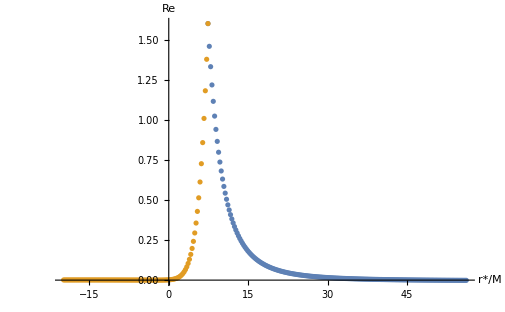

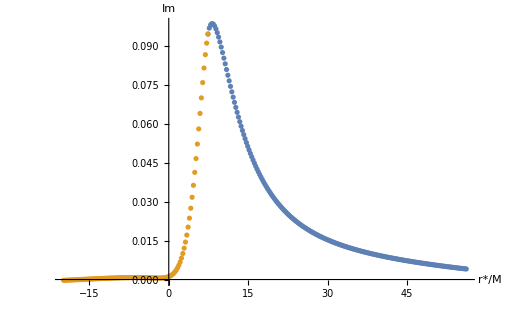

```mathematica
ltry=Abs[mm]+2;
qitry=1;
tbl1=Table[(normfacs[[qitry]]/.{r->rsR[[ri]]})*Re@sallR[[ri]][[qitry]][[ltry+1]],{ri,1,Length[rstarsR]}];
tbl2=Table[(normfacs[[qitry]]/.{r->rsL[[ri]]})*Re@sallL[[ri]][[qitry]][[ltry+1]],{ri,1,Length[rstarsL]}];
fig1=ListPlot[{Transpose@{rstarsR,tbl1},Transpose@{rstarsL,tbl2}},PlotRange->All,AxesLabel->{"r*/M  ","Re"}]
tbl1=Table[(normfacs[[qitry]]/.{r->rsR[[ri]]})*Im@sallR[[ri]][[qitry]][[ltry+1]],{ri,1,Length[rstarsR]}];
tbl2=Table[(normfacs[[qitry]]/.{r->rsL[[ri]]})*Im@sallL[[ri]][[qitry]][[ltry+1]],{ri,1,Length[rstarsL]}];
fig2=ListPlot[{Transpose@{rstarsR,tbl1},Transpose@{rstarsL,tbl2}},PlotRange->All,AxesLabel->{"r*/M  ","Im"}]
```

## B. Fill 2D grid

### Spheroidal harmonics set up

```mathematica
(* aω0prec=SetPrecision[aω0,50]; *)
sphermethod={"SphericalExpansion","NumTerms"->nterms};
SetOptions[SpinWeightedSpheroidalHarmonicS,Method->sphermethod];
```

```mathematica
GetSsubs[ltry_,θtry_?NumericQ]:=Module[{tbl1,tbl2,fns},
aω0prec=SetPrecision[aω0,2*prec]; 
(* Extended precision appears to be necessary to avoid "failed to converge" messages. *)
tbl1={Sp2[θ]->SpinWeightedSpheroidalHarmonicS[2,ltry,mm,aω0prec][θtry,0],
Sp2'[θ]->(D[SpinWeightedSpheroidalHarmonicS[2,ltry,mm,aω0prec][θ,0],θ]/.{θ->θtry}),
Sm2[θ]->SpinWeightedSpheroidalHarmonicS[-2,ltry,mm,aω0prec][θtry,0],
Sm2'[θ]->(D[SpinWeightedSpheroidalHarmonicS[-2,ltry,mm,aω0prec][θ,0],θ]/.{θ->θtry}),
Sp1[θ]->SpinWeightedSpheroidalHarmonicS[1,ltry,mm,aω0prec][θtry,0],
Sp1'[θ]->(D[SpinWeightedSpheroidalHarmonicS[1,ltry,mm,aω0prec][θ,0],θ]/.{θ->θtry}),
Sm1[θ]->SpinWeightedSpheroidalHarmonicS[-1,ltry,mm,aω0prec][θtry,0],
Sm1'[θ]->(D[SpinWeightedSpheroidalHarmonicS[-1,ltry,mm,aω0prec][θ,0],θ]/.{θ->θtry})
};
fns={Sin[θ],Cos[θ],Cot[θ],Csc[θ]};
tbl2=Map[#->(#/.θ->θtry)&,fns];
Join[tbl1,tbl2]
]
Timing[GetSsubs[20,SetPrecision[π/4,prec]]]
```

```mathematica
GetS0subs[θtry_?NumericQ,lval_,κord_:6]:=Module[{myfn,tbl1,tbl2,fns},
myfn=(Coefficient[#,S0[θ]]/.{θ->θtry})*S0[θ]+(Coefficient[#,S0'[θ]]/.{θ->θtry})*S0'[θ]&;
tbl1=Table[S0[ll]''[θ]->(Map[myfn,S0''[θ]/.S0subs]/.{S0[θ]->S0[ll][θ],S0'[θ]->S0[ll]'[θ]}/.{λ0->eigs0[[ll+1]]}/.awsubs),
{ll,Max[lmins0,lval-κord],Min[lmax,lval+κord],2}];
tbl2=Table[
{S0[ll][θ]->(SpinWeightedSpheroidalHarmonicS[0,ll,mm,aω0prec][θtry,0]),
S0[ll]'[θ]->((D[SpinWeightedSpheroidalHarmonicS[0,ll,mm,aω0prec][θ,0],θ]/.{θ->θtry}))},
{ll,Max[lmins0,lval-κord],Min[lmax,lval+κord],2}]//Flatten;
fns={Sin[θ],Cos[θ],Cot[θ],Csc[θ]};
tbl3=Map[#->(#/.θ->θtry)&,fns];
Join[tbl1/.tbl2,tbl2,tbl3]
];
Timing[GetS0subs[SetPrecision[π/4,prec],2]]
```

### Spin 2 expressions

```mathematica
ψm=Pm2[r]*Sm2[θ];
αm=β/(3*I*ω*ρc)*Dop[Pm2[r]]*Ldag[2,Sm2[θ]];
χm=β/(24*ω^2)*Dop[Dop[Pm2[r]]]*Ldag[1,Ldag[2,Sm2[θ]]];
ψp=Pp2[r]*Sp2[θ];
αp=β/(-3*I*ω*ρc)*Ddag[Pp2[r]]*Lop[2,Sp2[θ]];
χp=β/(24*ω^2)*Ddag[Ddag[Pp2[r]]]*Lop[1,Lop[2,Sp2[θ]]];
χdiff=χm-χp;

αmprime=β/(3*I*ω*ρ)*Dop[Pm2[r]]*Lop[2,Sp2[θ]];
αpprime=β/(-3*I*ω*ρ)*Ddag[Pp2[r]]*Ldag[2,Sm2[θ]];
χmprime=β/(24*ω^2)*Dop[Dop[Pm2[r]]]*Lop[1,Lop[2,Sp2[θ]]];
χpprime=β/(24*ω^2)*Ddag[Ddag[Pp2[r]]]*Ldag[1,Ldag[2,Sm2[θ]]];
χdiffprime=χmprime-χpprime;
```

#### Metric components

```mathematica
h2lplp=1/(-6*ω^2*Δ[r]^2)*Pp2[r]*(sgn*Ldag[1,Ldag[2,Sm2[θ]]]+Lop[1,Lop[2,Sp2[θ]]]);
h2lmlm=1/(-6*ω^2*Δ[r]^2)*Pm2[r]*(Ldag[1,Ldag[2,Sm2[θ]]]+sgn*Lop[1,Lop[2,Sp2[θ]]]);
h2mpmp=1/(-6*ω^2)*Sp2[θ]*(sgn*Dop[Dop[Pm2[r]]]+Ddag[Ddag[Pp2[r]]]);
h2mmmm=1/(-6*ω^2)*Sm2[θ]*(Dop[Dop[Pm2[r]]]+sgn*Ddag[Ddag[Pp2[r]]]);

t1=2*(ρ*Dop[Ldag[χdiffprime]]-Ldag[χdiffprime]-D[ρ,θ]*Dop[χdiffprime]);
t2=-ρ^3/Δ[r]*(Δ[r]*Dop[Dop[αmprime]]+Ldag[Ldag[1,αpprime]]);
ρh2lpmp=sgn*(t1+t2);
t1=2*(ρc*Dop[Lop[χdiff]]-Lop[χdiff]-D[ρc,θ]*Dop[χdiff]);
t2=-ρc^3/Δ[r]*(Δ[r]*Dop[Dop[αm]]+Lop[Lop[1,αp]]);
ρch2lpmm=t1+t2;
t1=2*(ρc*Ddag[Ldag[χdiff]]-Ldag[χdiff]-D[ρc,θ]*Ddag[χdiff]);
t2=ρc^3/Δ[r]*(Δ[r]*Ddag[Ddag[αp]]+Ldag[Ldag[1,αm]]);
ρch2lmmp=t1+t2;
t1=2*(ρ*Ddag[Lop[χdiffprime]]-Lop[χdiffprime]-D[ρ,θ]*Ddag[χdiffprime]);
t2=ρ^3/Δ[r]*(Δ[r]*Ddag[Ddag[αpprime]]+Lop[Lop[1,αmprime]]);
ρh2lmmm=sgn*(t1+t2);

t0=Σ*(Dop[Δ[r]*Ddag[χdiff]]+Ddag[Δ[r]*Dop[χdiff]])-2*Δ[r]*D[Σ,r]*D[χdiff,r]+2*D[Σ,θ]*D[χdiff,θ];
t1=Σ*(Dop[ρc^2*Ldag[1,αm]]-Ddag[ρc^2*Lop[1,αp]]);
t2=-ρc^2*D[Σ,r]*(Ldag[1,αm]-Lop[1,αp]);
t3=ρc^2*D[Σ,θ]*(Ddag[αp]-Dop[αm]);
ΣΔhlplm=t0+t1+t2+t3;
```

```mathematica
hLs2={h2lplp,h2lmlm,h2mpmp,h2mmmm,ρh2lpmp,ρch2lpmm,ρch2lmmp,ρh2lmmm,ΣΔhlplm,0}/.{β->1/(-6*I*M*ω)};
```

### Spin 1 expressions

#### Metric perturbations

```mathematica
Bsubs={BB^2->λ^2+4*a*m*ω-4*a^2*ω^2};
```

```mathematica
calP=(Dop[Pm1[r]]+sgn*Ddag[Pp1[r]])//Simplify;
calS=(Ldag[1,Sm1[θ]]-sgn*Lop[1,Sp1[θ]])//Simplify;
h1lplp=sgn*2/Δ[r]*Dop[-1,Pp1[r]]*calS;
h1lmlm=2/Δ[r]*Ddag[-1,Pm1[r]]*calS;
h1mpmp=sgn*2*calP*Ldag[-1,Sp1[θ]];
h1mmmm=-2*calP*Lop[-1,Sm1[θ]];

ρh1lpmp=sgn*(ρ*Dop[calP]-2*calP)*Sp1[θ]+sgn*1/Δ[r]*Pp1[r]*(ρ*Ldag[calS]-2*D[ρ,θ]*calS);
ρch1lpmm=-(ρc*Dop[calP]-2*calP)*Sm1[θ]+sgn*1/Δ[r]*Pp1[r]*(ρc*Lop[calS]-2*D[ρc,θ]*calS);
ρch1lmmp=sgn*(ρc*Ddag[calP]-2*calP)*Sp1[θ]+1/Δ[r]*Pm1[r]*(ρc*Ldag[calS]-2*D[ρc,θ]*calS);
ρh1lmmm=-(ρ*Ddag[calP]-2*calP)*Sm1[θ]+1/Δ[r]*Pm1[r]*(ρ*Lop[calS]-2*D[ρ,θ]*calS);

ΣΔh1lplm=(Σ*calP*calS-D[Σ,r]*(Pm1[r]+sgn*Pp1[r])*calS+sgn*calP*D[Σ,θ]*(Sp1[θ]-sgn*Sm1[θ]));

hLs1={h1lplp,h1lmlm,h1mpmp,h1mmmm,ρh1lpmp,ρch1lpmm,ρch1lmmp,ρh1lmmm,ΣΔh1lplm,0};
```

### Spin 0 expressions

#### Metric perturbations

```mathematica
hfn=h[r]*S0[l][θ];
κfn=κ[r,θ];  
h0lplp=-(1/(I*ω)*Dop[r*Dop[hfn]]+4*Dop[Dop[κfn]]);
h0lmlm=-(-1/(I*ω)*Ddag[r*Ddag[hfn]]+4*Ddag[Ddag[κfn]]);
t0=(-a*Cos[θ]/ω*Ldag[hfn]+4*Ldag[κfn]);
h0mpmp=-Ldag[-1,t0];
t0=(a*Cos[θ]/ω*Lop[hfn]+4*Lop[κfn]);
h0mmmm=-Lop[-1,t0];

t0=Σ/(2*I*ω)*Dop[Ldag[hfn]]+a/ω*(r*Sin[θ]*Dop[hfn]+Cos[θ]*Ldag[hfn])+4*ρ*Dop[Ldag[κfn]]-4*(Ldag[κfn]-I*a*Sin[θ]*Dop[κfn]);
ρh0lpmp=-t0;
t0=Σ/(2*I*ω)*Dop[Lop[hfn]]-a/ω*(r*Sin[θ]*Dop[hfn]+Cos[θ]*Lop[hfn])+4*ρc*Dop[Lop[κfn]]-4*(Lop[κfn]+I*a*Sin[θ]*Dop[κfn]);
ρch0lpmm=-t0;
t0=-Σ/(2*I*ω)*Ddag[Ldag[hfn]]+a/ω*(r*Sin[θ]*Ddag[hfn]+Cos[θ]*Ldag[hfn])+4*ρc*Ddag[Ldag[κfn]]-4*(Ldag[κfn]+I*a*Sin[θ]*Ddag[κfn]);
ρch0lmmp=-t0;
t0=-Σ/(2*I*ω)*Ddag[Lop[hfn]]-a/ω*(r*Sin[θ]*Ddag[hfn]+Cos[θ]*Lop[hfn])+4*ρ*Ddag[Lop[κfn]]-4*(Lop[κfn]-I*a*Sin[θ]*Ddag[κfn]);
ρh0lmmm=-t0;
(*
h0mpmm=-(a*Sin[θ]*QQ/ω-2*Σ)*hfn-2*(Lop[1,Ldag[κfn]]+Ldag[1,Lop[κfn]])+4/Σ*(-D[Σ,r]*Δ*D[κfn,r]+D[Σ,θ]*D[κfn,θ]); *)
ΣΔh0lplm=-Σ*(K[r]/ω-2*Σ)*hfn-2*Σ*(Dop[Δ[r]*Ddag[κfn]]+Ddag[Δ[r]*Dop[κfn]])-4*(-D[Σ,r]*Δ[r]*D[κfn,r]+D[Σ,θ]*D[κfn,θ]);
```

```mathematica
hLs0={h0lplp,h0lmlm,h0mpmp,h0mmmm,ρh0lpmp,ρch0lpmm,ρch0lmmp,ρh0lmmm,ΣΔh0lplm,hfn};
```

#### Weyl scalars

```mathematica
(* Obviously, these are going to be zero. Commenting out to improve run time.

t0=Ldag[-1,Ldag[h0lplp/ρ]]+Dop[Dop[h0mpmp/ρ]];
t1a=Ldag[-1,h0lpmp]+D[ρ,θ]/ρ*h0lpmp;
t1b=Dop[h0lpmp]+1/ρ*h0lpmp;
t1=Dop[t1a]-t1a/ρ+Ldag[-1,t1b]-D[ρ,θ]/ρ*t1b;
t2=1/(4*ρ)*(t0-1/ρ*t1);
ψ0=Simplify[t2/.h0subs/.S0subs]
t0=Lop[-1,Lop[h0lmlm/ρ]]+Ddag[Ddag[h0mmmm/ρ]];
t1a=Lop[-1,h0lmmm]+D[ρ,θ]/ρ*h0lmmm;
t1b=Ddag[h0lmmm]+1/ρ*h0lmmm;
t1=Ddag[t1a]-t1a/ρ+Lop[-1,t1b]-D[ρ,θ]/ρ*t1b;
t2=1/(4*ρ)*(t0-1/ρ*t1);
ψ4til=Simplify[t2/.h0subs/.κ0subs/.S0subs]
t0=Lop[-1,Lop[h0lplp/ρc]]+Dop[Dop[h0mmmm/ρc]];
t1a=Lop[-1,h0lpmm]+D[ρc,θ]/ρc*h0lpmm;
t1b=Dop[h0lpmm]+1/ρc*h0lpmm;
t1=Dop[t1a]-t1a/ρc+Lop[-1,t1b]-D[ρc,θ]/ρc*t1b;
t2=1/(4*ρc)*(t0-1/ρc*t1);
ψ0p=Simplify[t2/.h0subs/.κ0subs/.S0subs]
t0=Ldag[-1,Ldag[h0lmlm/ρc]]+Ddag[Ddag[h0mpmp/ρc]];
t1a=Ldag[-1,h0lmmp]+D[ρc,θ]/ρc*h0lmmp;
t1b=Ddag[h0lmmp]+1/ρc*h0lmmp;
t1=Ddag[t1a]-t1a/ρc+Ldag[-1,t1b]-D[ρc,θ]/ρc*t1b;
t2=1/(4*ρc)*(t0-1/ρc*t1);
ψ4ptil=Simplify[t2/.h0subs/.κ0subs/.S0subs]

*)
```

### Fill grid

```mathematica
(* In principle, the computation should be faster if done in parallel.
In practice, I am finding that it is significantly slower - I need to take advice on how to improve matters. *)
InParallel=False; (* Change if necessary. *)
If[InParallel,
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"];
  ParallelNeeds["Teukolsky`"];
ParallelNeeds["KerrGeodesics`"];
];
```

```mathematica
(* These are somewhat-arbitrary factors to multiply the metric pert projections by, to get components which behave "nicely" at the horizon and at infinity *)
normfacs={Δ[r]^2/r^3,Δ[r]^2/r^3,1/r,1/r,1/r,1/r,1/r,1/r,1/r^3,1/r};
```

```mathematica
chopdelta=SetPrecision[10^(-14),prec];
CalcGridMode[ltry_]:=Module[{grid2D,subdata,sign,term0,term1,term2,ΔKtbl,comp21,comp0,S0gridsubs,S12gridsubs,dataline,qi,ki,ri},
If[InParallel,
sphermethod={"SphericalExpansion","NumTerms"->nterms};
SetOptions[SpinWeightedSpheroidalHarmonicS,Method->sphermethod]; (* Need to set this for each kernel I think. Alternatively I could use ParallelEvaluate for this. *)
];
grid2D=Developer`ToPackedArray[Table[SetPrecision[0,prec],{20},{qpts},{rpts}]];
sign=(-1)^(ltry+mm);
term2=(normfacs*hLs2)/.Pp2subs/.Pp2repl/.Pm2subs/.Crepl0/.{sgn->sign}/.Sp2subs/.Sm2subs/.AArepl/.{l->ltry}/.{Λ->eigs2[[ltry+1]]}/.awsubs;
term1=(normfacs*hLs1)/.Pp1subs/.Pp1repl/.Pm1subs/.Sp1subs/.Sm1subs/.BBrepl/.{sgn->sign}/.{l->ltry}/.{λ->eigs1[[ltry+1]]}/.awsubs;
term0=(normfacs*hLs0)/.{l->ltry}/.awsubs;
ΔKtbl=Table[Map[#[[1]]->(#[[2]]/.awsubs/.{r->rs[[ri]]})&,ΔKsubs],{ri,1,rpts}];
Print["Evaluating s=2,1 radial functions ..."];
Monitor[comp21=Chop[Table[(term2+term1)/.GetPsubs[ltry,rs[[ri]]]/.ΔKtbl[[ri]]/.{r->rs[[ri]]},{ri,1,rpts}],chopdelta];, ri];
Print["Evaluating s=0 radial functions ..."];
Monitor[comp0=Chop[Table[term0/.Getκsubs[ltry,rs[[ri]]]/.ΔKtbl[[ri]]/.{r->rs[[ri]]},{ri,1,rpts}],chopdelta];, ri];
Print["Evaluating s=0 angular functions ..."];
S0gridsubs=Monitor[Table[If[(ki==qpts)||(ki==1),{},GetS0subs[qs[[ki]],ltry]],{ki,1,Length[qs]}],ki];
Print["Evaluating s=1,2 angular functions ..."];
S12gridsubs=Monitor[Table[GetSsubs[ltry,qs[[ki]]],{ki,1,Length[qs]}],ki];
Print["Adding data to 2D grid ..."];
Monitor[
For[ri=1,ri<=rpts,ri++,
For[ki=1,ki<=qpts,ki++,
dataline=If[(ki==qpts)||(ki==1),Table[SetPrecision[0,prec],{10}],((comp21[[ri]]/.S12gridsubs[[ki]])+(comp0[[ri]]/.S0gridsubs[[ki]]))];
For[qi=1,qi<=10,qi++,
grid2D[[qi,ki,ri]]=Re[dataline[[qi]]];
grid2D[[10+qi,ki,ri]]=Im[dataline[[qi]]];
];
];
];
,ri];
grid2D
];
```

```mathematica
(* Make an array for storing the data for export *)
lsum=lplot;
{Length[rstars],rstars[[1]],rstars[[-1]]};
(* Sum the modes *)
data2D=Table[{},{ll,0,lsum}];
Timing[
If[InParallel,
data2D=ParallelTable[CalcGridMode[ltry],{ltry,Abs[mm],lsum}]
,
For[ltry=Abs[mm],ltry<=lsum,ltry=ltry+1,
Print["Calculating for l = " <>ToString[ltry]];
data2D[[ltry]]=CalcGridMode[ltry];
]
]
]
```

Calculating for l = 2

Evaluating s=2,1 radial functions ...

Evaluating s=0 radial functions ...

Evaluating s=0 angular functions ...

Evaluating s=1,2 angular functions ...

Adding data to 2D grid ...

Calculating for l = 3

Evaluating s=2,1 radial functions ...

Evaluating s=0 radial functions ...

Evaluating s=0 angular functions ...

Evaluating s=1,2 angular functions ...

Adding data to 2D grid ...

Calculating for l = 4

Evaluating s=2,1 radial functions ...

$Aborted

```mathematica
data2Dsum=Sum[data2D[[ltry]],{ltry,Abs[mm],lsum}]; (* Add all the modes together. *)
```

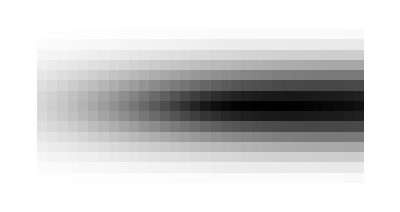

```mathematica
ArrayPlot[data2Dsum[[11]]]
```

```mathematica
(* Export the data to file *)
For[ll=Abs[mm],ll<=lsum,ll++,
filen=directory<>"data/mode2D_"<>ToString[iConfig]<>"_l"<>ToString[ll]<>".bin";
Export[filen,data2D[[ll]],"Real32"]
];
filen=directory<>"data/mode2D_"<>ToString[iConfig]<>".bin";
Export[filen,data2Dsum,"Real32"]
```

/Users/sm1srd/Code/KerrLorenz/data/mode2D_10_9922.bin